Info on the notebook:
This notebook uses the BiGONLight package to compute observables in conformal EdS model.
It is structured as follows: 
- model set-up:  give the 4D metric tensor components as input and compute the 3+1 quantities lapse α, shift β^i, spatial metric γ_ij, extrinsic curvature K_ij and the normal vector n^μ;
- geodesic: provide initial position and tangent vector {x^μ, ℓ^μ} as input to find null geodesics;
- parallel transported frame: give the initial conditions for a frame (ϕ^μ)_αthat will be parallel transported along the computed geodesic (we use the SNF, i.e. (ϕ^μ)_α={u^μ,(ϕ^μ)_1,(ϕ^μ)_2, ℓ^μ} with u^μ the four-velocity and (ϕ^μ)_A two orthonormal vectors)
- optical tidal matrix: compute the optical tidal matrix (R^μ)_ρσν ℓ^ρ ℓ^σ in the parallel propagated frame; 
- BGO: compute and solve the Geodesic Deviation Equation for the Bi-local Geodesic Operators along the null geodesic;
- observables: compute the optical observables in the BGO framework: redshift, redshift drift, angular diameter distance, luminosity distance, parallax distance, distance slip, convergence and shear.

Set the current directory as working directory and load the package.

```mathematica
SetDirectory[NotebookDirectory[]];
Needs["bigonlight6`"]
```

```mathematica
prec=16
$PreRead=(#/.s_String/;StringMatchQ[s,NumberString]&&Precision@ToExpression@s==MachinePrecision:>s<>"`16."&);(*MachinePrecision:>s<>"`prec."&*)
```

16

a generic direction can be written as 𝓋^μ=𝓋^0∂_0 +γ(sinχ cosξ ∂_1 +sinχ sinξ ∂_1 +cosχ ∂_3)=(𝓋^0(∂_0))^μ+γ (N⃗)^μ with respect to the local tetrad ∂_μ . 
In particular for a null direction 𝓋^0=±1 and γ=1 , while for a timelike direction 𝓋^0=±c γ and ψ=c γ β  where β=vel/c the normalized velocity and γ=1/(√(1-β^2)) the Lorentz factor.
import data on files
BGO=<<”BGO_data.m”;
totN=<<”geodesic_data.m”;

save plots
Export[“lowz-exp.pdf”, %]

```mathematica
𝒱[Vt_,lorentz_,direction1_,direction2_]:=
Module[{V0=Vt, γ=lorentz,χ=direction1,ξ=direction2},
V0{1,0,0,0}+γ(Sin[χ]Cos[ξ]{0,1,0,0}+Sin[χ]Sin[ξ]{0,0,1,0}+Cos[χ]{0,0,0,1})
]

StandardPlotStyle[size_,sizelegend_,ylabel_,xlabel_,title_,legend_,position_]:=Module[{ft=size,ftL=sizelegend,yL=ylabel,xL=xlabel,pt=title,list=legend,pl=position},
If[ list=={},{FrameLabel->{{yL,""},{xL,""}},Frame->True,FrameTicks->True,FrameStyle->Directive[FontSize->ft],GridLines->Automatic,GridLinesStyle->Directive[Gray,Opacity[0.2],Dashed],PlotLabel->Style[pt,Bold,FontSize->ft]},{FrameLabel->{{yL,""},{xL,""}},Frame->True,FrameTicks->True,FrameStyle->Directive[FontSize->ft],GridLines->Automatic,GridLinesStyle->Directive[Gray,Opacity[0.2],Dashed],PlotLabel->Style[pt,Bold,FontSize->ft],PlotLegends->Placed[LineLegend[Table[Style[list[[m]],FontSize->ftL],{m,1,Length[list]}]],pl]},Print["Error"]]];
```

# FLRWSolver

## Import data from spacetime simulation

```mathematica
iℋ=SetPrecision[Take[Cases[Import["Data_FLRWSolver/res_0.05/H.average.asc","Table"],{__?NumericQ}],All,-2],prec];
```

```mathematica
Do[If[iℋ[[i,2]]> 10^-8,rel=i-1;Print[ToString[ {i,iℋ[[i,1]],iℋ[[i,2]]}]];Break[],rel=i-1],{i,1,Length@iℋ}]
```

```mathematica
iℋ[[rel,2]]
rel
```

-5.64689403538105×10^-18

64400

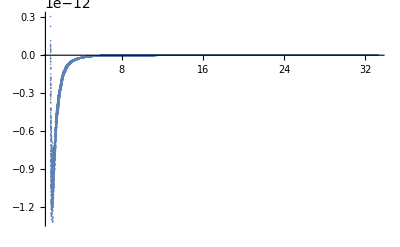

```mathematica
ListPlot[Table[iℋ[[i]],{i,1,rel}],PlotRange->All]
```

```mathematica
iα=SetPrecision[Take[Take[Cases[Import["Data_FLRWSolver/res_0.05/alp.average.asc","Table"],{__?NumericQ}],rel],All,-2],prec];
```

```mathematica
iα[[Length@iα]]
iℋ[[rel]]
```

{33.1995,1102.20680013852}

{33.1995,-5.64689403538105×10^-18}

```mathematica
iγxx=SetPrecision[Take[Take[Cases[Import["Data_FLRWSolver/res_0.05/gxx.average.asc","Table"],{__?NumericQ}],rel],All,-2],prec];
iγxy=SetPrecision[Take[Take[Cases[Import["Data_FLRWSolver/res_0.05/gxy.average.asc","Table"],{__?NumericQ}],rel],All,-2],prec];
iγxz=SetPrecision[Take[Take[Cases[Import["Data_FLRWSolver/res_0.05/gxz.average.asc","Table"],{__?NumericQ}],rel],All,-2],prec];
iγyy=SetPrecision[Take[Take[Cases[Import["Data_FLRWSolver/res_0.05/gyy.average.asc","Table"],{__?NumericQ}],rel],All,-2],prec];
iγyz=SetPrecision[Take[Take[Cases[Import["Data_FLRWSolver/res_0.05/gyz.average.asc","Table"],{__?NumericQ}],rel],All,-2],prec];
iγzz=SetPrecision[Take[Take[Cases[Import["Data_FLRWSolver/res_0.05/gzz.average.asc","Table"],{__?NumericQ}],rel],All,-2],prec];
```

```mathematica
ikxx=SetPrecision[Take[Take[Cases[Import["Data_FLRWSolver/res_0.05/kxx.average.asc","Table"],{__?NumericQ}],rel],All,-2],prec];
ikxy=SetPrecision[Take[Take[Cases[Import["Data_FLRWSolver/res_0.05/kxy.average.asc","Table"],{__?NumericQ}],rel],All,-2],prec];
ikxz=SetPrecision[Take[Take[Cases[Import["Data_FLRWSolver/res_0.05/kxz.average.asc","Table"],{__?NumericQ}],rel],All,-2],prec];
ikyy=SetPrecision[Take[Take[Cases[Import["Data_FLRWSolver/res_0.05/kyy.average.asc","Table"],{__?NumericQ}],rel],All,-2],prec];
ikyz=SetPrecision[Take[Take[Cases[Import["Data_FLRWSolver/res_0.05/kyz.average.asc","Table"],{__?NumericQ}],rel],All,-2],prec];
ikzz=SetPrecision[Take[Take[Cases[Import["Data_FLRWSolver/res_0.05/kzz.average.asc","Table"],{__?NumericQ}],rel],All,-2],prec];
```

```mathematica
iρ=SetPrecision[Take[Take[Cases[Import["Data_FLRWSolver/res_0.05/rho.average.asc","Table"],{__?NumericQ}],rel],All,-2],prec];
```

```mathematica
iα[[Length@iα,1]]
iγxx[[Length@iα,1]]
iγxy[[Length@iα,1]]
iγxz[[Length@iα,1]]
iγyy[[Length@iα,1]]
iγyz[[Length@iα,1]]
iγzz[[Length@iα,1]]
ikxx[[Length@ikxx,1]]
ikxy[[Length@ikxy,1]]
ikxz[[Length@ikxz,1]]
ikyy[[Length@ikyy,1]]
ikyz[[Length@ikyz,1]]
ikzz[[Length@ikzz,1]]
iρ[[Length@iρ,1]]
```

33.1995

33.1995

33.1995

«11 more identical outputs»

For convenience, we normalise all quantities such that at present time η_0=1, a_0=1, ℋ_0==2

```mathematica
iαN=Table[{iα[[i,1]]/iα[[Length@iα,1]],iα[[i,2]]/iα[[Length@iα,2]]},{i,1,Length@iα}];

iγxxN=Table[{iγxx[[i,1]]/iγxx[[Length@iγxx,1]],iγxx[[i,2]]/iγxx[[Length@iγxx,2]]},{i,1,Length@iγxx}];
iγxyN=Table[{iγxy[[i,1]]/iγxy[[Length@iγxy,1]],iγxy[[i,2]]},{i,1,Length@iγxy}];
iγxzN=Table[{iγxz[[i,1]]/iγxz[[Length@iγxz,1]],iγxz[[i,2]]},{i,1,Length@iγxz}];
iγyyN=Table[{iγyy[[i,1]]/iγyy[[Length@iγyy,1]],iγyy[[i,2]]/iγyy[[Length@iγyy,2]]},{i,1,Length@iγyy}];
iγyzN=Table[{iγyz[[i,1]]/iγyz[[Length@iγyz,1]],iγyz[[i,2]]},{i,1,Length@iγyz}];
iγzzN=Table[{iγzz[[i,1]]/iγzz[[Length@iγzz,1]],iγzz[[i,2]]/iγzz[[Length@iγzz,2]]},{i,1,Length@iγzz}];
ikxxN=Table[{ikxx[[i,1]]/ikxx[[Length@ikxx,1]],2 ikxx[[i,2]]/Abs[ikxx[[Length@ikxx,2]]]},{i,1,Length@ikxx}];
ikxyN=Table[{ikxy[[i,1]]/ikxy[[Length@ikxy,1]],ikxy[[i,2]]},{i,1,Length@ikxy}];
ikxzN=Table[{ikxz[[i,1]]/ikxz[[Length@ikxz,1]],ikxz[[i,2]]},{i,1,Length@ikxz}];
ikyyN=Table[{ikyy[[i,1]]/ikyy[[Length@ikyy,1]],2 ikyy[[i,2]]/Abs[ikyy[[Length@ikyy,2]]]},{i,1,Length@ikyy}];
ikyzN=Table[{ikyz[[i,1]]/ikyz[[Length@ikyz,1]],ikyz[[i,2]]},{i,1,Length@ikyz}];
ikzzN=Table[{ikzz[[i,1]]/ikzz[[Length@ikzz,1]],2 ikzz[[i,2]]/Abs[ikzz[[Length@ikzz,2]]]},{i,1,Length@ikzz}];

iρN=Table[{iρ[[i,1]]/iρ[[Length@iρ,1]],iρ[[i,2]]/iρ[[Length@iρ,2]]},{i,1,Length@iρ}];
```

## Units and Parameters

```mathematica
L=2/iα[[Length@iα,2]]^(1/2)1/H0/.{H0->67.36/299792.458, Ωm0->1}(*Mpc*);
ρin=3/(2π(*G*))(*1/L^2*)

(*Subscript[ℋ, in]=Subscript[𝒽, in]/L=2/L->*)  𝒽0=2
```

3/(2 π)

2

```mathematica
ηin=iαN[[1,1]]
ETA0=iαN[[Length@iαN,1]]
```

0.0301209355562584

1.

```mathematica
param={Ωm0->1, ΩΛ->0, c->1}(*arXiv:1807.06209 (Tab 2 5th column) , H0 units: km/s(Mpc)^-1.*)
```

{Ωm0→1,ΩΛ→0,c→1}

## Model set-up

```mathematica
α=SetPrecision[Interpolation[iαN],prec];
ρ=SetPrecision[Interpolation[iρN],prec];
```

```mathematica
α[ηin]
ηin^2
ρ[ηin]
```

0.00090727075887603

0.00090727075878427

1.3390267661304×10^9

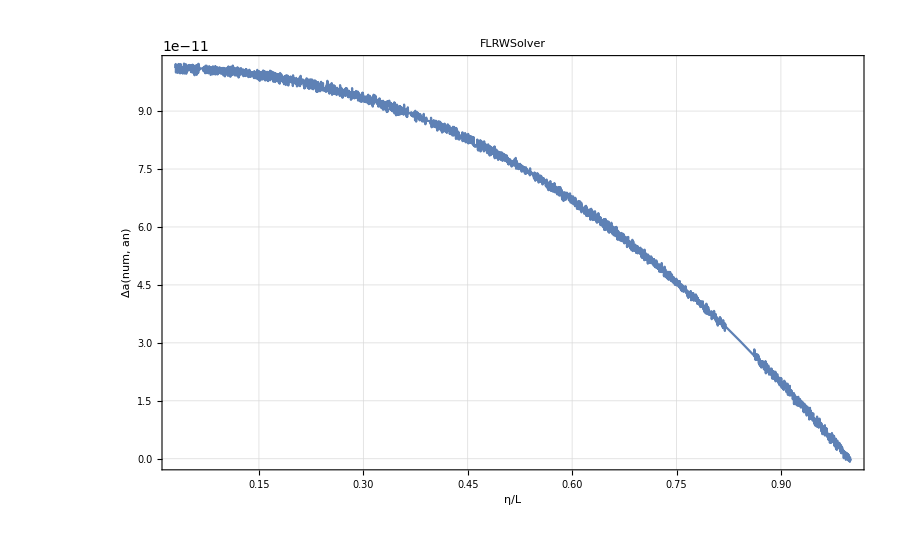

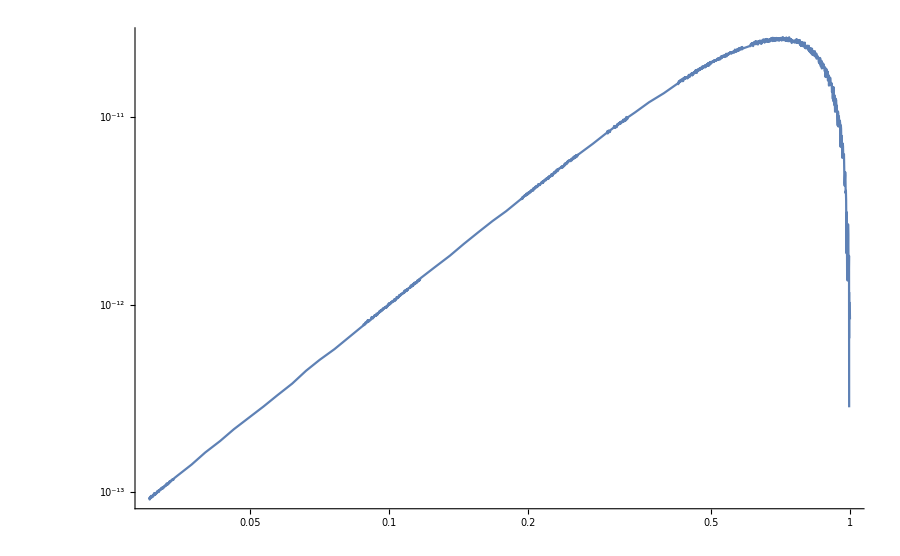

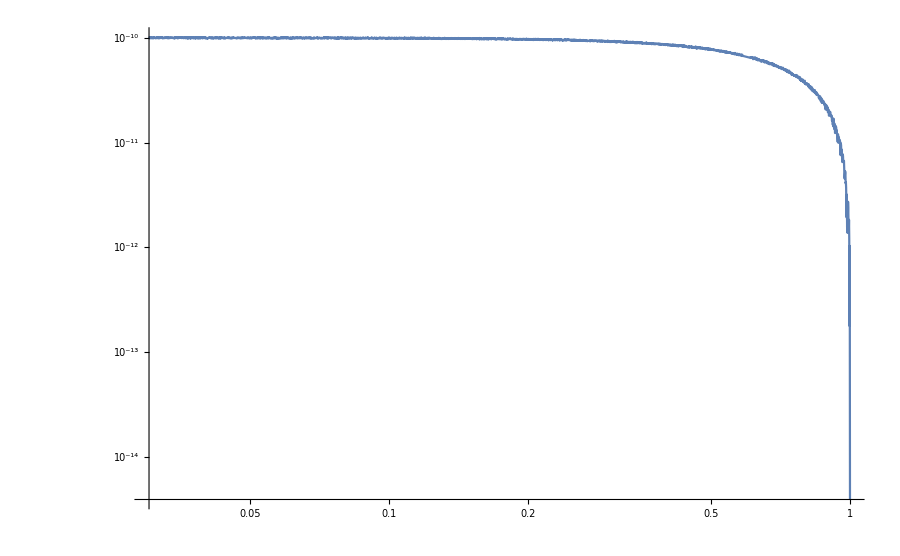

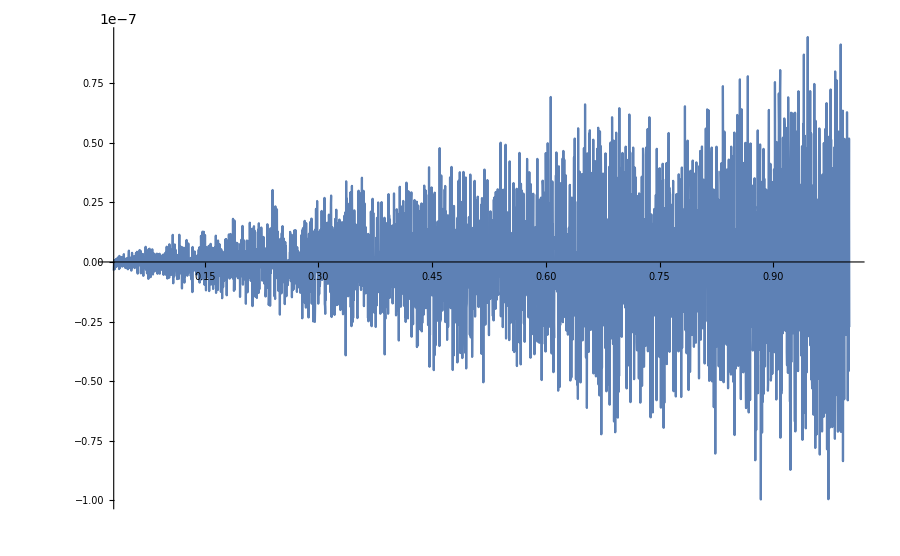

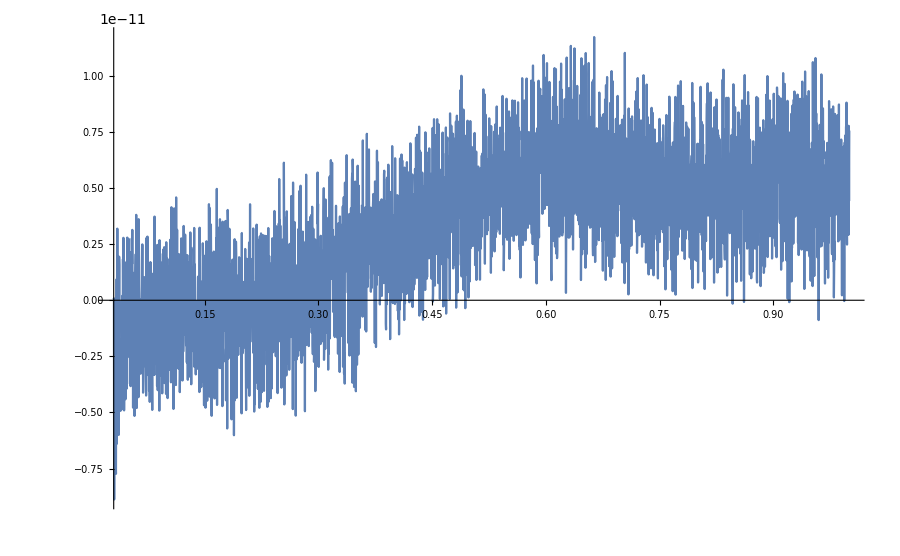

```mathematica
Plot[{(α[η]-η^2)/η^2},{η,ηin,ETA0},PlotRange->All,WorkingPrecision->40,ImageSize->900,Evaluate[StandardPlotStyle[16,24,"Δa(num, an)","η/L","FLRWSolver",{},{}]]]
LogLogPlot[Abs[α[η]-η^2],{η,ηin,ETA0},PlotRange->All]
LogLogPlot[Abs[(α[η]-η^2)/η^2],{η,ηin,ETA0},PlotRange->All]
(*Plot[{α[η]-η^2},{η,ηin,ETA0}]*)
Plot[{(α'[η]/α[η]-2/η)/(2/η)},{η,ηin,ETA0}]
Plot[(α[η]^3 ρ[η])/(α[ηin]^3 ρ[ηin])-1,{η,ηin,ETA0},PlotRange->All,WorkingPrecision->30]
```

```mathematica
γ={{γxx[η],γxy[η],γxz[η]},{γxy[η],γyy[η],γyz[η]},{γxz[η],γyz[η],γzz[η]}};
```

```mathematica
𝒦={{kxx[η],kxy[η],kxz[η]},{kxy[η],kyy[η],kyz[η]},{kxz[η],kyz[η],kzz[η]}};
```

```mathematica
β={0,0,0};
nu=Join[{1/α[η]},-β/α[η]]
nd={-α[η],0,0,0}
```

{1/(InterpolatingFunction[{{0.03012093555625838, 1.000000000000000}}, <>][η]),0,0,0}

{-InterpolatingFunction[{{0.03012093555625838, 1.000000000000000}}, <>][η],0,0,0}

```mathematica
A[η_]:=η^2
```

```mathematica
Plot[{ (Det[γ]^(1/6)-A[η])/A[η]},{η,ηin,ETA0},PlotRange->All,WorkingPrecision->30]
Plot[{ α[η]-Det[γ]^(1/6)(*-α[ηin](η+1)^2*)},{η,ηin,ETA0},PlotRange->All,WorkingPrecision->30]
```

-Graphics-

-Graphics-

```mathematica
X4={η,x,y,z};
X={x,y,z};
V={v1,v2,v3};
e={e1,e2,e3};
Energy={energy, λ};
```

## Geodesic

```mathematica
geodBG=GeodesicEquations[X,V,γ,𝒦,α[η],β,η];
```

```mathematica
enereqBG=EnergyEquations[γ,𝒦,α[η],β,Energy,X,V,η];
```

```mathematica
γxx=SetPrecision[Interpolation[iγxxN],prec];
γxy=SetPrecision[Interpolation[iγxyN],prec];
γxz=SetPrecision[Interpolation[iγxzN],prec];
γyy=SetPrecision[Interpolation[iγyyN],prec];
γyz=SetPrecision[Interpolation[iγyzN],prec];
γzz=SetPrecision[Interpolation[iγzzN],prec];
kxx=SetPrecision[Interpolation[ikxxN],prec];
kxy=SetPrecision[Interpolation[ikxyN],prec];
kxz=SetPrecision[Interpolation[ikxzN],prec];
kyy=SetPrecision[Interpolation[ikyyN],prec];
kyz=SetPrecision[Interpolation[ikyzN],prec];
kzz=SetPrecision[Interpolation[ikzzN],prec];
```

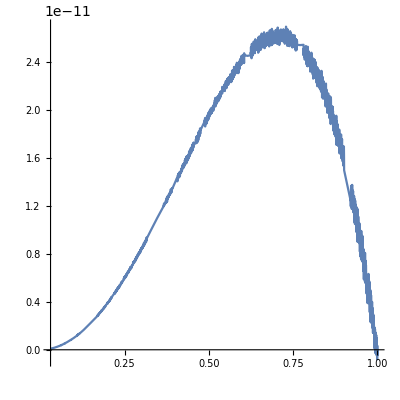

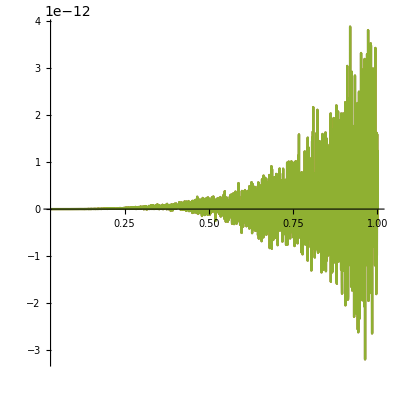

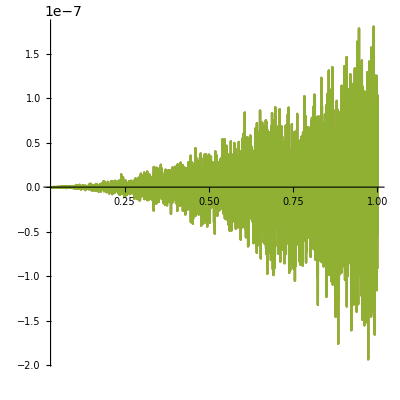

```mathematica
Plot[α[t]-t^2,{t,ηin,ETA0},WorkingPrecision->30,AspectRatio->1,PlotRange->All]
Plot[{γxx[t]-α[t]^2,γyy[t]-α[t]^2,γzz[t]-α[t]^2},{t,ηin,ETA0},WorkingPrecision->30,AspectRatio->1,PlotRange->All]
Plot[{kxx[t]-(-α'[t]),kyy[t]-(-α'[t]),kzz[t]-(-α'[t])},{t,ηin,ETA0},WorkingPrecision->30,AspectRatio->1,PlotRange->All]
```

```mathematica
αα[τ_]:=α[τ]
ββ[τ_]:=β/.Join[{η->τ},Table[X[[i]]-> X[[i]][τ],{i,1,Length[X]}]];
VV[η_]:=Table[V[[i]][η],{i,1,Length[X]}];
gg[τ_]:=γ/.Join[{η->τ},Table[X[[i]]-> X[[i]][τ],{i,1,Length[X]}]];
(*gg4[τ_]:=g4/.Join[{η->τ},Table[X[[i]]-> X[[i]][τ],{i,1,Length[X]}]];*)
nup[τ_]:=nu/.Join[{η->τ},Table[X[[i]]-> X[[i]][τ],{i,1,Length[X]}]];
ndown[τ_]:=nd/.Join[{η->τ},Table[X[[i]]-> X[[i]][τ],{i,1,Length[X]}]];

αlup[η_]:=(*EBG[η]*)αα[η] (nup[η]+Flatten[{0,VV[η]}]);
αldown[η_]:=(*EBG[η]*)αα[η](ndown[η]+Flatten[{0,gg[η].VV[η]}]);
g4[η_]:={{-(α[η])^2+ββ[η].ββ[η],ββ[η][[1]],ββ[η][[2]],ββ[η][[3]]},{ββ[η][[1]],γxx[η],γxy[η],γxz[η]},{ββ[η][[2]],γxy[η],γyy[η],γyz[η]},{ββ[η][[3]],γxz[η],γyz[η],γzz[η]}};
K4[η_]:={{0,0,0,0},{0,kxx[η],kxy[η],kxz[η]},{0,kxy[η],kyy[η],kyz[η]},{0,kxz[η],kyz[η],kzz[η]}};
```

### Initial conditions

The initial conditions can be given in two different ways:
1) directly specifying the values or
2) giving the initial direction v^2 and v^3 and use the function InitialConditions[] to compute v^1 such that the geodesic is null.

```mathematica
κ=SetPrecision[𝒱[(*A[ηin]^-2,A[ηin]^-2*)-1,1,π/4,π/4],70]
```

{-1.,0.5,0.5,0.7071067811865475244008443621048490392848359376884740365883398689953662}

```mathematica
(g4[η].κ.κ)/.η->ETA0
(g4[η].κ.κ)/.η->ηin
```

0.

3.6×10^-18

The four-velocity of the observer  in 3+1 decomposition is u^μ=Γ(n^μ+U^μ): in this case the homogeneity impose that every observer and source move together with the cosmic expansion. This implies that the observer is static with respect to the cosmic flow (no spatial velocity U^i=0) and that the Lorentz factor is Γ=1 (which follows from the normalization u^μ u_μ=-1)

```mathematica
U={0,0,0};
Γl=Sqrt[1/(1-γ.U.U)]
uu=Γl(nup[η]+Join[{0},U])

u[τ_]:=uu/.Join[{η->τ},Table[X[[i]]-> X[[i]][τ],{i,1,Length[X]}]];
u[ETA0]//N
u[ηin]//N
```

1

{1/(InterpolatingFunction[{{0.03012093555625838, 1.000000000000000}}, <>][η]),0,0,0}

{1.,0.,0.,0.}

{1102.21,0.,0.,0.}

The vector κ^μ must be expressed in 3+1 form κ^μ=E(n^μ+V^μ) where E=-κ^μ n_μ and V^μ=κ^μ/E-n^μ

```mathematica
ϵ=SetPrecision[-∑_(i=1)^4 κ[[i]]nd[[i]]/.{η->ETA0},30]
vi=SetPrecision[Table[(κ[[i]]/ϵ-nu[[i]])/.{η->ETA0},{i,1,4}],30]
```

-1.

{0,-0.5,-0.5,-0.707106781186547524400844362105}

```mathematica
substitution={η->ETA0,x->0,y->0,z->0,v2->vi[[3]],v3->vi[[4]]};
```

```mathematica
initialvel1=Flatten[InitialConditions[γ,substitution,V,param]]
initialBG=(*{x[ETA0]==0,y[ETA0]==0,v2[ETA0]==0,z[ETA0]==0,v3[ETA0]==0,v1[1]==-1}*)Flatten[Join[Table[(substitution[[i,1]][η]/.substitution[[1]])==substitution[[i,2]],{i,2,Length[substitution]}],{(V[[1]][η]/.substitution[[1]])==initialvel1[[1,2]](*-2.5 10^-4*)(*(V[[1]]/.initialvel1[[2]])*)}]]
E0BG=ϵ(*α/.η->ηin*)(*ϵ*)
initialenergy={Energy[[1]][ETA0]==ϵ,Energy[[2]][ETA0]==1}
```

{v1→-0.5,v1→0.5}

{x[1.]==0,y[1.]==0,z[1.]==0,v2[1.]==-0.5,v3[1.]==-0.707106781186547524400844362105,v1[1.]==-0.5}

-1.

{energy[1.]==-1.,λ[1.]==1}

### Solve the equations numerically, given the functions in the metric explicitly

```mathematica
AbsoluteTiming[With[{opts=SystemOptions[]},Internal`WithLocalSettings[SetSystemOptions["NDSolveOptions"->"DefaultSolveTimeConstraint"->40.],solgeodesic=Flatten[SolveGeodesic[geodBG,initialBG,X,V,param,η,ηin,ETA0,"SS",30,30,10,15]];,SetSystemOptions[opts]]]]
```

NDSolve::precw: The precision of the differential equation ({{«1»},{},{},{},{}}) is less than WorkingPrecision (30.).

SystemOptions::noset: The value of SystemOption PreemptiveCheckUseThreads cannot be modified.

{290.527,Null}

```mathematica
(*solenergy=Flatten[SolveEnergy[SetPrecision[enereqBG,100],SetPrecision[initialenergy,100],Energy,SetPrecision[solgeodesic,100],SetPrecision[param,100],η,SetPrecision[ηin,100],SetPrecision[ETA0,100],"SS",60,60,20,10]]*)
AbsoluteTiming[With[{opts=SystemOptions[]},Internal`WithLocalSettings[SetSystemOptions["NDSolveOptions"->"DefaultSolveTimeConstraint"->40.],solenergy=Flatten[SolveEnergy[enereqBG,initialenergy,Energy,solgeodesic,param,η,ηin,ETA0,"SS",30,30,10,10]];,SetSystemOptions[opts]]]]
```

SystemOptions::noset: The value of SystemOption PreemptiveCheckUseThreads cannot be modified.

{188.35,Null}

Test that the constraint conditions are satisfied for all the evolution

```mathematica
geodesic=Join[solgeodesic,solenergy];
```

```mathematica
Join[solgeodesic,solenergy]>>"Data_BGO/res_0.05/FLRWSolver_geodesicN_bisect_0p05.m"
```

```mathematica
geodesic=<<"Data_BGO/res_0.05/FLRWSolver_geodesicN_bisect_0p05.m";
```

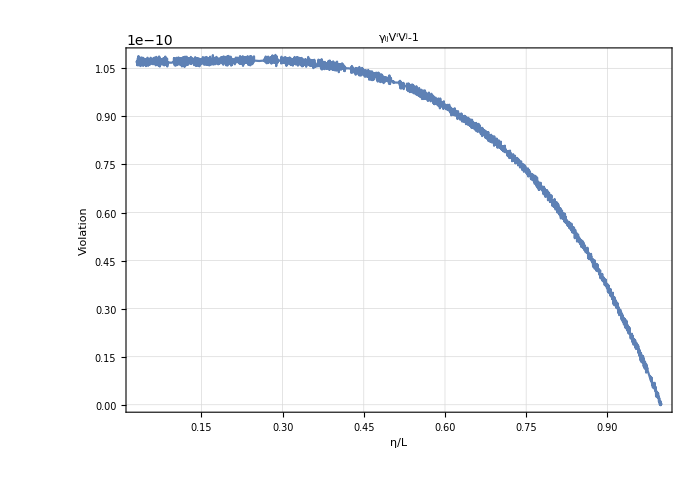

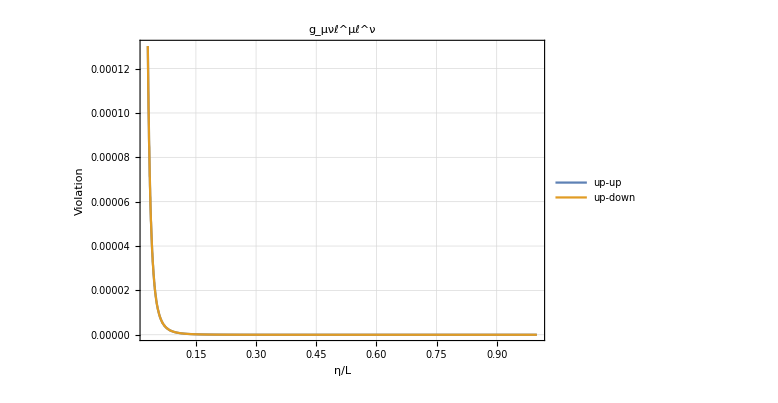

```mathematica
EBG[η_]:=energy[η]/.geodesic;
lup[η_]:=EBG[η](nup[η]+Flatten[{0,VV[η]}]);
ldown[η_]:=EBG[η](ndown[η]+Flatten[{0,gg[η].VV[η]}]);
titolo=Plot[Evaluate[{gg[η].VV[η].VV[η]-1}/.geodesic/.param], {η, ηin,ETA0},PlotRange->All,WorkingPrecision->60,AspectRatio->0.7,ImageSize->700,Evaluate[StandardPlotStyle[16,24,"Violation","η/L","γ_ijV^iV^j-1",{},{}]]]
Plot[Evaluate[{g4[η].lup[η].lup[η],lup[η].ldown[η]}/.geodesic/.param], {η, ηin,ETA0},PlotRange->Full,WorkingPrecision->60,AspectRatio->0.7,ImageSize->Large,Evaluate[StandardPlotStyle[16,24,"Violation","η/L","g_μνℓ^μℓ^ν",{"up-up","up-down"},{0.6,0.6}]]]
```

### Compute the redshift

The  redshift is defined as z+1==(g_μν u^μ ℓ^ν|_𝒮)/(g_μν u^μ ℓ^ν|_𝒪). 
In 3+1, decomposing u^μ==Γ(n^μ+U^μ) and ℓ^μ=ℰ(n^μ+V^μ), the redshift becomes: z+1==ℰ_𝒮/ℰ_𝒪(1-γ_ij V^i U^j|_𝒮)/(1-γ_ij V^i U^j|_𝒪)((1-γ_ij U^i U^j|_𝒮)/(1-γ_ij U^i U^j|_𝒪))^(1/2). In synchronous-comoving coordinates U^i==0 and the redshift simplifies to z+1==ℰ_𝒮/ℰ_𝒪

```mathematica
redshift[η_]:=EBG[η]/EBG[ETA0]-1(*A[ETA0]/A[η]-1*)
```

-Graphics-

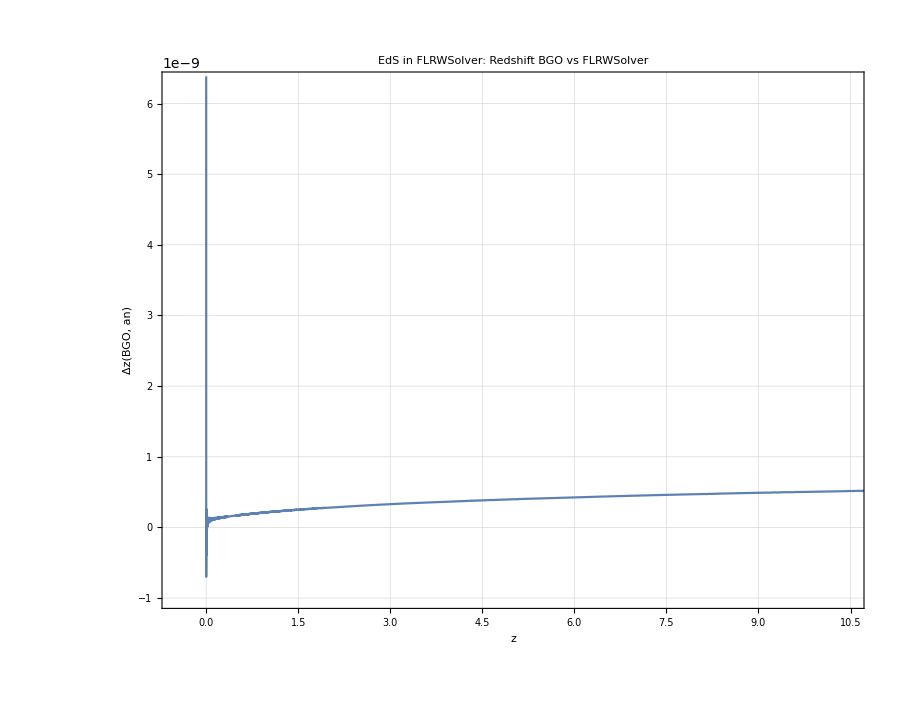

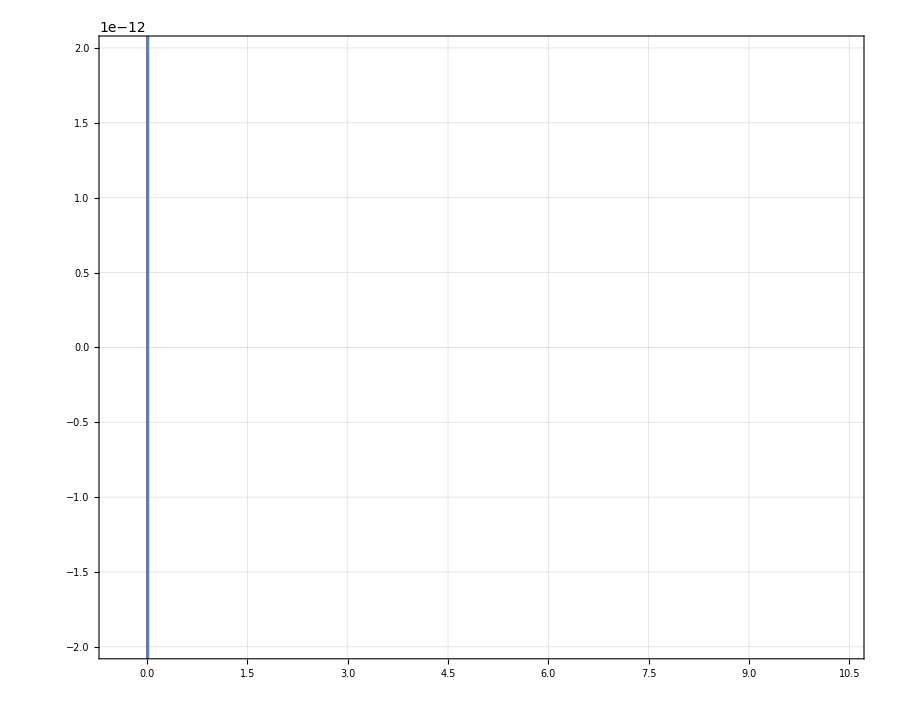

```mathematica
Graphics[{White,Rectangle[]}]

ParametricPlot[{redshift[η],  redshift[η]/(α[ETA0]/α[η]-1)-1},{η,ηin,ETA0},(*WorkingPrecision->40,*)ImageSize->900,AspectRatio->0.8,PlotRange->{{-0.5, 10.5},{-1 10^-9,6.3 10^-9}},Evaluate[StandardPlotStyle[18,24,"Δz(BGO, an)","z","EdS in FLRWSolver: Redshift BGO vs FLRWSolver",{},{}]]]
ParametricPlot[{redshift[η],  redshift[η]/(α[ETA0]/α[η]-1)-1},{η,ηin,ETA0},(*WorkingPrecision->40,*)ImageSize->900,AspectRatio->0.8,PlotRange->{{-0.5, 10.5},{-2 10^-12,2 10^-12}},Evaluate[StandardPlotStyle[18,24," "," "," ",{},{}]]]
```

```mathematica
tz10=t/.Solve[A[ETA0]/A[t]-1==10,t][[2]]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

0.301511344577764

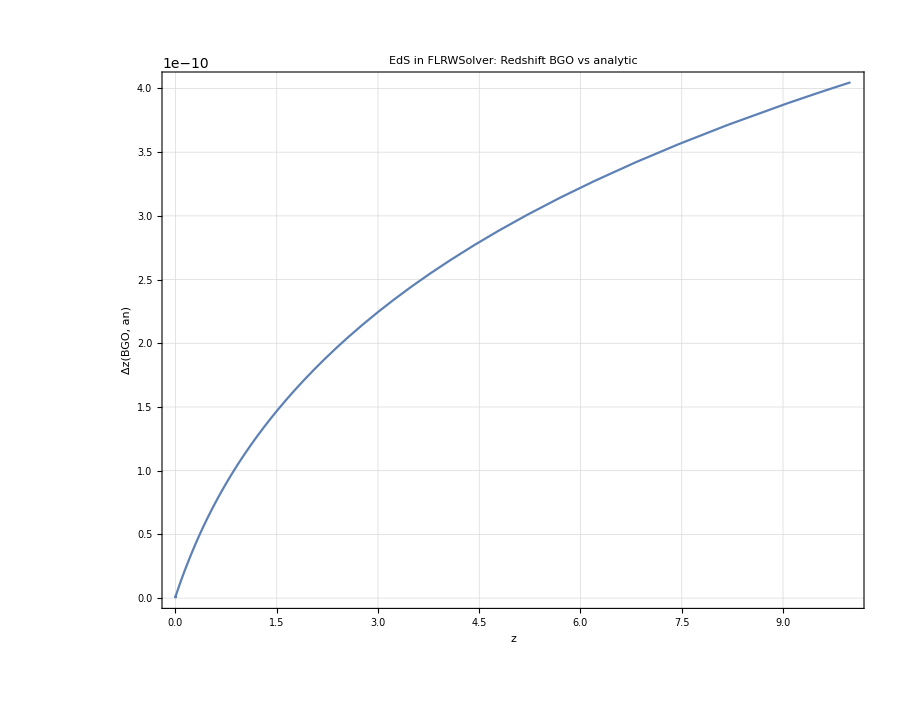

```mathematica
ParametricPlot[{redshift[η], ( redshift[η]/(A[ETA0]/A[η]-1)-1)},{η,tz10,ETA0},(*WorkingPrecision->40,*)ImageSize->900,AspectRatio->0.8,PlotRange->All,Evaluate[StandardPlotStyle[18,24,"Δz(BGO, an)","z","EdS in FLRWSolver: Redshift BGO vs analytic",{},{}]]]
```

#### Compute the null geodesic

```mathematica
trajectoryBG[η_]:=Flatten[{x[η] ,y[η] ,z[η] }/.geodesic/.param];
Show[ParametricPlot3D[trajectoryBG[η],{η,ηin,ETA0},PlotRange->All, ImageSize->700, ViewPoint->{0,0,Infinity}, AxesLabel->{"X/L","Y/L","Z/L"}]/.Line[x_]:>Sequence[Arrowheads[Table[.02,{100/10}]],Arrow@Line[x]] ]
```

-Graphics3D-

## Parallel transport of a frame

```mathematica
Clear[transport2,vecbcframe,soltrans2,soldeviation,solGDE,tot1,tot2,totl,totu,Cu,Cl,Cf1,Cf2,Pu,Pl,P1,P2,F,F0,EE,EE0,OPT,ξ,ξA,ξbc,Ξ,ξ4,DA,DAbc,DAsolGDE,JMAP,frame,frame0]
```

```mathematica
frame0={fu0,f10,f20,fl0};
frame={{fu1,fu2,fu3},{f11,f12,f13},{f21,f22,f23},{fl1,fl2,fl3}};
```

### set-up the initial conditions for the SNF

Let us start setting the four-velocity of the observer that in 3+1 decomposition is u^μ=Γ(n^μ+U^μ): in this case the homogeneity impose that every observer and source move together with the cosmic expansion. This implies that the observer is static with respect to the cosmic flow (no spatial velocity U^i=0) and that the Lorentz factor is Γ=1 (which follows from the normalization u^μ u_μ=-1)

```mathematica
g4[ETA0].u[ETA0].lup[ETA0]/.Join[geodesic,param]
g4[η].u[η].u[η]/.η->ETA0
-1/A[ETA0]^2
```

1.

-1

-1.

Assuming f_1^μ=OverTilde[f_1]^μ+A u^μ+B k^μ and f_2^μ=OverTilde[f_2]^μ+C u^μ+D k^μ+E f_1^μ, the relations between the vector of the SNF can be used to determine the constants A, B, C, D and E.

```mathematica
p1={0,0,1,0};
p2={0,0,0,1};
```

```mathematica
𝒻1=Re[(p1-(g4[t].p1.lup[t])/(g4[t].lup[t].u[t])u[t]-1/(g4[t].lup[t].u[t])((g4[t].p1.lup[t])/(g4[t].lup[t].u[t])+g4[t].p1.u[t])lup[t])/.Join[geodesic,param]/.t->ETA0]
s1=𝒻1/Sqrt[g4[ETA0].𝒻1.𝒻1]
```

{0,-0.25,0.75,-0.35355339059327}

{0,-0.28867513459481,0.86602540378444,-0.40824829046386}

```mathematica
𝒻2=Re[(p2-(g4[t].p2.lup[t])/(g4[t].lup[t].u[t])u[t]-1/(g4[t].lup[t].u[t])((g4[t].p2.lup[t])/(g4[t].lup[t].u[t])+g4[t].p2.u[t])lup[t]-(g4[t].p2.s1)s1)/.Join[geodesic,param]/.t->ETA0]
s2=𝒻2/Sqrt[g4[ETA0].𝒻2.𝒻2]
```

{0,-0.47140452079103,0.,0.3333333333333}

{0,-0.8164965809277,0.,0.5773502691896}

Initial conditions for the SN frame

```mathematica
(*u={1/A[η],0,0,0}=> fu0=α u^0 , fu^i=u^i+fu0 β^i/α;
f1=s1=> f10=α s1^0, f1^i=s1^i+f10 β^i/α;
f2=s2=> f20=α s2^0, f2^i=s2^i+f20 β^i/α;
ENW[η_]:=First[Evaluate[energy[η]/.enerNW]];
k[η_]:= Evaluate[(ENW[η](nup[η]+Flatten[{0,VV[η]}]))/.Join[geodesicNW]];
k => fl0=α k^0, fl^i=k^i+fl0 β^i/α ;*)
```

```mathematica
fu0in=(*Cu=*)SetPrecision[((-ndown[t].u[t])/.geodesic/.param)/.t->ETA0,prec];
fuin=(*fu^μ=*)SetPrecision[((u[t]-(-ndown[t].u[t]) nup[t])/.geodesic/.param)/.t->ETA0,prec];

f10in=(*C1=*)SetPrecision[((-ndown[t].s1)/.geodesic/.param)/.t->ETA0,prec];
f1in=(*Subscript[f, 1]^μ=*)SetPrecision[((s1-(-ndown[t].s1) nup[t])/.geodesic/.param)/.t->ETA0,prec];

f20in=(*C2=*)SetPrecision[((-ndown[t].s2)/.geodesic/.param)/.t->ETA0,prec];
f2in=(*Subscript[f, 2]^μ=*)SetPrecision[((s2-(-ndown[t].s2) nup[t])/.geodesic/.param)/.t->ETA0,prec];

fl0in=(*Ck=*)SetPrecision[((-ndown[t].lup[t])/.geodesic/.param)/.t->ETA0,prec];(*SetPrecision[A[ηin],∞];*)
flin=(*fk^μ=*)SetPrecision[((lup[t]-(fl0in) nup[t])/.geodesic/.param)/.t->ETA0,prec];
```

### Parallel transport the SNF

```mathematica
initialframeBG={{fu0[ETA0]==fu0in,fu1[ETA0]==fuin[[2]],fu2[ETA0]==fuin[[3]] ,fu3[ETA0]==fuin[[4]]},{f10[ETA0]==f10in,f11[ETA0]==f1in[[2]],f12[ETA0]==f1in[[3]],f13[ETA0]==f1in[[4]]},{f20[ETA0]==f20in,f21[ETA0]==f2in[[2]],f22[ETA0]==f2in[[3]],f23[ETA0]==f2in[[4]] },{fl0[ETA0]==fl0in,fl1[ETA0]==flin[[2]],fl2[ETA0]==flin[[3]],fl3[ETA0]==flin[[4]]}};
```

```mathematica
AbsoluteTiming[With[{opts=SystemOptions[]},Internal`WithLocalSettings[SetSystemOptions["NDSolveOptions"->"DefaultSolveTimeConstraint"->40.],soltransBG=Flatten[PTransportedFrame[γ,𝒦,α[η],β,geodesic,initialframeBG,frame,frame0,param,η,ηin,ETA0,"SS",30,30,10,15]];,SetSystemOptions[opts]]]]
```

NDSolve::precw: The precision of the differential equation ({{«1»},{},{},{},{}}) is less than WorkingPrecision (30.).

NDSolve::precw: The precision of the differential equation ({«1»}) is less than WorkingPrecision (30.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

SystemOptions::noset: The value of SystemOption PreemptiveCheckUseThreads cannot be modified.

{7635.62,Null}

```mathematica
totBG=Flatten[Join[Flatten[soltransBG],geodesic]];
```

```mathematica
Cu[η_]:=fu0[η];
Cf1[η_]:=f10[η];
Cf2[η_]:=f20[η];
Cl[η_]:=fl0[η];
Pu[η_]:={fu1[η],fu2[η],fu3[η]};
P1[η_]:={f11[η],f12[η],f13[η]};
P2[η_]:={f21[η],f22[η],f23[η]};
Pl[η_]:={fl1[η],fl2[η],fl3[η]};
```

```mathematica
Show[ParametricPlot3D[trajectoryBG[η],{η,ηin,ETA0},PlotRange->All]/.Line[x_]:>Sequence[Arrowheads[Table[.02,{100/10}]],Arrow@Line[x]] ,Graphics3D[{(*{Red,Arrowheads[0.02],Table[Arrow[{trajectoryBG[η],(trajectoryBG[η]+(Pu[η]/.totBG))}],{η,ηin,ETA0,0.05}]},*){Green,Arrowheads[0.02],Table[Arrow[{trajectoryBG[η],(trajectoryBG[η]+α[η](P1[η]/.totBG))}],{η,ηin,ETA0,1}]},{Blue,Arrowheads[0.02],Table[Arrow[{trajectoryBG[η],(trajectoryBG[η]+α[η](P2[η]/.totBG))}],{η,ηin,ETA0,1}]}(*,{Black,Arrowheads[0.02],Table[Arrow[{trajectoryBG[η],(trajectoryBG[η]+(Pl[η]/.totBG))}],{η,ηin,ETA0,0.05}]}*)}],Graphics3D[Sphere[{0,0,0},0.05]] , ImageSize->700,ViewPoint->{0,100,10},AxesLabel->{x,y,z},AxesStyle->Directive[Red,12]]
```

-Graphics3D-

```mathematica
totBG=<<"Data_BGO/res_0.05/FLRWSolver_ptSNFN_bisect_0p05.m";
```

### Define the induced metric of the SNF “h”

```mathematica
Clear[F,F0,EE,EE0,Q,h]
```

```mathematica
(*((((gg4[ETA0].(Evaluate[Cu[ETA0]nup[ETA0]+Flatten[{0, Pu[ETA0]}]]).(Evaluate[Cl[ETA0]nup[ETA0]+Flatten[{0, Pl[ETA0]}]]))))/.totBG/.param)*)Q=Re[((g4[ETA0].(Evaluate[Cu[ETA0]nup[ETA0]+Flatten[{0, Pu[ETA0]}]]).(Evaluate[Cl[ETA0]nup[ETA0]+Flatten[{0, Pl[ETA0]}]]))/.totBG/.param)];
h={{-1,0,0,Q},{0,1,0,0},{0,0,1,0},{Q,0,0,0}};
Ih=Inverse[h];
```

```mathematica
F[t_]:={{Pu[t][[1]],P1[t][[1]],P2[t][[1]],Pl[t][[1]]},{Pu[t][[2]],P1[t][[2]],P2[t][[2]],Pl[t][[2]]},{Pu[t][[3]],P1[t][[3]],P2[t][[3]],Pl[t][[3]]}};
F0[t_]:={Cu[t],Cf1[t],Cf2[t],Cl[t]};
```

```mathematica
totBG>>"Data_BGO/res_0.05/FLRWSolver_ptSNFN_bisect_0p05.m"
```

#### Check SNF

-0.57735026630287451474075727918495279118

```mathematica
(g4[t].u[t].s1)/.Join[geodesic,param]/.t->ηin
(g4[t].u[t].s2)/.Join[geodesic,param]/.t->ηin
(g4[t].lup[t].s1)/.Join[geodesic,param]/.t->ηin
(g4[t].lup[t].s2)/.Join[geodesic,param]/.t->ηin
(g4[t].s1.s2)/.Join[geodesic,param]/.t->ηin
(g4[t].s1.s1)/.Join[geodesic,param]/.t->ηin
(g4[t].s2.s2)/.Join[geodesic,param]/.t->ηin
(g4[t].lup[t].u[t])/.Join[geodesic,param]/.t->ηin
(g4[t].u[t].u[t])/.Join[geodesic,param]/.t->ηin
(g4[t].lup[t].lup[t])/.Join[geodesic,param]/.t->ηin
```

0

0

0.

0.

0.

8.231402299151×10^-7

8.231402299151×10^-7

1102.20680173525

-1

0.0001302

```mathematica
(g4[t].u[t].s1)/.Join[geodesic,param]/.t->ETA0
(g4[t].u[t].s2)/.Join[geodesic,param]/.t->ETA0
(g4[t].lup[t].s1)/.Join[geodesic,param]/.t->ETA0
(g4[t].lup[t].s2)/.Join[geodesic,param]/.t->ETA0
(g4[t].s1.s2)/.Join[geodesic,param]/.t->ETA0
(g4[t].s1.s1)/.Join[geodesic,param]/.t->ETA0
(g4[t].s2.s2)/.Join[geodesic,param]/.t->ETA0
(g4[t].lup[t].u[t])/.Join[geodesic,param]/.t->ETA0
(g4[t].u[t].u[t])/.Join[geodesic,param]/.t->ETA0
(g4[t].lup[t].lup[t])/.Join[geodesic,param]/.t->ETA0
```

0

0

0.

0.

0.

1.

1.

1.

-1

0.

```mathematica
Check of the relations: u^μ Subscript[u, μ]=-1,f1^μ Subscript[f1, μ]=1,f2^μ Subscript[f2, μ]=1,k^μ Subscript[k, μ]=0
```

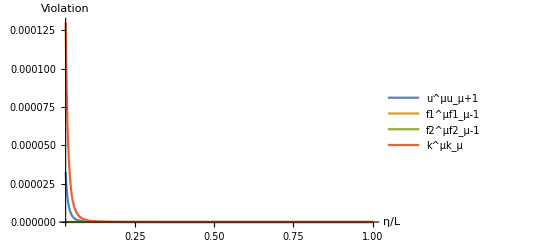

```mathematica
Plot[{(g4[η].(Evaluate[Cu[η]nup[η]+Flatten[{0, Pu[η]}]]).(Evaluate[Cu[η]nup[η]+Flatten[{0, Pu[η]}]])+1)/.totBG/.param,(g4[η].(Evaluate[Cf1[η]nup[η]+Flatten[{0, P1[η]}]]).(Evaluate[Cf1[η]nup[η]+Flatten[{0, P1[η]}]])-1)/.totBG/.param,(g4[η].(Evaluate[Cf2[η]nup[η]+Flatten[{0, P2[η]}]]).(Evaluate[Cf2[η]nup[η]+Flatten[{0, P2[η]}]])-1)/.totBG/.param,(g4[η].(Evaluate[Cl[η]nup[η]+Flatten[{0, Pl[η]}]]).(Evaluate[Cl[η]nup[η]+Flatten[{0, Pl[η]}]]))/.totBG/.param},{η,ηin,ETA0},AxesLabel->{"η/L","Violation"},PlotLegends->{"u^μu_μ+1","f1^μf1_μ-1","f2^μf2_μ-1","k^μk_μ"},PlotRange->All(*{-10^-6,10^-6}*),WorkingPrecision->30]
```

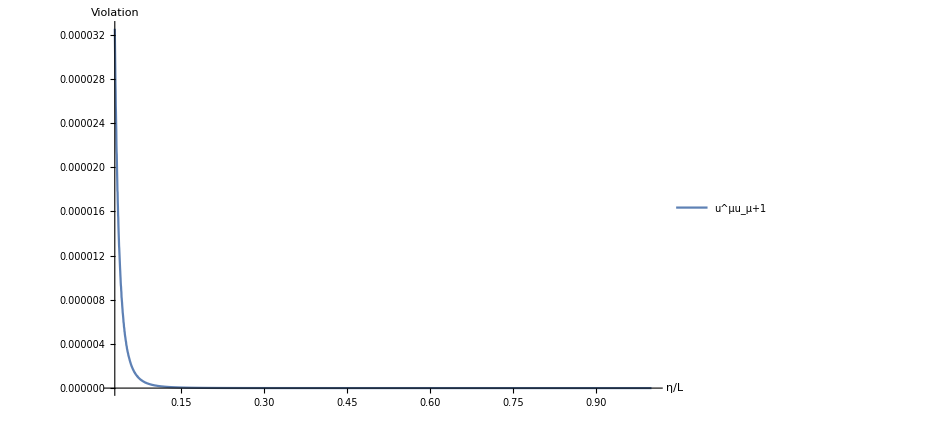

```mathematica
Plot[(g4[η].(Evaluate[Cu[η]nup[η]+Flatten[{0, Pu[η]}]]).(Evaluate[Cu[η]nup[η]+Flatten[{0, Pu[η]}]])+1)/.totBG/.param,{η,ηin,ETA0},AxesLabel->{"η/L","Violation"},PlotLegends->{"u^μu_μ+1","f1^μf1_μ-1","f2^μf2_μ-1","k^μk_μ"},PlotRange->Full,WorkingPrecision->30,ImageSize->700]
```

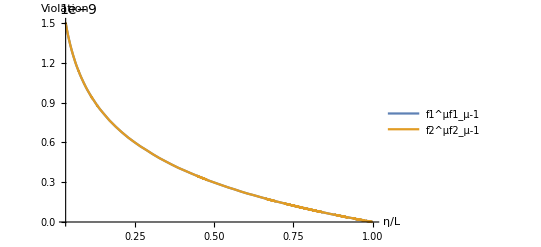

```mathematica
Plot[{(g4[η].(Evaluate[Cf1[η]nup[η]+Flatten[{0, P1[η]}]]).(Evaluate[Cf1[η]nup[η]+Flatten[{0, P1[η]}]])-1)/.totBG/.param,(g4[η].(Evaluate[Cf2[η]nup[η]+Flatten[{0, P2[η]}]]).(Evaluate[Cf2[η]nup[η]+Flatten[{0, P2[η]}]])-1)/.totBG/.param},{η,ηin,ETA0},AxesLabel->{"η/L","Violation"},PlotLegends->{"f1^μf1_μ-1","f2^μf2_μ-1"},PlotRange->All(*{-10^-6,10^-6}*),WorkingPrecision->30]
```

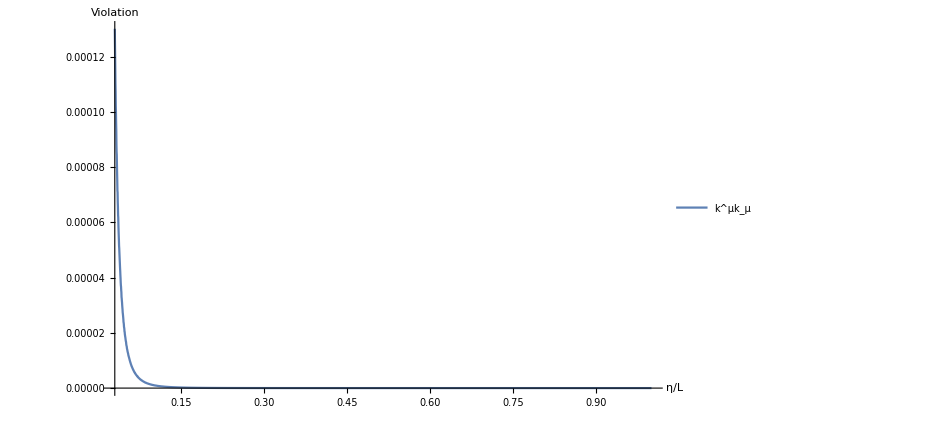

```mathematica
Plot[(g4[η].(Evaluate[Cl[η]nup[η]+Flatten[{0, Pl[η]}]]).(Evaluate[Cl[η]nup[η]+Flatten[{0, Pl[η]}]]))/.totBG/.param,{η,ηin,ETA0},AxesLabel->{"η/L","Violation"},PlotLegends->{"k^μk_μ"},PlotRange->Full,WorkingPrecision->30,ImageSize->700]
```

```mathematica
Check of the relations: u^μ Subscript[f1, μ]=0,u^μ Subscript[f2, μ]=0,k^μ Subscript[f1, μ]=0,k^μ Subscript[f2, μ]=0
```

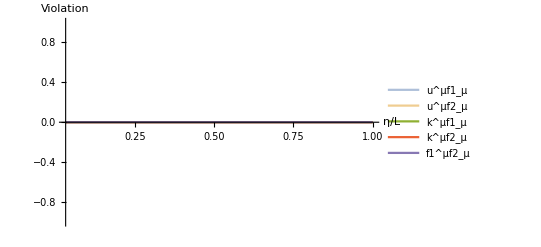

```mathematica
Plot[{(g4[η].(Evaluate[Cu[η]nup[η]+Flatten[{0, Pu[η]}]]).(Evaluate[Cf1[η]nup[η]+Flatten[{0, P1[η]}]]))/.totBG/.param,(g4[η].(Evaluate[Cu[η]nup[η]+Flatten[{0, Pu[η]}]]).(Evaluate[Cf2[η]nup[η]+Flatten[{0, P2[η]}]]))/.totBG/.param,(g4[η].(Evaluate[Cl[η]nup[η]+Flatten[{0, Pl[η]}]]).(Evaluate[Cf1[η]nup[η]+Flatten[{0, P1[η]}]]))/.totBG/.param,(g4[η].(Evaluate[Cl[η]nup[η]+Flatten[{0, Pl[η]}]]).(Evaluate[Cf2[η]nup[η]+Flatten[{0, P2[η]}]]))/.totBG/.param,(g4[η].(Evaluate[Cf1[η]nup[η]+Flatten[{0, P1[η]}]]).(Evaluate[Cf2[η]nup[η]+Flatten[{0, P2[η]}]]))/.totBG/.param},{η,ηin,ETA0},AxesLabel->{"η/L","Violation"},PlotLegends->{"u^μf1_μ","u^μf2_μ","k^μf1_μ","k^μf2_μ","f1^μf2_μ"},PlotRange->All(*{{tin,t0},{-10^-8,10^-8}}*),PlotStyle->{Opacity[.5],Opacity[.5],Thick,Thick,Thick},WorkingPrecision->30]
```

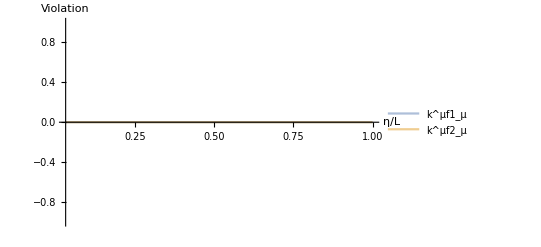

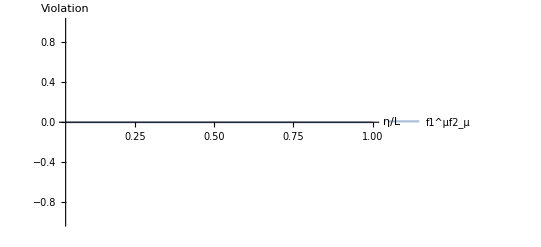

```mathematica
Plot[{(g4[η].(Evaluate[Cl[η]nup[η]+Flatten[{0, Pl[η]}]]).(Evaluate[Cf1[η]nup[η]+Flatten[{0, P1[η]}]]))/.totBG/.param,(g4[η].(Evaluate[Cl[η]nup[η]+Flatten[{0, Pl[η]}]]).(Evaluate[Cf2[η]nup[η]+Flatten[{0, P2[η]}]]))/.totBG/.param},{η,ηin,ETA0},AxesLabel->{"η/L","Violation"},PlotLegends->{"k^μf1_μ","k^μf2_μ"},PlotRange->All(*{{tin,t0},{-10^-8,10^-8}}*),PlotStyle->{Opacity[.5],Opacity[.5],Thick,Thick,Thick},WorkingPrecision->30]
Plot[{(g4[η].(Evaluate[Cf1[η]nup[η]+Flatten[{0, P1[η]}]]).(Evaluate[Cf2[η]nup[η]+Flatten[{0, P2[η]}]]))/.totBG/.param},{η,ηin,ETA0},AxesLabel->{"η/L","Violation"},PlotLegends->{"f1^μf2_μ"},PlotRange->All(*{{tin,t0},{-10^-8,10^-8}}*),PlotStyle->{Opacity[.5],Opacity[.5],Thick,Thick,Thick},WorkingPrecision->30]
```

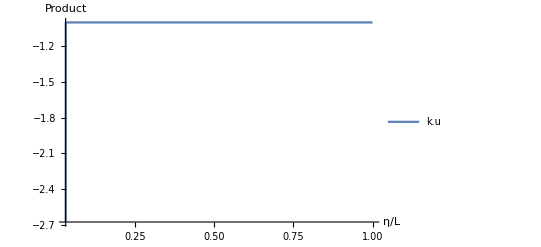

```mathematica
Plot[((((g4[η].(Evaluate[Cu[η]nup[η]+Flatten[{0, Pu[η]}]]).(Evaluate[Cl[η]nup[η]+Flatten[{0, Pl[η]}]])))/((g4[ηin].(Evaluate[Cu[ηin]nup[ηin]+Flatten[{0, Pu[ηin]}]]).(Evaluate[Cl[ηin]nup[ηin]+Flatten[{0, Pl[ηin]}]]))))/.totBG/.param)-1,{η,ηin,ETA0},AxesLabel->{"η/L","Product"},PlotLegends->{"k.u"},PlotRange->All,WorkingPrecision->30]
```

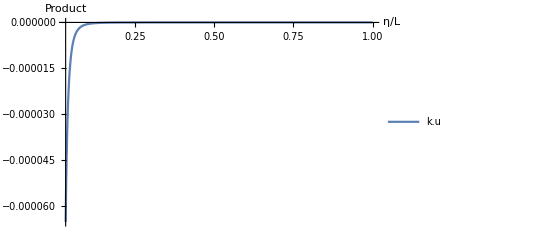

```mathematica
Plot[((((g4[η].(Evaluate[Cu[η]nup[η]+Flatten[{0, Pu[η]}]]).(lup[η]))/Q)-1)/.totBG/.param),{η,ηin,ETA0},AxesLabel->{"η/L","Product"},PlotLegends->{"k.u"},PlotRange->All,WorkingPrecision->30]
```

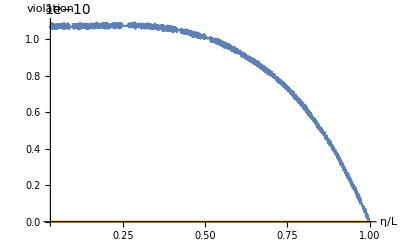

```mathematica
Plot[Evaluate[{(gg[η].VV[η].VV[η]-1),0( gg[η].Pl[η].Pl[η]-Cl[η]^2) (*( (gg[η].Pl[η].Pl[η]-Cl[η]^2)/Cl[η]^2) *)}/.totBG/.param], {η, ηin,ETA0},PlotRange->Full,AxesLabel->{Style["η/L",Large],Style["violation",Large]}]
```

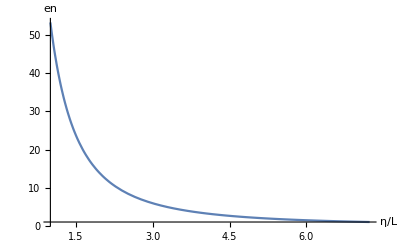

```mathematica
Plot[(A[ηin]^2/A[η]-Cl[η])/.totBG,{η, ηin,ETA0},PlotRange->Full,AxesLabel->{Style["η/L",Large],Style["en",Large]}]
```

## Optical Tidal Matrix

```mathematica
Clear[α,γ,𝒦,γxx,γxy,γxz,γyy,γyz,γzz,kxx,kxy,kxz,kyy,kyz,kzz]
```

```mathematica
γ={{γxx[η],γxy[η],γxz[η]},{γxy[η],γyy[η],γyz[η]},{γxz[η],γyz[η],γzz[η]}};

𝒦={{kxx[η],kxy[η],kxz[η]},{kxy[η],kyy[η],kyz[η]},{kxz[η],kyz[η],kzz[η]}};
```

```mathematica
Timing[OPT=OpticalTidalMatrix[X,V,frame,frame0,Q,γ,𝒦,α[η],β,η];]
```

{13.6366,Null}

```mathematica
OPT//MatrixForm
```

(0 | 0 | 0 | 0
f12[η] fu2[η] (kxy[η]^2-kxx[η] kyy[η]) v1[η]^2+f13[η] fu2[η] (kxy[η] kxz[η]-kxx[η] kyz[η]) v1[η]^2+f12[η] fu3[η] (kxy[η] kxz[η]-kxx[η] kyz[η]) v1[η]^2+f13[η] fu3[η] (kxz[η]^2-kxx[η] kzz[η]) v1[η]^2+f12[η] fu1[η] (-kxy[η]^2+kxx[η] kyy[η]) v1[η] v2[η]+f11[η] fu2[η] (-kxy[η]^2+kxx[η] kyy[η]) v1[η] v2[η]+f13[η] fu1[η] (-kxy[η] kxz[η]+kxx[η] kyz[η]) v1[η] v2[η]+f11[η] fu3[η] (-kxy[η] kxz[η]+kxx[η] kyz[η]) v1[η] v2[η]+f13[η] fu2[η] (kxz[η] kyy[η]-kxy[η] kyz[η]) v1[η] v2[η]+f12[η] fu3[η] (kxz[η] kyy[η]-kxy[η] kyz[η]) v1[η] v2[η]+2 f13[η] fu3[η] (kxz[η] kyz[η]-kxy[η] kzz[η]) v1[η] v2[η]+f11[η] fu1[η] (kxy[η]^2-kxx[η] kyy[η]) v2[η]^2+f13[η] fu1[η] (-kxz[η] kyy[η]+kxy[η] kyz[η]) v2[η]^2+f11[η] fu3[η] (-kxz[η] kyy[η]+kxy[η] kyz[η]) v2[η]^2+f13[η] fu3[η] (kyz[η]^2-kyy[η] kzz[η]) v2[η]^2+f12[η] fu1[η] (-kxy[η] kxz[η]+kxx[η] kyz[η]) v1[η] v3[η]+f11[η] fu2[η] (-kxy[η] kxz[η]+kxx[η] kyz[η]) v1[η] v3[η]+2 f12[η] fu2[η] (-kxz[η] kyy[η]+kxy[η] kyz[η]) v1[η] v3[η]+f13[η] fu1[η] (-kxz[η]^2+kxx[η] kzz[η]) v1[η] v3[η]+f11[η] fu3[η] (-kxz[η]^2+kxx[η] kzz[η]) v1[η] v3[η]+f13[η] fu2[η] (-kxz[η] kyz[η]+kxy[η] kzz[η]) v1[η] v3[η]+f12[η] fu3[η] (-kxz[η] kyz[η]+kxy[η] kzz[η]) v1[η] v3[η]+2 f11[η] fu1[η] (kxy[η] kxz[η]-kxx[η] kyz[η]) v2[η] v3[η]+f12[η] fu1[η] (kxz[η] kyy[η]-kxy[η] kyz[η]) v2[η] v3[η]+f11[η] fu2[η] (kxz[η] kyy[η]-kxy[η] kyz[η]) v2[η] v3[η]+f13[η] fu1[η] (-kxz[η] kyz[η]+kxy[η] kzz[η]) v2[η] v3[η]+f11[η] fu3[η] (-kxz[η] kyz[η]+kxy[η] kzz[η]) v2[η] v3[η]+f13[η] fu2[η] (-kyz[η]^2+kyy[η] kzz[η]) v2[η] v3[η]+f12[η] fu3[η] (-kyz[η]^2+kyy[η] kzz[η]) v2[η] v3[η]+f11[η] fu1[η] (kxz[η]^2-kxx[η] kzz[η]) v3[η]^2+f12[η] fu1[η] (kxz[η] kyz[η]-kxy[η] kzz[η]) v3[η]^2+f11[η] fu2[η] (kxz[η] kyz[η]-kxy[η] kzz[η]) v3[η]^2+f12[η] fu2[η] (kyz[η]^2-kyy[η] kzz[η]) v3[η]^2+((f11[η]-f10[η] v1[η]) (-fu1[η]+fu0[η] v1[η]) (kxz[η]^2 α[η] (γxy[η]^2-γxx[η] γyy[η])+kxx[η]^2 α[η] γyz[η]^2-2 kxz[η] α[η] (kxy[η] (γxy[η] γxz[η]-γxx[η] γyz[η])+kxx[η] (-γxz[η] γyy[η]+γxy[η] γyz[η]))-kxx[η]^2 α[η] γyy[η] γzz[η]+kxy[η]^2 α[η] (γxz[η]^2-γxx[η] γzz[η])+2 kxx[η] kxy[η] α[η] (-γxz[η] γyz[η]+γxy[η] γzz[η])+γxz[η]^2 γyy[η] kxx'[η]-2 γxy[η] γxz[η] γyz[η] kxx'[η]+γxx[η] γyz[η]^2 kxx'[η]+γxy[η]^2 γzz[η] kxx'[η]-γxx[η] γyy[η] γzz[η] kxx'[η])+(f12[η] (-fu1[η]+fu0[η] v1[η])+f10[η] v1[η] (fu2[η]-fu0[η] v2[η])) (kxx[η] kyz[η] α[η] γxz[η] γyy[η]-kxx[η] kyz[η] α[η] γxy[η] γyz[η]-kxx[η] kyy[η] α[η] γxz[η] γyz[η]+kxz[η] α[η] (kyz[η] (γxy[η]^2-γxx[η] γyy[η])+kyy[η] (-γxy[η] γxz[η]+γxx[η] γyz[η])+kxy[η] (γxz[η] γyy[η]-γxy[η] γyz[η]))+kxx[η] kyy[η] α[η] γxy[η] γzz[η]+kxy[η]^2 α[η] (-γxz[η] γyz[η]+γxy[η] γzz[η])+kxy[η] α[η] (kyz[η] (-γxy[η] γxz[η]+γxx[η] γyz[η])+kyy[η] (γxz[η]^2-γxx[η] γzz[η])+kxx[η] (γyz[η]^2-γyy[η] γzz[η]))+γxz[η]^2 γyy[η] kxy'[η]-2 γxy[η] γxz[η] γyz[η] kxy'[η]+γxx[η] γyz[η]^2 kxy'[η]+γxy[η]^2 γzz[η] kxy'[η]-γxx[η] γyy[η] γzz[η] kxy'[η])+(f10[η] (fu1[η]-fu0[η] v1[η]) v2[η]+f11[η] (-fu2[η]+fu0[η] v2[η])) (kxx[η] kyz[η] α[η] γxz[η] γyy[η]-kxx[η] kyz[η] α[η] γxy[η] γyz[η]-kxx[η] kyy[η] α[η] γxz[η] γyz[η]+kxz[η] α[η] (kyz[η] (γxy[η]^2-γxx[η] γyy[η])+kyy[η] (-γxy[η] γxz[η]+γxx[η] γyz[η])+kxy[η] (γxz[η] γyy[η]-γxy[η] γyz[η]))+kxx[η] kyy[η] α[η] γxy[η] γzz[η]+kxy[η]^2 α[η] (-γxz[η] γyz[η]+γxy[η] γzz[η])+kxy[η] α[η] (kyz[η] (-γxy[η] γxz[η]+γxx[η] γyz[η])+kyy[η] (γxz[η]^2-γxx[η] γzz[η])+kxx[η] (γyz[η]^2-γyy[η] γzz[η]))+γxz[η]^2 γyy[η] kxy'[η]-2 γxy[η] γxz[η] γyz[η] kxy'[η]+γxx[η] γyz[η]^2 kxy'[η]+γxy[η]^2 γzz[η] kxy'[η]-γxx[η] γyy[η] γzz[η] kxy'[η])+(f13[η] (-fu1[η]+fu0[η] v1[η])+f10[η] v1[η] (fu3[η]-fu0[η] v3[η])) (kxx[η] kzz[η] α[η] γxz[η] γyy[η]-kxx[η] kzz[η] α[η] γxy[η] γyz[η]-kxx[η] kyz[η] α[η] γxz[η] γyz[η]+kxz[η]^2 α[η] (γxz[η] γyy[η]-γxy[η] γyz[η])+kxx[η] kyz[η] α[η] γxy[η] γzz[η]+kxz[η] α[η] (-kyz[η] γxy[η] γxz[η]+kzz[η] (γxy[η]^2-γxx[η] γyy[η])+kyz[η] γxx[η] γyz[η]-kxy[η] γxz[η] γyz[η]+kxx[η] γyz[η]^2+kxy[η] γxy[η] γzz[η]-kxx[η] γyy[η] γzz[η])+kxy[η] α[η] (kzz[η] (-γxy[η] γxz[η]+γxx[η] γyz[η])+kyz[η] (γxz[η]^2-γxx[η] γzz[η]))+γxz[η]^2 γyy[η] kxz'[η]-2 γxy[η] γxz[η] γyz[η] kxz'[η]+γxx[η] γyz[η]^2 kxz'[η]+γxy[η]^2 γzz[η] kxz'[η]-γxx[η] γyy[η] γzz[η] kxz'[η])+(f10[η] (fu1[η]-fu0[η] v1[η]) v3[η]+f11[η] (-fu3[η]+fu0[η] v3[η])) (kxx[η] kzz[η] α[η] γxz[η] γyy[η]-kxx[η] kzz[η] α[η] γxy[η] γyz[η]-kxx[η] kyz[η] α[η] γxz[η] γyz[η]+kxz[η]^2 α[η] (γxz[η] γyy[η]-γxy[η] γyz[η])+kxx[η] kyz[η] α[η] γxy[η] γzz[η]+kxz[η] α[η] (-kyz[η] γxy[η] γxz[η]+kzz[η] (γxy[η]^2-γxx[η] γyy[η])+kyz[η] γxx[η] γyz[η]-kxy[η] γxz[η] γyz[η]+kxx[η] γyz[η]^2+kxy[η] γxy[η] γzz[η]-kxx[η] γyy[η] γzz[η])+kxy[η] α[η] (kzz[η] (-γxy[η] γxz[η]+γxx[η] γyz[η])+kyz[η] (γxz[η]^2-γxx[η] γzz[η]))+γxz[η]^2 γyy[η] kxz'[η]-2 γxy[η] γxz[η] γyz[η] kxz'[η]+γxx[η] γyz[η]^2 kxz'[η]+γxy[η]^2 γzz[η] kxz'[η]-γxx[η] γyy[η] γzz[η] kxz'[η])+(f12[η]-f10[η] v2[η]) (-fu2[η]+fu0[η] v2[η]) (kyz[η]^2 α[η] (γxy[η]^2-γxx[η] γyy[η])+kxy[η]^2 α[η] γyz[η]^2-2 kyz[η] α[η] (kyy[η] (γxy[η] γxz[η]-γxx[η] γyz[η])+kxy[η] (-γxz[η] γyy[η]+γxy[η] γyz[η]))-kxy[η]^2 α[η] γyy[η] γzz[η]+kyy[η]^2 α[η] (γxz[η]^2-γxx[η] γzz[η])+2 kxy[η] kyy[η] α[η] (-γxz[η] γyz[η]+γxy[η] γzz[η])+γxz[η]^2 γyy[η] kyy'[η]-2 γxy[η] γxz[η] γyz[η] kyy'[η]+γxx[η] γyz[η]^2 kyy'[η]+γxy[η]^2 γzz[η] kyy'[η]-γxx[η] γyy[η] γzz[η] kyy'[η])+(f13[η] (-fu2[η]+fu0[η] v2[η])+f10[η] v2[η] (fu3[η]-fu0[η] v3[η])) (kxy[η] kzz[η] α[η] γxz[η] γyy[η]-kxy[η] kzz[η] α[η] γxy[η] γyz[η]+kxy[η] kxz[η] α[η] γyz[η]^2+kyz[η]^2 α[η] (-γxy[η] γxz[η]+γxx[η] γyz[η])-kxy[η] kxz[η] α[η] γyy[η] γzz[η]+kyz[η] α[η] (kxz[η] γxz[η] γyy[η]+kzz[η] (γxy[η]^2-γxx[η] γyy[η])-kxz[η] γxy[η] γyz[η]-kxy[η] γxz[η] γyz[η]+kxy[η] γxy[η] γzz[η]+kyy[η] (γxz[η]^2-γxx[η] γzz[η]))+kyy[η] α[η] (kzz[η] (-γxy[η] γxz[η]+γxx[η] γyz[η])+kxz[η] (-γxz[η] γyz[η]+γxy[η] γzz[η]))+γxz[η]^2 γyy[η] kyz'[η]-2 γxy[η] γxz[η] γyz[η] kyz'[η]+γxx[η] γyz[η]^2 kyz'[η]+γxy[η]^2 γzz[η] kyz'[η]-γxx[η] γyy[η] γzz[η] kyz'[η])+(f10[η] (fu2[η]-fu0[η] v2[η]) v3[η]+f12[η] (-fu3[η]+fu0[η] v3[η])) (kxy[η] kzz[η] α[η] γxz[η] γyy[η]-kxy[η] kzz[η] α[η] γxy[η] γyz[η]+kxy[η] kxz[η] α[η] γyz[η]^2+kyz[η]^2 α[η] (-γxy[η] γxz[η]+γxx[η] γyz[η])-kxy[η] kxz[η] α[η] γyy[η] γzz[η]+kyz[η] α[η] (kxz[η] γxz[η] γyy[η]+kzz[η] (γxy[η]^2-γxx[η] γyy[η])-kxz[η] γxy[η] γyz[η]-kxy[η] γxz[η] γyz[η]+kxy[η] γxy[η] γzz[η]+kyy[η] (γxz[η]^2-γxx[η] γzz[η]))+kyy[η] α[η] (kzz[η] (-γxy[η] γxz[η]+γxx[η] γyz[η])+kxz[η] (-γxz[η] γyz[η]+γxy[η] γzz[η]))+γxz[η]^2 γyy[η] kyz'[η]-2 γxy[η] γxz[η] γyz[η] kyz'[η]+γxx[η] γyz[η]^2 kyz'[η]+γxy[η]^2 γzz[η] kyz'[η]-γxx[η] γyy[η] γzz[η] kyz'[η])+(f13[η]-f10[η] v3[η]) (-fu3[η]+fu0[η] v3[η]) (kzz[η]^2 α[η] (γxy[η]^2-γxx[η] γyy[η])+kxz[η]^2 α[η] γyz[η]^2-2 kzz[η] α[η] (kyz[η] (γxy[η] γxz[η]-γxx[η] γyz[η])+kxz[η] (-γxz[η] γyy[η]+γxy[η] γyz[η]))-kxz[η]^2 α[η] γyy[η] γzz[η]+kyz[η]^2 α[η] (γxz[η]^2-γxx[η] γzz[η])+2 kxz[η] kyz[η] α[η] (-γxz[η] γyz[η]+γxy[η] γzz[η])+γxz[η]^2 γyy[η] kzz'[η]-2 γxy[η] γxz[η] γyz[η] kzz'[η]+γxx[η] γyz[η]^2 kzz'[η]+γxy[η]^2 γzz[η] kzz'[η]-γxx[η] γyy[η] γzz[η] kzz'[η]))/(α[η] (γxz[η]^2 γyy[η]-2 γxy[η] γxz[η] γyz[η]+γxy[η]^2 γzz[η]+γxx[η] (γyz[η]^2-γyy[η] γzz[η]))) | f12[η]^2 (kxy[η]^2-kxx[η] kyy[η]) v1[η]^2+2 f12[η] f13[η] (kxy[η] kxz[η]-kxx[η] kyz[η]) v1[η]^2+f13[η]^2 (kxz[η]^2-kxx[η] kzz[η]) v1[η]^2+2 f11[η] f12[η] (-kxy[η]^2+kxx[η] kyy[η]) v1[η] v2[η]+2 f11[η] f13[η] (-kxy[η] kxz[η]+kxx[η] kyz[η]) v1[η] v2[η]+2 f12[η] f13[η] (kxz[η] kyy[η]-kxy[η] kyz[η]) v1[η] v2[η]+2 f13[η]^2 (kxz[η] kyz[η]-kxy[η] kzz[η]) v1[η] v2[η]+f11[η]^2 (kxy[η]^2-kxx[η] kyy[η]) v2[η]^2+2 f11[η] f13[η] (-kxz[η] kyy[η]+kxy[η] kyz[η]) v2[η]^2+f13[η]^2 (kyz[η]^2-kyy[η] kzz[η]) v2[η]^2+2 f11[η] f12[η] (-kxy[η] kxz[η]+kxx[η] kyz[η]) v1[η] v3[η]+2 f12[η]^2 (-kxz[η] kyy[η]+kxy[η] kyz[η]) v1[η] v3[η]+2 f11[η] f13[η] (-kxz[η]^2+kxx[η] kzz[η]) v1[η] v3[η]+2 f12[η] f13[η] (-kxz[η] kyz[η]+kxy[η] kzz[η]) v1[η] v3[η]+2 f11[η]^2 (kxy[η] kxz[η]-kxx[η] kyz[η]) v2[η] v3[η]+2 f11[η] f12[η] (kxz[η] kyy[η]-kxy[η] kyz[η]) v2[η] v3[η]+2 f11[η] f13[η] (-kxz[η] kyz[η]+kxy[η] kzz[η]) v2[η] v3[η]+2 f12[η] f13[η] (-kyz[η]^2+kyy[η] kzz[η]) v2[η] v3[η]+f11[η]^2 (kxz[η]^2-kxx[η] kzz[η]) v3[η]^2+2 f11[η] f12[η] (kxz[η] kyz[η]-kxy[η] kzz[η]) v3[η]^2+f12[η]^2 (kyz[η]^2-kyy[η] kzz[η]) v3[η]^2+(-(f11[η]-f10[η] v1[η])^2 (kxz[η]^2 α[η] (γxy[η]^2-γxx[η] γyy[η])+kxx[η]^2 α[η] γyz[η]^2-2 kxz[η] α[η] (kxy[η] (γxy[η] γxz[η]-γxx[η] γyz[η])+kxx[η] (-γxz[η] γyy[η]+γxy[η] γyz[η]))-kxx[η]^2 α[η] γyy[η] γzz[η]+kxy[η]^2 α[η] (γxz[η]^2-γxx[η] γzz[η])+2 kxx[η] kxy[η] α[η] (-γxz[η] γyz[η]+γxy[η] γzz[η])+γxz[η]^2 γyy[η] kxx'[η]-2 γxy[η] γxz[η] γyz[η] kxx'[η]+γxx[η] γyz[η]^2 kxx'[η]+γxy[η]^2 γzz[η] kxx'[η]-γxx[η] γyy[η] γzz[η] kxx'[η])+(-f11[η] f12[η]+2 f10[η] f11[η] v2[η]-f10[η]^2 v1[η] v2[η]) (kxx[η] kyz[η] α[η] γxz[η] γyy[η]-kxx[η] kyz[η] α[η] γxy[η] γyz[η]-kxx[η] kyy[η] α[η] γxz[η] γyz[η]+kxz[η] α[η] (kyz[η] (γxy[η]^2-γxx[η] γyy[η])+kyy[η] (-γxy[η] γxz[η]+γxx[η] γyz[η])+kxy[η] (γxz[η] γyy[η]-γxy[η] γyz[η]))+kxx[η] kyy[η] α[η] γxy[η] γzz[η]+kxy[η]^2 α[η] (-γxz[η] γyz[η]+γxy[η] γzz[η])+kxy[η] α[η] (kyz[η] (-γxy[η] γxz[η]+γxx[η] γyz[η])+kyy[η] (γxz[η]^2-γxx[η] γzz[η])+kxx[η] (γyz[η]^2-γyy[η] γzz[η]))+γxz[η]^2 γyy[η] kxy'[η]-2 γxy[η] γxz[η] γyz[η] kxy'[η]+γxx[η] γyz[η]^2 kxy'[η]+γxy[η]^2 γzz[η] kxy'[η]-γxx[η] γyy[η] γzz[η] kxy'[η])+(-f11[η] f12[η]+f10[η] v1[η] (2 f12[η]-f10[η] v2[η])) (kxx[η] kyz[η] α[η] γxz[η] γyy[η]-kxx[η] kyz[η] α[η] γxy[η] γyz[η]-kxx[η] kyy[η] α[η] γxz[η] γyz[η]+kxz[η] α[η] (kyz[η] (γxy[η]^2-γxx[η] γyy[η])+kyy[η] (-γxy[η] γxz[η]+γxx[η] γyz[η])+kxy[η] (γxz[η] γyy[η]-γxy[η] γyz[η]))+kxx[η] kyy[η] α[η] γxy[η] γzz[η]+kxy[η]^2 α[η] (-γxz[η] γyz[η]+γxy[η] γzz[η])+kxy[η] α[η] (kyz[η] (-γxy[η] γxz[η]+γxx[η] γyz[η])+kyy[η] (γxz[η]^2-γxx[η] γzz[η])+kxx[η] (γyz[η]^2-γyy[η] γzz[η]))+γxz[η]^2 γyy[η] kxy'[η]-2 γxy[η] γxz[η] γyz[η] kxy'[η]+γxx[η] γyz[η]^2 kxy'[η]+γxy[η]^2 γzz[η] kxy'[η]-γxx[η] γyy[η] γzz[η] kxy'[η])+(-f11[η] f13[η]+2 f10[η] f11[η] v3[η]-f10[η]^2 v1[η] v3[η]) (kxx[η] kzz[η] α[η] γxz[η] γyy[η]-kxx[η] kzz[η] α[η] γxy[η] γyz[η]-kxx[η] kyz[η] α[η] γxz[η] γyz[η]+kxz[η]^2 α[η] (γxz[η] γyy[η]-γxy[η] γyz[η])+kxx[η] kyz[η] α[η] γxy[η] γzz[η]+kxz[η] α[η] (-kyz[η] γxy[η] γxz[η]+kzz[η] (γxy[η]^2-γxx[η] γyy[η])+kyz[η] γxx[η] γyz[η]-kxy[η] γxz[η] γyz[η]+kxx[η] γyz[η]^2+kxy[η] γxy[η] γzz[η]-kxx[η] γyy[η] γzz[η])+kxy[η] α[η] (kzz[η] (-γxy[η] γxz[η]+γxx[η] γyz[η])+kyz[η] (γxz[η]^2-γxx[η] γzz[η]))+γxz[η]^2 γyy[η] kxz'[η]-2 γxy[η] γxz[η] γyz[η] kxz'[η]+γxx[η] γyz[η]^2 kxz'[η]+γxy[η]^2 γzz[η] kxz'[η]-γxx[η] γyy[η] γzz[η] kxz'[η])+(-f11[η] f13[η]+f10[η] v1[η] (2 f13[η]-f10[η] v3[η])) (kxx[η] kzz[η] α[η] γxz[η] γyy[η]-kxx[η] kzz[η] α[η] γxy[η] γyz[η]-kxx[η] kyz[η] α[η] γxz[η] γyz[η]+kxz[η]^2 α[η] (γxz[η] γyy[η]-γxy[η] γyz[η])+kxx[η] kyz[η] α[η] γxy[η] γzz[η]+kxz[η] α[η] (-kyz[η] γxy[η] γxz[η]+kzz[η] (γxy[η]^2-γxx[η] γyy[η])+kyz[η] γxx[η] γyz[η]-kxy[η] γxz[η] γyz[η]+kxx[η] γyz[η]^2+kxy[η] γxy[η] γzz[η]-kxx[η] γyy[η] γzz[η])+kxy[η] α[η] (kzz[η] (-γxy[η] γxz[η]+γxx[η] γyz[η])+kyz[η] (γxz[η]^2-γxx[η] γzz[η]))+γxz[η]^2 γyy[η] kxz'[η]-2 γxy[η] γxz[η] γyz[η] kxz'[η]+γxx[η] γyz[η]^2 kxz'[η]+γxy[η]^2 γzz[η] kxz'[η]-γxx[η] γyy[η] γzz[η] kxz'[η])-(f12[η]-f10[η] v2[η])^2 (kyz[η]^2 α[η] (γxy[η]^2-γxx[η] γyy[η])+kxy[η]^2 α[η] γyz[η]^2-2 kyz[η] α[η] (kyy[η] (γxy[η] γxz[η]-γxx[η] γyz[η])+kxy[η] (-γxz[η] γyy[η]+γxy[η] γyz[η]))-kxy[η]^2 α[η] γyy[η] γzz[η]+kyy[η]^2 α[η] (γxz[η]^2-γxx[η] γzz[η])+2 kxy[η] kyy[η] α[η] (-γxz[η] γyz[η]+γxy[η] γzz[η])+γxz[η]^2 γyy[η] kyy'[η]-2 γxy[η] γxz[η] γyz[η] kyy'[η]+γxx[η] γyz[η]^2 kyy'[η]+γxy[η]^2 γzz[η] kyy'[η]-γxx[η] γyy[η] γzz[η] kyy'[η])+(-f12[η] f13[η]+2 f10[η] f12[η] v3[η]-f10[η]^2 v2[η] v3[η]) (kxy[η] kzz[η] α[η] γxz[η] γyy[η]-kxy[η] kzz[η] α[η] γxy[η] γyz[η]+kxy[η] kxz[η] α[η] γyz[η]^2+kyz[η]^2 α[η] (-γxy[η] γxz[η]+γxx[η] γyz[η])-kxy[η] kxz[η] α[η] γyy[η] γzz[η]+kyz[η] α[η] (kxz[η] γxz[η] γyy[η]+kzz[η] (γxy[η]^2-γxx[η] γyy[η])-kxz[η] γxy[η] γyz[η]-kxy[η] γxz[η] γyz[η]+kxy[η] γxy[η] γzz[η]+kyy[η] (γxz[η]^2-γxx[η] γzz[η]))+kyy[η] α[η] (kzz[η] (-γxy[η] γxz[η]+γxx[η] γyz[η])+kxz[η] (-γxz[η] γyz[η]+γxy[η] γzz[η]))+γxz[η]^2 γyy[η] kyz'[η]-2 γxy[η] γxz[η] γyz[η] kyz'[η]+γxx[η] γyz[η]^2 kyz'[η]+γxy[η]^2 γzz[η] kyz'[η]-γxx[η] γyy[η] γzz[η] kyz'[η])+(-f12[η] f13[η]+f10[η] v2[η] (2 f13[η]-f10[η] v3[η])) (kxy[η] kzz[η] α[η] γxz[η] γyy[η]-kxy[η] kzz[η] α[η] γxy[η] γyz[η]+kxy[η] kxz[η] α[η] γyz[η]^2+kyz[η]^2 α[η] (-γxy[η] γxz[η]+γxx[η] γyz[η])-kxy[η] kxz[η] α[η] γyy[η] γzz[η]+kyz[η] α[η] (kxz[η] γxz[η] γyy[η]+kzz[η] (γxy[η]^2-γxx[η] γyy[η])-kxz[η] γxy[η] γyz[η]-kxy[η] γxz[η] γyz[η]+kxy[η] γxy[η] γzz[η]+kyy[η] (γxz[η]^2-γxx[η] γzz[η]))+kyy[η] α[η] (kzz[η] (-γxy[η] γxz[η]+γxx[η] γyz[η])+kxz[η] (-γxz[η] γyz[η]+γxy[η] γzz[η]))+γxz[η]^2 γyy[η] kyz'[η]-2 γxy[η] γxz[η] γyz[η] kyz'[η]+γxx[η] γyz[η]^2 kyz'[η]+γxy[η]^2 γzz[η] kyz'[η]-γxx[η] γyy[η] γzz[η] kyz'[η])-(f13[η]-f10[η] v3[η])^2 (kzz[η]^2 α[η] (γxy[η]^2-γxx[η] γyy[η])+kxz[η]^2 α[η] γyz[η]^2-2 kzz[η] α[η] (kyz[η] (γxy[η] γxz[η]-γxx[η] γyz[η])+kxz[η] (-γxz[η] γyy[η]+γxy[η] γyz[η]))-kxz[η]^2 α[η] γyy[η] γzz[η]+kyz[η]^2 α[η] (γxz[η]^2-γxx[η] γzz[η])+2 kxz[η] kyz[η] α[η] (-γxz[η] γyz[η]+γxy[η] γzz[η])+γxz[η]^2 γyy[η] kzz'[η]-2 γxy[η] γxz[η] γyz[η] kzz'[η]+γxx[η] γyz[η]^2 kzz'[η]+γxy[η]^2 γzz[η] kzz'[η]-γxx[η] γyy[η] γzz[η] kzz'[η]))/(α[η] (γxz[η]^2 γyy[η]-2 γxy[η] γxz[η] γyz[η]+γxy[η]^2 γzz[η]+γxx[η] (γyz[η]^2-γyy[η] γzz[η]))) | f12[η] f22[η] (kxy[η]^2-kxx[η] kyy[η]) v1[η]^2+f13[η] f22[η] (kxy[η] kxz[η]-kxx[η] kyz[η]) v1[η]^2+f12[η] f23[η] (kxy[η] kxz[η]-kxx[η] kyz[η]) v1[η]^2+f13[η] f23[η] (kxz[η]^2-kxx[η] kzz[η]) v1[η]^2+f12[η] f21[η] (-kxy[η]^2+kxx[η] kyy[η]) v1[η] v2[η]+f11[η] f22[η] (-kxy[η]^2+kxx[η] kyy[η]) v1[η] v2[η]+f13[η] f21[η] (-kxy[η] kxz[η]+kxx[η] kyz[η]) v1[η] v2[η]+f11[η] f23[η] (-kxy[η] kxz[η]+kxx[η] kyz[η]) v1[η] v2[η]+f13[η] f22[η] (kxz[η] kyy[η]-kxy[η] kyz[η]) v1[η] v2[η]+f12[η] f23[η] (kxz[η] kyy[η]-kxy[η] kyz[η]) v1[η] v2[η]+2 f13[η] f23[η] (kxz[η] kyz[η]-kxy[η] kzz[η]) v1[η] v2[η]+f11[η] f21[η] (kxy[η]^2-kxx[η] kyy[η]) v2[η]^2+f13[η] f21[η] (-kxz[η] kyy[η]+kxy[η] kyz[η]) v2[η]^2+f11[η] f23[η] (-kxz[η] kyy[η]+kxy[η] kyz[η]) v2[η]^2+f13[η] f23[η] (kyz[η]^2-kyy[η] kzz[η]) v2[η]^2+f12[η] f21[η] (-kxy[η] kxz[η]+kxx[η] kyz[η]) v1[η] v3[η]+f11[η] f22[η] (-kxy[η] kxz[η]+kxx[η] kyz[η]) v1[η] v3[η]+2 f12[η] f22[η] (-kxz[η] kyy[η]+kxy[η] kyz[η]) v1[η] v3[η]+f13[η] f21[η] (-kxz[η]^2+kxx[η] kzz[η]) v1[η] v3[η]+f11[η] f23[η] (-kxz[η]^2+kxx[η] kzz[η]) v1[η] v3[η]+f13[η] f22[η] (-kxz[η] kyz[η]+kxy[η] kzz[η]) v1[η] v3[η]+f12[η] f23[η] (-kxz[η] kyz[η]+kxy[η] kzz[η]) v1[η] v3[η]+2 f11[η] f21[η] (kxy[η] kxz[η]-kxx[η] kyz[η]) v2[η] v3[η]+f12[η] f21[η] (kxz[η] kyy[η]-kxy[η] kyz[η]) v2[η] v3[η]+f11[η] f22[η] (kxz[η] kyy[η]-kxy[η] kyz[η]) v2[η] v3[η]+f13[η] f21[η] (-kxz[η] kyz[η]+kxy[η] kzz[η]) v2[η] v3[η]+f11[η] f23[η] (-kxz[η] kyz[η]+kxy[η] kzz[η]) v2[η] v3[η]+f13[η] f22[η] (-kyz[η]^2+kyy[η] kzz[η]) v2[η] v3[η]+f12[η] f23[η] (-kyz[η]^2+kyy[η] kzz[η]) v2[η] v3[η]+f11[η] f21[η] (kxz[η]^2-kxx[η] kzz[η]) v3[η]^2+f12[η] f21[η] (kxz[η] kyz[η]-kxy[η] kzz[η]) v3[η]^2+f11[η] f22[η] (kxz[η] kyz[η]-kxy[η] kzz[η]) v3[η]^2+f12[η] f22[η] (kyz[η]^2-kyy[η] kzz[η]) v3[η]^2+((f11[η]-f10[η] v1[η]) (-f21[η]+f20[η] v1[η]) (kxz[η]^2 α[η] (γxy[η]^2-γxx[η] γyy[η])+kxx[η]^2 α[η] γyz[η]^2-2 kxz[η] α[η] (kxy[η] (γxy[η] γxz[η]-γxx[η] γyz[η])+kxx[η] (-γxz[η] γyy[η]+γxy[η] γyz[η]))-kxx[η]^2 α[η] γyy[η] γzz[η]+kxy[η]^2 α[η] (γxz[η]^2-γxx[η] γzz[η])+2 kxx[η] kxy[η] α[η] (-γxz[η] γyz[η]+γxy[η] γzz[η])+γxz[η]^2 γyy[η] kxx'[η]-2 γxy[η] γxz[η] γyz[η] kxx'[η]+γxx[η] γyz[η]^2 kxx'[η]+γxy[η]^2 γzz[η] kxx'[η]-γxx[η] γyy[η] γzz[η] kxx'[η])+(-f12[η] f21[η]+f11[η] f20[η] v2[η]+f10[η] (f21[η]-f20[η] v1[η]) v2[η]) (kxx[η] kyz[η] α[η] γxz[η] γyy[η]-kxx[η] kyz[η] α[η] γxy[η] γyz[η]-kxx[η] kyy[η] α[η] γxz[η] γyz[η]+kxz[η] α[η] (kyz[η] (γxy[η]^2-γxx[η] γyy[η])+kyy[η] (-γxy[η] γxz[η]+γxx[η] γyz[η])+kxy[η] (γxz[η] γyy[η]-γxy[η] γyz[η]))+kxx[η] kyy[η] α[η] γxy[η] γzz[η]+kxy[η]^2 α[η] (-γxz[η] γyz[η]+γxy[η] γzz[η])+kxy[η] α[η] (kyz[η] (-γxy[η] γxz[η]+γxx[η] γyz[η])+kyy[η] (γxz[η]^2-γxx[η] γzz[η])+kxx[η] (γyz[η]^2-γyy[η] γzz[η]))+γxz[η]^2 γyy[η] kxy'[η]-2 γxy[η] γxz[η] γyz[η] kxy'[η]+γxx[η] γyz[η]^2 kxy'[η]+γxy[η]^2 γzz[η] kxy'[η]-γxx[η] γyy[η] γzz[η] kxy'[η])+(-f11[η] f22[η]+f12[η] f20[η] v1[η]+f10[η] v1[η] (f22[η]-f20[η] v2[η])) (kxx[η] kyz[η] α[η] γxz[η] γyy[η]-kxx[η] kyz[η] α[η] γxy[η] γyz[η]-kxx[η] kyy[η] α[η] γxz[η] γyz[η]+kxz[η] α[η] (kyz[η] (γxy[η]^2-γxx[η] γyy[η])+kyy[η] (-γxy[η] γxz[η]+γxx[η] γyz[η])+kxy[η] (γxz[η] γyy[η]-γxy[η] γyz[η]))+kxx[η] kyy[η] α[η] γxy[η] γzz[η]+kxy[η]^2 α[η] (-γxz[η] γyz[η]+γxy[η] γzz[η])+kxy[η] α[η] (kyz[η] (-γxy[η] γxz[η]+γxx[η] γyz[η])+kyy[η] (γxz[η]^2-γxx[η] γzz[η])+kxx[η] (γyz[η]^2-γyy[η] γzz[η]))+γxz[η]^2 γyy[η] kxy'[η]-2 γxy[η] γxz[η] γyz[η] kxy'[η]+γxx[η] γyz[η]^2 kxy'[η]+γxy[η]^2 γzz[η] kxy'[η]-γxx[η] γyy[η] γzz[η] kxy'[η])+(-f13[η] f21[η]+f11[η] f20[η] v3[η]+f10[η] (f21[η]-f20[η] v1[η]) v3[η]) (kxx[η] kzz[η] α[η] γxz[η] γyy[η]-kxx[η] kzz[η] α[η] γxy[η] γyz[η]-kxx[η] kyz[η] α[η] γxz[η] γyz[η]+kxz[η]^2 α[η] (γxz[η] γyy[η]-γxy[η] γyz[η])+kxx[η] kyz[η] α[η] γxy[η] γzz[η]+kxz[η] α[η] (-kyz[η] γxy[η] γxz[η]+kzz[η] (γxy[η]^2-γxx[η] γyy[η])+kyz[η] γxx[η] γyz[η]-kxy[η] γxz[η] γyz[η]+kxx[η] γyz[η]^2+kxy[η] γxy[η] γzz[η]-kxx[η] γyy[η] γzz[η])+kxy[η] α[η] (kzz[η] (-γxy[η] γxz[η]+γxx[η] γyz[η])+kyz[η] (γxz[η]^2-γxx[η] γzz[η]))+γxz[η]^2 γyy[η] kxz'[η]-2 γxy[η] γxz[η] γyz[η] kxz'[η]+γxx[η] γyz[η]^2 kxz'[η]+γxy[η]^2 γzz[η] kxz'[η]-γxx[η] γyy[η] γzz[η] kxz'[η])+(-f11[η] f23[η]+f13[η] f20[η] v1[η]+f10[η] v1[η] (f23[η]-f20[η] v3[η])) (kxx[η] kzz[η] α[η] γxz[η] γyy[η]-kxx[η] kzz[η] α[η] γxy[η] γyz[η]-kxx[η] kyz[η] α[η] γxz[η] γyz[η]+kxz[η]^2 α[η] (γxz[η] γyy[η]-γxy[η] γyz[η])+kxx[η] kyz[η] α[η] γxy[η] γzz[η]+kxz[η] α[η] (-kyz[η] γxy[η] γxz[η]+kzz[η] (γxy[η]^2-γxx[η] γyy[η])+kyz[η] γxx[η] γyz[η]-kxy[η] γxz[η] γyz[η]+kxx[η] γyz[η]^2+kxy[η] γxy[η] γzz[η]-kxx[η] γyy[η] γzz[η])+kxy[η] α[η] (kzz[η] (-γxy[η] γxz[η]+γxx[η] γyz[η])+kyz[η] (γxz[η]^2-γxx[η] γzz[η]))+γxz[η]^2 γyy[η] kxz'[η]-2 γxy[η] γxz[η] γyz[η] kxz'[η]+γxx[η] γyz[η]^2 kxz'[η]+γxy[η]^2 γzz[η] kxz'[η]-γxx[η] γyy[η] γzz[η] kxz'[η])+(f12[η]-f10[η] v2[η]) (-f22[η]+f20[η] v2[η]) (kyz[η]^2 α[η] (γxy[η]^2-γxx[η] γyy[η])+kxy[η]^2 α[η] γyz[η]^2-2 kyz[η] α[η] (kyy[η] (γxy[η] γxz[η]-γxx[η] γyz[η])+kxy[η] (-γxz[η] γyy[η]+γxy[η] γyz[η]))-kxy[η]^2 α[η] γyy[η] γzz[η]+kyy[η]^2 α[η] (γxz[η]^2-γxx[η] γzz[η])+2 kxy[η] kyy[η] α[η] (-γxz[η] γyz[η]+γxy[η] γzz[η])+γxz[η]^2 γyy[η] kyy'[η]-2 γxy[η] γxz[η] γyz[η] kyy'[η]+γxx[η] γyz[η]^2 kyy'[η]+γxy[η]^2 γzz[η] kyy'[η]-γxx[η] γyy[η] γzz[η] kyy'[η])+(-f13[η] f22[η]+f12[η] f20[η] v3[η]+f10[η] (f22[η]-f20[η] v2[η]) v3[η]) (kxy[η] kzz[η] α[η] γxz[η] γyy[η]-kxy[η] kzz[η] α[η] γxy[η] γyz[η]+kxy[η] kxz[η] α[η] γyz[η]^2+kyz[η]^2 α[η] (-γxy[η] γxz[η]+γxx[η] γyz[η])-kxy[η] kxz[η] α[η] γyy[η] γzz[η]+kyz[η] α[η] (kxz[η] γxz[η] γyy[η]+kzz[η] (γxy[η]^2-γxx[η] γyy[η])-kxz[η] γxy[η] γyz[η]-kxy[η] γxz[η] γyz[η]+kxy[η] γxy[η] γzz[η]+kyy[η] (γxz[η]^2-γxx[η] γzz[η]))+kyy[η] α[η] (kzz[η] (-γxy[η] γxz[η]+γxx[η] γyz[η])+kxz[η] (-γxz[η] γyz[η]+γxy[η] γzz[η]))+γxz[η]^2 γyy[η] kyz'[η]-2 γxy[η] γxz[η] γyz[η] kyz'[η]+γxx[η] γyz[η]^2 kyz'[η]+γxy[η]^2 γzz[η] kyz'[η]-γxx[η] γyy[η] γzz[η] kyz'[η])+(-f12[η] f23[η]+f13[η] f20[η] v2[η]+f10[η] v2[η] (f23[η]-f20[η] v3[η])) (kxy[η] kzz[η] α[η] γxz[η] γyy[η]-kxy[η] kzz[η] α[η] γxy[η] γyz[η]+kxy[η] kxz[η] α[η] γyz[η]^2+kyz[η]^2 α[η] (-γxy[η] γxz[η]+γxx[η] γyz[η])-kxy[η] kxz[η] α[η] γyy[η] γzz[η]+kyz[η] α[η] (kxz[η] γxz[η] γyy[η]+kzz[η] (γxy[η]^2-γxx[η] γyy[η])-kxz[η] γxy[η] γyz[η]-kxy[η] γxz[η] γyz[η]+kxy[η] γxy[η] γzz[η]+kyy[η] (γxz[η]^2-γxx[η] γzz[η]))+kyy[η] α[η] (kzz[η] (-γxy[η] γxz[η]+γxx[η] γyz[η])+kxz[η] (-γxz[η] γyz[η]+γxy[η] γzz[η]))+γxz[η]^2 γyy[η] kyz'[η]-2 γxy[η] γxz[η] γyz[η] kyz'[η]+γxx[η] γyz[η]^2 kyz'[η]+γxy[η]^2 γzz[η] kyz'[η]-γxx[η] γyy[η] γzz[η] kyz'[η])+(f13[η]-f10[η] v3[η]) (-f23[η]+f20[η] v3[η]) (kzz[η]^2 α[η] (γxy[η]^2-γxx[η] γyy[η])+kxz[η]^2 α[η] γyz[η]^2-2 kzz[η] α[η] (kyz[η] (γxy[η] γxz[η]-γxx[η] γyz[η])+kxz[η] (-γxz[η] γyy[η]+γxy[η] γyz[η]))-kxz[η]^2 α[η] γyy[η] γzz[η]+kyz[η]^2 α[η] (γxz[η]^2-γxx[η] γzz[η])+2 kxz[η] kyz[η] α[η] (-γxz[η] γyz[η]+γxy[η] γzz[η])+γxz[η]^2 γyy[η] kzz'[η]-2 γxy[η] γxz[η] γyz[η] kzz'[η]+γxx[η] γyz[η]^2 kzz'[η]+γxy[η]^2 γzz[η] kzz'[η]-γxx[η] γyy[η] γzz[η] kzz'[η]))/(α[η] (γxz[η]^2 γyy[η]-2 γxy[η] γxz[η] γyz[η]+γxy[η]^2 γzz[η]+γxx[η] (γyz[η]^2-γyy[η] γzz[η]))) | 0
f22[η] fu2[η] (kxy[η]^2-kxx[η] kyy[η]) v1[η]^2+f23[η] fu2[η] (kxy[η] kxz[η]-kxx[η] kyz[η]) v1[η]^2+f22[η] fu3[η] (kxy[η] kxz[η]-kxx[η] kyz[η]) v1[η]^2+f23[η] fu3[η] (kxz[η]^2-kxx[η] kzz[η]) v1[η]^2+f22[η] fu1[η] (-kxy[η]^2+kxx[η] kyy[η]) v1[η] v2[η]+f21[η] fu2[η] (-kxy[η]^2+kxx[η] kyy[η]) v1[η] v2[η]+f23[η] fu1[η] (-kxy[η] kxz[η]+kxx[η] kyz[η]) v1[η] v2[η]+f21[η] fu3[η] (-kxy[η] kxz[η]+kxx[η] kyz[η]) v1[η] v2[η]+f23[η] fu2[η] (kxz[η] kyy[η]-kxy[η] kyz[η]) v1[η] v2[η]+f22[η] fu3[η] (kxz[η] kyy[η]-kxy[η] kyz[η]) v1[η] v2[η]+2 f23[η] fu3[η] (kxz[η] kyz[η]-kxy[η] kzz[η]) v1[η] v2[η]+f21[η] fu1[η] (kxy[η]^2-kxx[η] kyy[η]) v2[η]^2+f23[η] fu1[η] (-kxz[η] kyy[η]+kxy[η] kyz[η]) v2[η]^2+f21[η] fu3[η] (-kxz[η] kyy[η]+kxy[η] kyz[η]) v2[η]^2+f23[η] fu3[η] (kyz[η]^2-kyy[η] kzz[η]) v2[η]^2+f22[η] fu1[η] (-kxy[η] kxz[η]+kxx[η] kyz[η]) v1[η] v3[η]+f21[η] fu2[η] (-kxy[η] kxz[η]+kxx[η] kyz[η]) v1[η] v3[η]+2 f22[η] fu2[η] (-kxz[η] kyy[η]+kxy[η] kyz[η]) v1[η] v3[η]+f23[η] fu1[η] (-kxz[η]^2+kxx[η] kzz[η]) v1[η] v3[η]+f21[η] fu3[η] (-kxz[η]^2+kxx[η] kzz[η]) v1[η] v3[η]+f23[η] fu2[η] (-kxz[η] kyz[η]+kxy[η] kzz[η]) v1[η] v3[η]+f22[η] fu3[η] (-kxz[η] kyz[η]+kxy[η] kzz[η]) v1[η] v3[η]+2 f21[η] fu1[η] (kxy[η] kxz[η]-kxx[η] kyz[η]) v2[η] v3[η]+f22[η] fu1[η] (kxz[η] kyy[η]-kxy[η] kyz[η]) v2[η] v3[η]+f21[η] fu2[η] (kxz[η] kyy[η]-kxy[η] kyz[η]) v2[η] v3[η]+f23[η] fu1[η] (-kxz[η] kyz[η]+kxy[η] kzz[η]) v2[η] v3[η]+f21[η] fu3[η] (-kxz[η] kyz[η]+kxy[η] kzz[η]) v2[η] v3[η]+f23[η] fu2[η] (-kyz[η]^2+kyy[η] kzz[η]) v2[η] v3[η]+f22[η] fu3[η] (-kyz[η]^2+kyy[η] kzz[η]) v2[η] v3[η]+f21[η] fu1[η] (kxz[η]^2-kxx[η] kzz[η]) v3[η]^2+f22[η] fu1[η] (kxz[η] kyz[η]-kxy[η] kzz[η]) v3[η]^2+f21[η] fu2[η] (kxz[η] kyz[η]-kxy[η] kzz[η]) v3[η]^2+f22[η] fu2[η] (kyz[η]^2-kyy[η] kzz[η]) v3[η]^2+((f21[η]-f20[η] v1[η]) (-fu1[η]+fu0[η] v1[η]) (kxz[η]^2 α[η] (γxy[η]^2-γxx[η] γyy[η])+kxx[η]^2 α[η] γyz[η]^2-2 kxz[η] α[η] (kxy[η] (γxy[η] γxz[η]-γxx[η] γyz[η])+kxx[η] (-γxz[η] γyy[η]+γxy[η] γyz[η]))-kxx[η]^2 α[η] γyy[η] γzz[η]+kxy[η]^2 α[η] (γxz[η]^2-γxx[η] γzz[η])+2 kxx[η] kxy[η] α[η] (-γxz[η] γyz[η]+γxy[η] γzz[η])+γxz[η]^2 γyy[η] kxx'[η]-2 γxy[η] γxz[η] γyz[η] kxx'[η]+γxx[η] γyz[η]^2 kxx'[η]+γxy[η]^2 γzz[η] kxx'[η]-γxx[η] γyy[η] γzz[η] kxx'[η])+(f22[η] (-fu1[η]+fu0[η] v1[η])+f20[η] v1[η] (fu2[η]-fu0[η] v2[η])) (kxx[η] kyz[η] α[η] γxz[η] γyy[η]-kxx[η] kyz[η] α[η] γxy[η] γyz[η]-kxx[η] kyy[η] α[η] γxz[η] γyz[η]+kxz[η] α[η] (kyz[η] (γxy[η]^2-γxx[η] γyy[η])+kyy[η] (-γxy[η] γxz[η]+γxx[η] γyz[η])+kxy[η] (γxz[η] γyy[η]-γxy[η] γyz[η]))+kxx[η] kyy[η] α[η] γxy[η] γzz[η]+kxy[η]^2 α[η] (-γxz[η] γyz[η]+γxy[η] γzz[η])+kxy[η] α[η] (kyz[η] (-γxy[η] γxz[η]+γxx[η] γyz[η])+kyy[η] (γxz[η]^2-γxx[η] γzz[η])+kxx[η] (γyz[η]^2-γyy[η] γzz[η]))+γxz[η]^2 γyy[η] kxy'[η]-2 γxy[η] γxz[η] γyz[η] kxy'[η]+γxx[η] γyz[η]^2 kxy'[η]+γxy[η]^2 γzz[η] kxy'[η]-γxx[η] γyy[η] γzz[η] kxy'[η])+(f20[η] (fu1[η]-fu0[η] v1[η]) v2[η]+f21[η] (-fu2[η]+fu0[η] v2[η])) (kxx[η] kyz[η] α[η] γxz[η] γyy[η]-kxx[η] kyz[η] α[η] γxy[η] γyz[η]-kxx[η] kyy[η] α[η] γxz[η] γyz[η]+kxz[η] α[η] (kyz[η] (γxy[η]^2-γxx[η] γyy[η])+kyy[η] (-γxy[η] γxz[η]+γxx[η] γyz[η])+kxy[η] (γxz[η] γyy[η]-γxy[η] γyz[η]))+kxx[η] kyy[η] α[η] γxy[η] γzz[η]+kxy[η]^2 α[η] (-γxz[η] γyz[η]+γxy[η] γzz[η])+kxy[η] α[η] (kyz[η] (-γxy[η] γxz[η]+γxx[η] γyz[η])+kyy[η] (γxz[η]^2-γxx[η] γzz[η])+kxx[η] (γyz[η]^2-γyy[η] γzz[η]))+γxz[η]^2 γyy[η] kxy'[η]-2 γxy[η] γxz[η] γyz[η] kxy'[η]+γxx[η] γyz[η]^2 kxy'[η]+γxy[η]^2 γzz[η] kxy'[η]-γxx[η] γyy[η] γzz[η] kxy'[η])+(f23[η] (-fu1[η]+fu0[η] v1[η])+f20[η] v1[η] (fu3[η]-fu0[η] v3[η])) (kxx[η] kzz[η] α[η] γxz[η] γyy[η]-kxx[η] kzz[η] α[η] γxy[η] γyz[η]-kxx[η] kyz[η] α[η] γxz[η] γyz[η]+kxz[η]^2 α[η] (γxz[η] γyy[η]-γxy[η] γyz[η])+kxx[η] kyz[η] α[η] γxy[η] γzz[η]+kxz[η] α[η] (-kyz[η] γxy[η] γxz[η]+kzz[η] (γxy[η]^2-γxx[η] γyy[η])+kyz[η] γxx[η] γyz[η]-kxy[η] γxz[η] γyz[η]+kxx[η] γyz[η]^2+kxy[η] γxy[η] γzz[η]-kxx[η] γyy[η] γzz[η])+kxy[η] α[η] (kzz[η] (-γxy[η] γxz[η]+γxx[η] γyz[η])+kyz[η] (γxz[η]^2-γxx[η] γzz[η]))+γxz[η]^2 γyy[η] kxz'[η]-2 γxy[η] γxz[η] γyz[η] kxz'[η]+γxx[η] γyz[η]^2 kxz'[η]+γxy[η]^2 γzz[η] kxz'[η]-γxx[η] γyy[η] γzz[η] kxz'[η])+(f20[η] (fu1[η]-fu0[η] v1[η]) v3[η]+f21[η] (-fu3[η]+fu0[η] v3[η])) (kxx[η] kzz[η] α[η] γxz[η] γyy[η]-kxx[η] kzz[η] α[η] γxy[η] γyz[η]-kxx[η] kyz[η] α[η] γxz[η] γyz[η]+kxz[η]^2 α[η] (γxz[η] γyy[η]-γxy[η] γyz[η])+kxx[η] kyz[η] α[η] γxy[η] γzz[η]+kxz[η] α[η] (-kyz[η] γxy[η] γxz[η]+kzz[η] (γxy[η]^2-γxx[η] γyy[η])+kyz[η] γxx[η] γyz[η]-kxy[η] γxz[η] γyz[η]+kxx[η] γyz[η]^2+kxy[η] γxy[η] γzz[η]-kxx[η] γyy[η] γzz[η])+kxy[η] α[η] (kzz[η] (-γxy[η] γxz[η]+γxx[η] γyz[η])+kyz[η] (γxz[η]^2-γxx[η] γzz[η]))+γxz[η]^2 γyy[η] kxz'[η]-2 γxy[η] γxz[η] γyz[η] kxz'[η]+γxx[η] γyz[η]^2 kxz'[η]+γxy[η]^2 γzz[η] kxz'[η]-γxx[η] γyy[η] γzz[η] kxz'[η])+(f22[η]-f20[η] v2[η]) (-fu2[η]+fu0[η] v2[η]) (kyz[η]^2 α[η] (γxy[η]^2-γxx[η] γyy[η])+kxy[η]^2 α[η] γyz[η]^2-2 kyz[η] α[η] (kyy[η] (γxy[η] γxz[η]-γxx[η] γyz[η])+kxy[η] (-γxz[η] γyy[η]+γxy[η] γyz[η]))-kxy[η]^2 α[η] γyy[η] γzz[η]+kyy[η]^2 α[η] (γxz[η]^2-γxx[η] γzz[η])+2 kxy[η] kyy[η] α[η] (-γxz[η] γyz[η]+γxy[η] γzz[η])+γxz[η]^2 γyy[η] kyy'[η]-2 γxy[η] γxz[η] γyz[η] kyy'[η]+γxx[η] γyz[η]^2 kyy'[η]+γxy[η]^2 γzz[η] kyy'[η]-γxx[η] γyy[η] γzz[η] kyy'[η])+(f23[η] (-fu2[η]+fu0[η] v2[η])+f20[η] v2[η] (fu3[η]-fu0[η] v3[η])) (kxy[η] kzz[η] α[η] γxz[η] γyy[η]-kxy[η] kzz[η] α[η] γxy[η] γyz[η]+kxy[η] kxz[η] α[η] γyz[η]^2+kyz[η]^2 α[η] (-γxy[η] γxz[η]+γxx[η] γyz[η])-kxy[η] kxz[η] α[η] γyy[η] γzz[η]+kyz[η] α[η] (kxz[η] γxz[η] γyy[η]+kzz[η] (γxy[η]^2-γxx[η] γyy[η])-kxz[η] γxy[η] γyz[η]-kxy[η] γxz[η] γyz[η]+kxy[η] γxy[η] γzz[η]+kyy[η] (γxz[η]^2-γxx[η] γzz[η]))+kyy[η] α[η] (kzz[η] (-γxy[η] γxz[η]+γxx[η] γyz[η])+kxz[η] (-γxz[η] γyz[η]+γxy[η] γzz[η]))+γxz[η]^2 γyy[η] kyz'[η]-2 γxy[η] γxz[η] γyz[η] kyz'[η]+γxx[η] γyz[η]^2 kyz'[η]+γxy[η]^2 γzz[η] kyz'[η]-γxx[η] γyy[η] γzz[η] kyz'[η])+(f20[η] (fu2[η]-fu0[η] v2[η]) v3[η]+f22[η] (-fu3[η]+fu0[η] v3[η])) (kxy[η] kzz[η] α[η] γxz[η] γyy[η]-kxy[η] kzz[η] α[η] γxy[η] γyz[η]+kxy[η] kxz[η] α[η] γyz[η]^2+kyz[η]^2 α[η] (-γxy[η] γxz[η]+γxx[η] γyz[η])-kxy[η] kxz[η] α[η] γyy[η] γzz[η]+kyz[η] α[η] (kxz[η] γxz[η] γyy[η]+kzz[η] (γxy[η]^2-γxx[η] γyy[η])-kxz[η] γxy[η] γyz[η]-kxy[η] γxz[η] γyz[η]+kxy[η] γxy[η] γzz[η]+kyy[η] (γxz[η]^2-γxx[η] γzz[η]))+kyy[η] α[η] (kzz[η] (-γxy[η] γxz[η]+γxx[η] γyz[η])+kxz[η] (-γxz[η] γyz[η]+γxy[η] γzz[η]))+γxz[η]^2 γyy[η] kyz'[η]-2 γxy[η] γxz[η] γyz[η] kyz'[η]+γxx[η] γyz[η]^2 kyz'[η]+γxy[η]^2 γzz[η] kyz'[η]-γxx[η] γyy[η] γzz[η] kyz'[η])+(f23[η]-f20[η] v3[η]) (-fu3[η]+fu0[η] v3[η]) (kzz[η]^2 α[η] (γxy[η]^2-γxx[η] γyy[η])+kxz[η]^2 α[η] γyz[η]^2-2 kzz[η] α[η] (kyz[η] (γxy[η] γxz[η]-γxx[η] γyz[η])+kxz[η] (-γxz[η] γyy[η]+γxy[η] γyz[η]))-kxz[η]^2 α[η] γyy[η] γzz[η]+kyz[η]^2 α[η] (γxz[η]^2-γxx[η] γzz[η])+2 kxz[η] kyz[η] α[η] (-γxz[η] γyz[η]+γxy[η] γzz[η])+γxz[η]^2 γyy[η] kzz'[η]-2 γxy[η] γxz[η] γyz[η] kzz'[η]+γxx[η] γyz[η]^2 kzz'[η]+γxy[η]^2 γzz[η] kzz'[η]-γxx[η] γyy[η] γzz[η] kzz'[η]))/(α[η] (γxz[η]^2 γyy[η]-2 γxy[η] γxz[η] γyz[η]+γxy[η]^2 γzz[η]+γxx[η] (γyz[η]^2-γyy[η] γzz[η]))) | f12[η] f22[η] (kxy[η]^2-kxx[η] kyy[η]) v1[η]^2+f13[η] f22[η] (kxy[η] kxz[η]-kxx[η] kyz[η]) v1[η]^2+f12[η] f23[η] (kxy[η] kxz[η]-kxx[η] kyz[η]) v1[η]^2+f13[η] f23[η] (kxz[η]^2-kxx[η] kzz[η]) v1[η]^2+f12[η] f21[η] (-kxy[η]^2+kxx[η] kyy[η]) v1[η] v2[η]+f11[η] f22[η] (-kxy[η]^2+kxx[η] kyy[η]) v1[η] v2[η]+f13[η] f21[η] (-kxy[η] kxz[η]+kxx[η] kyz[η]) v1[η] v2[η]+f11[η] f23[η] (-kxy[η] kxz[η]+kxx[η] kyz[η]) v1[η] v2[η]+f13[η] f22[η] (kxz[η] kyy[η]-kxy[η] kyz[η]) v1[η] v2[η]+f12[η] f23[η] (kxz[η] kyy[η]-kxy[η] kyz[η]) v1[η] v2[η]+2 f13[η] f23[η] (kxz[η] kyz[η]-kxy[η] kzz[η]) v1[η] v2[η]+f11[η] f21[η] (kxy[η]^2-kxx[η] kyy[η]) v2[η]^2+f13[η] f21[η] (-kxz[η] kyy[η]+kxy[η] kyz[η]) v2[η]^2+f11[η] f23[η] (-kxz[η] kyy[η]+kxy[η] kyz[η]) v2[η]^2+f13[η] f23[η] (kyz[η]^2-kyy[η] kzz[η]) v2[η]^2+f12[η] f21[η] (-kxy[η] kxz[η]+kxx[η] kyz[η]) v1[η] v3[η]+f11[η] f22[η] (-kxy[η] kxz[η]+kxx[η] kyz[η]) v1[η] v3[η]+2 f12[η] f22[η] (-kxz[η] kyy[η]+kxy[η] kyz[η]) v1[η] v3[η]+f13[η] f21[η] (-kxz[η]^2+kxx[η] kzz[η]) v1[η] v3[η]+f11[η] f23[η] (-kxz[η]^2+kxx[η] kzz[η]) v1[η] v3[η]+f13[η] f22[η] (-kxz[η] kyz[η]+kxy[η] kzz[η]) v1[η] v3[η]+f12[η] f23[η] (-kxz[η] kyz[η]+kxy[η] kzz[η]) v1[η] v3[η]+2 f11[η] f21[η] (kxy[η] kxz[η]-kxx[η] kyz[η]) v2[η] v3[η]+f12[η] f21[η] (kxz[η] kyy[η]-kxy[η] kyz[η]) v2[η] v3[η]+f11[η] f22[η] (kxz[η] kyy[η]-kxy[η] kyz[η]) v2[η] v3[η]+f13[η] f21[η] (-kxz[η] kyz[η]+kxy[η] kzz[η]) v2[η] v3[η]+f11[η] f23[η] (-kxz[η] kyz[η]+kxy[η] kzz[η]) v2[η] v3[η]+f13[η] f22[η] (-kyz[η]^2+kyy[η] kzz[η]) v2[η] v3[η]+f12[η] f23[η] (-kyz[η]^2+kyy[η] kzz[η]) v2[η] v3[η]+f11[η] f21[η] (kxz[η]^2-kxx[η] kzz[η]) v3[η]^2+f12[η] f21[η] (kxz[η] kyz[η]-kxy[η] kzz[η]) v3[η]^2+f11[η] f22[η] (kxz[η] kyz[η]-kxy[η] kzz[η]) v3[η]^2+f12[η] f22[η] (kyz[η]^2-kyy[η] kzz[η]) v3[η]^2+((f11[η]-f10[η] v1[η]) (-f21[η]+f20[η] v1[η]) (kxz[η]^2 α[η] (γxy[η]^2-γxx[η] γyy[η])+kxx[η]^2 α[η] γyz[η]^2-2 kxz[η] α[η] (kxy[η] (γxy[η] γxz[η]-γxx[η] γyz[η])+kxx[η] (-γxz[η] γyy[η]+γxy[η] γyz[η]))-kxx[η]^2 α[η] γyy[η] γzz[η]+kxy[η]^2 α[η] (γxz[η]^2-γxx[η] γzz[η])+2 kxx[η] kxy[η] α[η] (-γxz[η] γyz[η]+γxy[η] γzz[η])+γxz[η]^2 γyy[η] kxx'[η]-2 γxy[η] γxz[η] γyz[η] kxx'[η]+γxx[η] γyz[η]^2 kxx'[η]+γxy[η]^2 γzz[η] kxx'[η]-γxx[η] γyy[η] γzz[η] kxx'[η])+(-f12[η] f21[η]+f11[η] f20[η] v2[η]+f10[η] (f21[η]-f20[η] v1[η]) v2[η]) (kxx[η] kyz[η] α[η] γxz[η] γyy[η]-kxx[η] kyz[η] α[η] γxy[η] γyz[η]-kxx[η] kyy[η] α[η] γxz[η] γyz[η]+kxz[η] α[η] (kyz[η] (γxy[η]^2-γxx[η] γyy[η])+kyy[η] (-γxy[η] γxz[η]+γxx[η] γyz[η])+kxy[η] (γxz[η] γyy[η]-γxy[η] γyz[η]))+kxx[η] kyy[η] α[η] γxy[η] γzz[η]+kxy[η]^2 α[η] (-γxz[η] γyz[η]+γxy[η] γzz[η])+kxy[η] α[η] (kyz[η] (-γxy[η] γxz[η]+γxx[η] γyz[η])+kyy[η] (γxz[η]^2-γxx[η] γzz[η])+kxx[η] (γyz[η]^2-γyy[η] γzz[η]))+γxz[η]^2 γyy[η] kxy'[η]-2 γxy[η] γxz[η] γyz[η] kxy'[η]+γxx[η] γyz[η]^2 kxy'[η]+γxy[η]^2 γzz[η] kxy'[η]-γxx[η] γyy[η] γzz[η] kxy'[η])+(-f11[η] f22[η]+f12[η] f20[η] v1[η]+f10[η] v1[η] (f22[η]-f20[η] v2[η])) (kxx[η] kyz[η] α[η] γxz[η] γyy[η]-kxx[η] kyz[η] α[η] γxy[η] γyz[η]-kxx[η] kyy[η] α[η] γxz[η] γyz[η]+kxz[η] α[η] (kyz[η] (γxy[η]^2-γxx[η] γyy[η])+kyy[η] (-γxy[η] γxz[η]+γxx[η] γyz[η])+kxy[η] (γxz[η] γyy[η]-γxy[η] γyz[η]))+kxx[η] kyy[η] α[η] γxy[η] γzz[η]+kxy[η]^2 α[η] (-γxz[η] γyz[η]+γxy[η] γzz[η])+kxy[η] α[η] (kyz[η] (-γxy[η] γxz[η]+γxx[η] γyz[η])+kyy[η] (γxz[η]^2-γxx[η] γzz[η])+kxx[η] (γyz[η]^2-γyy[η] γzz[η]))+γxz[η]^2 γyy[η] kxy'[η]-2 γxy[η] γxz[η] γyz[η] kxy'[η]+γxx[η] γyz[η]^2 kxy'[η]+γxy[η]^2 γzz[η] kxy'[η]-γxx[η] γyy[η] γzz[η] kxy'[η])+(-f13[η] f21[η]+f11[η] f20[η] v3[η]+f10[η] (f21[η]-f20[η] v1[η]) v3[η]) (kxx[η] kzz[η] α[η] γxz[η] γyy[η]-kxx[η] kzz[η] α[η] γxy[η] γyz[η]-kxx[η] kyz[η] α[η] γxz[η] γyz[η]+kxz[η]^2 α[η] (γxz[η] γyy[η]-γxy[η] γyz[η])+kxx[η] kyz[η] α[η] γxy[η] γzz[η]+kxz[η] α[η] (-kyz[η] γxy[η] γxz[η]+kzz[η] (γxy[η]^2-γxx[η] γyy[η])+kyz[η] γxx[η] γyz[η]-kxy[η] γxz[η] γyz[η]+kxx[η] γyz[η]^2+kxy[η] γxy[η] γzz[η]-kxx[η] γyy[η] γzz[η])+kxy[η] α[η] (kzz[η] (-γxy[η] γxz[η]+γxx[η] γyz[η])+kyz[η] (γxz[η]^2-γxx[η] γzz[η]))+γxz[η]^2 γyy[η] kxz'[η]-2 γxy[η] γxz[η] γyz[η] kxz'[η]+γxx[η] γyz[η]^2 kxz'[η]+γxy[η]^2 γzz[η] kxz'[η]-γxx[η] γyy[η] γzz[η] kxz'[η])+(-f11[η] f23[η]+f13[η] f20[η] v1[η]+f10[η] v1[η] (f23[η]-f20[η] v3[η])) (kxx[η] kzz[η] α[η] γxz[η] γyy[η]-kxx[η] kzz[η] α[η] γxy[η] γyz[η]-kxx[η] kyz[η] α[η] γxz[η] γyz[η]+kxz[η]^2 α[η] (γxz[η] γyy[η]-γxy[η] γyz[η])+kxx[η] kyz[η] α[η] γxy[η] γzz[η]+kxz[η] α[η] (-kyz[η] γxy[η] γxz[η]+kzz[η] (γxy[η]^2-γxx[η] γyy[η])+kyz[η] γxx[η] γyz[η]-kxy[η] γxz[η] γyz[η]+kxx[η] γyz[η]^2+kxy[η] γxy[η] γzz[η]-kxx[η] γyy[η] γzz[η])+kxy[η] α[η] (kzz[η] (-γxy[η] γxz[η]+γxx[η] γyz[η])+kyz[η] (γxz[η]^2-γxx[η] γzz[η]))+γxz[η]^2 γyy[η] kxz'[η]-2 γxy[η] γxz[η] γyz[η] kxz'[η]+γxx[η] γyz[η]^2 kxz'[η]+γxy[η]^2 γzz[η] kxz'[η]-γxx[η] γyy[η] γzz[η] kxz'[η])+(f12[η]-f10[η] v2[η]) (-f22[η]+f20[η] v2[η]) (kyz[η]^2 α[η] (γxy[η]^2-γxx[η] γyy[η])+kxy[η]^2 α[η] γyz[η]^2-2 kyz[η] α[η] (kyy[η] (γxy[η] γxz[η]-γxx[η] γyz[η])+kxy[η] (-γxz[η] γyy[η]+γxy[η] γyz[η]))-kxy[η]^2 α[η] γyy[η] γzz[η]+kyy[η]^2 α[η] (γxz[η]^2-γxx[η] γzz[η])+2 kxy[η] kyy[η] α[η] (-γxz[η] γyz[η]+γxy[η] γzz[η])+γxz[η]^2 γyy[η] kyy'[η]-2 γxy[η] γxz[η] γyz[η] kyy'[η]+γxx[η] γyz[η]^2 kyy'[η]+γxy[η]^2 γzz[η] kyy'[η]-γxx[η] γyy[η] γzz[η] kyy'[η])+(-f13[η] f22[η]+f12[η] f20[η] v3[η]+f10[η] (f22[η]-f20[η] v2[η]) v3[η]) (kxy[η] kzz[η] α[η] γxz[η] γyy[η]-kxy[η] kzz[η] α[η] γxy[η] γyz[η]+kxy[η] kxz[η] α[η] γyz[η]^2+kyz[η]^2 α[η] (-γxy[η] γxz[η]+γxx[η] γyz[η])-kxy[η] kxz[η] α[η] γyy[η] γzz[η]+kyz[η] α[η] (kxz[η] γxz[η] γyy[η]+kzz[η] (γxy[η]^2-γxx[η] γyy[η])-kxz[η] γxy[η] γyz[η]-kxy[η] γxz[η] γyz[η]+kxy[η] γxy[η] γzz[η]+kyy[η] (γxz[η]^2-γxx[η] γzz[η]))+kyy[η] α[η] (kzz[η] (-γxy[η] γxz[η]+γxx[η] γyz[η])+kxz[η] (-γxz[η] γyz[η]+γxy[η] γzz[η]))+γxz[η]^2 γyy[η] kyz'[η]-2 γxy[η] γxz[η] γyz[η] kyz'[η]+γxx[η] γyz[η]^2 kyz'[η]+γxy[η]^2 γzz[η] kyz'[η]-γxx[η] γyy[η] γzz[η] kyz'[η])+(-f12[η] f23[η]+f13[η] f20[η] v2[η]+f10[η] v2[η] (f23[η]-f20[η] v3[η])) (kxy[η] kzz[η] α[η] γxz[η] γyy[η]-kxy[η] kzz[η] α[η] γxy[η] γyz[η]+kxy[η] kxz[η] α[η] γyz[η]^2+kyz[η]^2 α[η] (-γxy[η] γxz[η]+γxx[η] γyz[η])-kxy[η] kxz[η] α[η] γyy[η] γzz[η]+kyz[η] α[η] (kxz[η] γxz[η] γyy[η]+kzz[η] (γxy[η]^2-γxx[η] γyy[η])-kxz[η] γxy[η] γyz[η]-kxy[η] γxz[η] γyz[η]+kxy[η] γxy[η] γzz[η]+kyy[η] (γxz[η]^2-γxx[η] γzz[η]))+kyy[η] α[η] (kzz[η] (-γxy[η] γxz[η]+γxx[η] γyz[η])+kxz[η] (-γxz[η] γyz[η]+γxy[η] γzz[η]))+γxz[η]^2 γyy[η] kyz'[η]-2 γxy[η] γxz[η] γyz[η] kyz'[η]+γxx[η] γyz[η]^2 kyz'[η]+γxy[η]^2 γzz[η] kyz'[η]-γxx[η] γyy[η] γzz[η] kyz'[η])+(f13[η]-f10[η] v3[η]) (-f23[η]+f20[η] v3[η]) (kzz[η]^2 α[η] (γxy[η]^2-γxx[η] γyy[η])+kxz[η]^2 α[η] γyz[η]^2-2 kzz[η] α[η] (kyz[η] (γxy[η] γxz[η]-γxx[η] γyz[η])+kxz[η] (-γxz[η] γyy[η]+γxy[η] γyz[η]))-kxz[η]^2 α[η] γyy[η] γzz[η]+kyz[η]^2 α[η] (γxz[η]^2-γxx[η] γzz[η])+2 kxz[η] kyz[η] α[η] (-γxz[η] γyz[η]+γxy[η] γzz[η])+γxz[η]^2 γyy[η] kzz'[η]-2 γxy[η] γxz[η] γyz[η] kzz'[η]+γxx[η] γyz[η]^2 kzz'[η]+γxy[η]^2 γzz[η] kzz'[η]-γxx[η] γyy[η] γzz[η] kzz'[η]))/(α[η] (γxz[η]^2 γyy[η]-2 γxy[η] γxz[η] γyz[η]+γxy[η]^2 γzz[η]+γxx[η] (γyz[η]^2-γyy[η] γzz[η]))) | f22[η]^2 (kxy[η]^2-kxx[η] kyy[η]) v1[η]^2+2 f22[η] f23[η] (kxy[η] kxz[η]-kxx[η] kyz[η]) v1[η]^2+f23[η]^2 (kxz[η]^2-kxx[η] kzz[η]) v1[η]^2+2 f21[η] f22[η] (-kxy[η]^2+kxx[η] kyy[η]) v1[η] v2[η]+2 f21[η] f23[η] (-kxy[η] kxz[η]+kxx[η] kyz[η]) v1[η] v2[η]+2 f22[η] f23[η] (kxz[η] kyy[η]-kxy[η] kyz[η]) v1[η] v2[η]+2 f23[η]^2 (kxz[η] kyz[η]-kxy[η] kzz[η]) v1[η] v2[η]+f21[η]^2 (kxy[η]^2-kxx[η] kyy[η]) v2[η]^2+2 f21[η] f23[η] (-kxz[η] kyy[η]+kxy[η] kyz[η]) v2[η]^2+f23[η]^2 (kyz[η]^2-kyy[η] kzz[η]) v2[η]^2+2 f21[η] f22[η] (-kxy[η] kxz[η]+kxx[η] kyz[η]) v1[η] v3[η]+2 f22[η]^2 (-kxz[η] kyy[η]+kxy[η] kyz[η]) v1[η] v3[η]+2 f21[η] f23[η] (-kxz[η]^2+kxx[η] kzz[η]) v1[η] v3[η]+2 f22[η] f23[η] (-kxz[η] kyz[η]+kxy[η] kzz[η]) v1[η] v3[η]+2 f21[η]^2 (kxy[η] kxz[η]-kxx[η] kyz[η]) v2[η] v3[η]+2 f21[η] f22[η] (kxz[η] kyy[η]-kxy[η] kyz[η]) v2[η] v3[η]+2 f21[η] f23[η] (-kxz[η] kyz[η]+kxy[η] kzz[η]) v2[η] v3[η]+2 f22[η] f23[η] (-kyz[η]^2+kyy[η] kzz[η]) v2[η] v3[η]+f21[η]^2 (kxz[η]^2-kxx[η] kzz[η]) v3[η]^2+2 f21[η] f22[η] (kxz[η] kyz[η]-kxy[η] kzz[η]) v3[η]^2+f22[η]^2 (kyz[η]^2-kyy[η] kzz[η]) v3[η]^2+(-(f21[η]-f20[η] v1[η])^2 (kxz[η]^2 α[η] (γxy[η]^2-γxx[η] γyy[η])+kxx[η]^2 α[η] γyz[η]^2-2 kxz[η] α[η] (kxy[η] (γxy[η] γxz[η]-γxx[η] γyz[η])+kxx[η] (-γxz[η] γyy[η]+γxy[η] γyz[η]))-kxx[η]^2 α[η] γyy[η] γzz[η]+kxy[η]^2 α[η] (γxz[η]^2-γxx[η] γzz[η])+2 kxx[η] kxy[η] α[η] (-γxz[η] γyz[η]+γxy[η] γzz[η])+γxz[η]^2 γyy[η] kxx'[η]-2 γxy[η] γxz[η] γyz[η] kxx'[η]+γxx[η] γyz[η]^2 kxx'[η]+γxy[η]^2 γzz[η] kxx'[η]-γxx[η] γyy[η] γzz[η] kxx'[η])+(-f21[η] f22[η]+2 f20[η] f21[η] v2[η]-f20[η]^2 v1[η] v2[η]) (kxx[η] kyz[η] α[η] γxz[η] γyy[η]-kxx[η] kyz[η] α[η] γxy[η] γyz[η]-kxx[η] kyy[η] α[η] γxz[η] γyz[η]+kxz[η] α[η] (kyz[η] (γxy[η]^2-γxx[η] γyy[η])+kyy[η] (-γxy[η] γxz[η]+γxx[η] γyz[η])+kxy[η] (γxz[η] γyy[η]-γxy[η] γyz[η]))+kxx[η] kyy[η] α[η] γxy[η] γzz[η]+kxy[η]^2 α[η] (-γxz[η] γyz[η]+γxy[η] γzz[η])+kxy[η] α[η] (kyz[η] (-γxy[η] γxz[η]+γxx[η] γyz[η])+kyy[η] (γxz[η]^2-γxx[η] γzz[η])+kxx[η] (γyz[η]^2-γyy[η] γzz[η]))+γxz[η]^2 γyy[η] kxy'[η]-2 γxy[η] γxz[η] γyz[η] kxy'[η]+γxx[η] γyz[η]^2 kxy'[η]+γxy[η]^2 γzz[η] kxy'[η]-γxx[η] γyy[η] γzz[η] kxy'[η])+(-f21[η] f22[η]+f20[η] v1[η] (2 f22[η]-f20[η] v2[η])) (kxx[η] kyz[η] α[η] γxz[η] γyy[η]-kxx[η] kyz[η] α[η] γxy[η] γyz[η]-kxx[η] kyy[η] α[η] γxz[η] γyz[η]+kxz[η] α[η] (kyz[η] (γxy[η]^2-γxx[η] γyy[η])+kyy[η] (-γxy[η] γxz[η]+γxx[η] γyz[η])+kxy[η] (γxz[η] γyy[η]-γxy[η] γyz[η]))+kxx[η] kyy[η] α[η] γxy[η] γzz[η]+kxy[η]^2 α[η] (-γxz[η] γyz[η]+γxy[η] γzz[η])+kxy[η] α[η] (kyz[η] (-γxy[η] γxz[η]+γxx[η] γyz[η])+kyy[η] (γxz[η]^2-γxx[η] γzz[η])+kxx[η] (γyz[η]^2-γyy[η] γzz[η]))+γxz[η]^2 γyy[η] kxy'[η]-2 γxy[η] γxz[η] γyz[η] kxy'[η]+γxx[η] γyz[η]^2 kxy'[η]+γxy[η]^2 γzz[η] kxy'[η]-γxx[η] γyy[η] γzz[η] kxy'[η])+(-f21[η] f23[η]+2 f20[η] f21[η] v3[η]-f20[η]^2 v1[η] v3[η]) (kxx[η] kzz[η] α[η] γxz[η] γyy[η]-kxx[η] kzz[η] α[η] γxy[η] γyz[η]-kxx[η] kyz[η] α[η] γxz[η] γyz[η]+kxz[η]^2 α[η] (γxz[η] γyy[η]-γxy[η] γyz[η])+kxx[η] kyz[η] α[η] γxy[η] γzz[η]+kxz[η] α[η] (-kyz[η] γxy[η] γxz[η]+kzz[η] (γxy[η]^2-γxx[η] γyy[η])+kyz[η] γxx[η] γyz[η]-kxy[η] γxz[η] γyz[η]+kxx[η] γyz[η]^2+kxy[η] γxy[η] γzz[η]-kxx[η] γyy[η] γzz[η])+kxy[η] α[η] (kzz[η] (-γxy[η] γxz[η]+γxx[η] γyz[η])+kyz[η] (γxz[η]^2-γxx[η] γzz[η]))+γxz[η]^2 γyy[η] kxz'[η]-2 γxy[η] γxz[η] γyz[η] kxz'[η]+γxx[η] γyz[η]^2 kxz'[η]+γxy[η]^2 γzz[η] kxz'[η]-γxx[η] γyy[η] γzz[η] kxz'[η])+(-f21[η] f23[η]+f20[η] v1[η] (2 f23[η]-f20[η] v3[η])) (kxx[η] kzz[η] α[η] γxz[η] γyy[η]-kxx[η] kzz[η] α[η] γxy[η] γyz[η]-kxx[η] kyz[η] α[η] γxz[η] γyz[η]+kxz[η]^2 α[η] (γxz[η] γyy[η]-γxy[η] γyz[η])+kxx[η] kyz[η] α[η] γxy[η] γzz[η]+kxz[η] α[η] (-kyz[η] γxy[η] γxz[η]+kzz[η] (γxy[η]^2-γxx[η] γyy[η])+kyz[η] γxx[η] γyz[η]-kxy[η] γxz[η] γyz[η]+kxx[η] γyz[η]^2+kxy[η] γxy[η] γzz[η]-kxx[η] γyy[η] γzz[η])+kxy[η] α[η] (kzz[η] (-γxy[η] γxz[η]+γxx[η] γyz[η])+kyz[η] (γxz[η]^2-γxx[η] γzz[η]))+γxz[η]^2 γyy[η] kxz'[η]-2 γxy[η] γxz[η] γyz[η] kxz'[η]+γxx[η] γyz[η]^2 kxz'[η]+γxy[η]^2 γzz[η] kxz'[η]-γxx[η] γyy[η] γzz[η] kxz'[η])-(f22[η]-f20[η] v2[η])^2 (kyz[η]^2 α[η] (γxy[η]^2-γxx[η] γyy[η])+kxy[η]^2 α[η] γyz[η]^2-2 kyz[η] α[η] (kyy[η] (γxy[η] γxz[η]-γxx[η] γyz[η])+kxy[η] (-γxz[η] γyy[η]+γxy[η] γyz[η]))-kxy[η]^2 α[η] γyy[η] γzz[η]+kyy[η]^2 α[η] (γxz[η]^2-γxx[η] γzz[η])+2 kxy[η] kyy[η] α[η] (-γxz[η] γyz[η]+γxy[η] γzz[η])+γxz[η]^2 γyy[η] kyy'[η]-2 γxy[η] γxz[η] γyz[η] kyy'[η]+γxx[η] γyz[η]^2 kyy'[η]+γxy[η]^2 γzz[η] kyy'[η]-γxx[η] γyy[η] γzz[η] kyy'[η])+(-f22[η] f23[η]+2 f20[η] f22[η] v3[η]-f20[η]^2 v2[η] v3[η]) (kxy[η] kzz[η] α[η] γxz[η] γyy[η]-kxy[η] kzz[η] α[η] γxy[η] γyz[η]+kxy[η] kxz[η] α[η] γyz[η]^2+kyz[η]^2 α[η] (-γxy[η] γxz[η]+γxx[η] γyz[η])-kxy[η] kxz[η] α[η] γyy[η] γzz[η]+kyz[η] α[η] (kxz[η] γxz[η] γyy[η]+kzz[η] (γxy[η]^2-γxx[η] γyy[η])-kxz[η] γxy[η] γyz[η]-kxy[η] γxz[η] γyz[η]+kxy[η] γxy[η] γzz[η]+kyy[η] (γxz[η]^2-γxx[η] γzz[η]))+kyy[η] α[η] (kzz[η] (-γxy[η] γxz[η]+γxx[η] γyz[η])+kxz[η] (-γxz[η] γyz[η]+γxy[η] γzz[η]))+γxz[η]^2 γyy[η] kyz'[η]-2 γxy[η] γxz[η] γyz[η] kyz'[η]+γxx[η] γyz[η]^2 kyz'[η]+γxy[η]^2 γzz[η] kyz'[η]-γxx[η] γyy[η] γzz[η] kyz'[η])+(-f22[η] f23[η]+f20[η] v2[η] (2 f23[η]-f20[η] v3[η])) (kxy[η] kzz[η] α[η] γxz[η] γyy[η]-kxy[η] kzz[η] α[η] γxy[η] γyz[η]+kxy[η] kxz[η] α[η] γyz[η]^2+kyz[η]^2 α[η] (-γxy[η] γxz[η]+γxx[η] γyz[η])-kxy[η] kxz[η] α[η] γyy[η] γzz[η]+kyz[η] α[η] (kxz[η] γxz[η] γyy[η]+kzz[η] (γxy[η]^2-γxx[η] γyy[η])-kxz[η] γxy[η] γyz[η]-kxy[η] γxz[η] γyz[η]+kxy[η] γxy[η] γzz[η]+kyy[η] (γxz[η]^2-γxx[η] γzz[η]))+kyy[η] α[η] (kzz[η] (-γxy[η] γxz[η]+γxx[η] γyz[η])+kxz[η] (-γxz[η] γyz[η]+γxy[η] γzz[η]))+γxz[η]^2 γyy[η] kyz'[η]-2 γxy[η] γxz[η] γyz[η] kyz'[η]+γxx[η] γyz[η]^2 kyz'[η]+γxy[η]^2 γzz[η] kyz'[η]-γxx[η] γyy[η] γzz[η] kyz'[η])-(f23[η]-f20[η] v3[η])^2 (kzz[η]^2 α[η] (γxy[η]^2-γxx[η] γyy[η])+kxz[η]^2 α[η] γyz[η]^2-2 kzz[η] α[η] (kyz[η] (γxy[η] γxz[η]-γxx[η] γyz[η])+kxz[η] (-γxz[η] γyy[η]+γxy[η] γyz[η]))-kxz[η]^2 α[η] γyy[η] γzz[η]+kyz[η]^2 α[η] (γxz[η]^2-γxx[η] γzz[η])+2 kxz[η] kyz[η] α[η] (-γxz[η] γyz[η]+γxy[η] γzz[η])+γxz[η]^2 γyy[η] kzz'[η]-2 γxy[η] γxz[η] γyz[η] kzz'[η]+γxx[η] γyz[η]^2 kzz'[η]+γxy[η]^2 γzz[η] kzz'[η]-γxx[η] γyy[η] γzz[η] kzz'[η]))/(α[η] (γxz[η]^2 γyy[η]-2 γxy[η] γxz[η] γyz[η]+γxy[η]^2 γzz[η]+γxx[η] (γyz[η]^2-γyy[η] γzz[η]))) | 0
1. (fu2[η]^2 (kxy[η]^2-kxx[η] kyy[η]) v1[η]^2+2 fu2[η] fu3[η] (kxy[η] kxz[η]-kxx[η] kyz[η]) v1[η]^2+fu3[η]^2 (kxz[η]^2-kxx[η] kzz[η]) v1[η]^2+2 fu1[η] fu2[η] (-kxy[η]^2+kxx[η] kyy[η]) v1[η] v2[η]+2 fu1[η] fu3[η] (-kxy[η] kxz[η]+kxx[η] kyz[η]) v1[η] v2[η]+2 fu2[η] fu3[η] (kxz[η] kyy[η]-kxy[η] kyz[η]) v1[η] v2[η]+2 fu3[η]^2 (kxz[η] kyz[η]-kxy[η] kzz[η]) v1[η] v2[η]+fu1[η]^2 (kxy[η]^2-kxx[η] kyy[η]) v2[η]^2+2 fu1[η] fu3[η] (-kxz[η] kyy[η]+kxy[η] kyz[η]) v2[η]^2+fu3[η]^2 (kyz[η]^2-kyy[η] kzz[η]) v2[η]^2+2 fu1[η] fu2[η] (-kxy[η] kxz[η]+kxx[η] kyz[η]) v1[η] v3[η]+2 fu2[η]^2 (-kxz[η] kyy[η]+kxy[η] kyz[η]) v1[η] v3[η]+2 fu1[η] fu3[η] (-kxz[η]^2+kxx[η] kzz[η]) v1[η] v3[η]+2 fu2[η] fu3[η] (-kxz[η] kyz[η]+kxy[η] kzz[η]) v1[η] v3[η]+2 fu1[η]^2 (kxy[η] kxz[η]-kxx[η] kyz[η]) v2[η] v3[η]+2 fu1[η] fu2[η] (kxz[η] kyy[η]-kxy[η] kyz[η]) v2[η] v3[η]+2 fu1[η] fu3[η] (-kxz[η] kyz[η]+kxy[η] kzz[η]) v2[η] v3[η]+2 fu2[η] fu3[η] (-kyz[η]^2+kyy[η] kzz[η]) v2[η] v3[η]+fu1[η]^2 (kxz[η]^2-kxx[η] kzz[η]) v3[η]^2+2 fu1[η] fu2[η] (kxz[η] kyz[η]-kxy[η] kzz[η]) v3[η]^2+fu2[η]^2 (kyz[η]^2-kyy[η] kzz[η]) v3[η]^2+(-(fu1[η]-fu0[η] v1[η])^2 (kxz[η]^2 α[η] (γxy[η]^2-γxx[η] γyy[η])+kxx[η]^2 α[η] γyz[η]^2-2 kxz[η] α[η] (kxy[η] (γxy[η] γxz[η]-γxx[η] γyz[η])+kxx[η] (-γxz[η] γyy[η]+γxy[η] γyz[η]))-kxx[η]^2 α[η] γyy[η] γzz[η]+kxy[η]^2 α[η] (γxz[η]^2-γxx[η] γzz[η])+2 kxx[η] kxy[η] α[η] (-γxz[η] γyz[η]+γxy[η] γzz[η])+γxz[η]^2 γyy[η] kxx'[η]-2 γxy[η] γxz[η] γyz[η] kxx'[η]+γxx[η] γyz[η]^2 kxx'[η]+γxy[η]^2 γzz[η] kxx'[η]-γxx[η] γyy[η] γzz[η] kxx'[η])+(-fu1[η] fu2[η]+2 fu0[η] fu1[η] v2[η]-fu0[η]^2 v1[η] v2[η]) (kxx[η] kyz[η] α[η] γxz[η] γyy[η]-kxx[η] kyz[η] α[η] γxy[η] γyz[η]-kxx[η] kyy[η] α[η] γxz[η] γyz[η]+kxz[η] α[η] (kyz[η] (γxy[η]^2-γxx[η] γyy[η])+kyy[η] (-γxy[η] γxz[η]+γxx[η] γyz[η])+kxy[η] (γxz[η] γyy[η]-γxy[η] γyz[η]))+kxx[η] kyy[η] α[η] γxy[η] γzz[η]+kxy[η]^2 α[η] (-γxz[η] γyz[η]+γxy[η] γzz[η])+kxy[η] α[η] (kyz[η] (-γxy[η] γxz[η]+γxx[η] γyz[η])+kyy[η] (γxz[η]^2-γxx[η] γzz[η])+kxx[η] (γyz[η]^2-γyy[η] γzz[η]))+γxz[η]^2 γyy[η] kxy'[η]-2 γxy[η] γxz[η] γyz[η] kxy'[η]+γxx[η] γyz[η]^2 kxy'[η]+γxy[η]^2 γzz[η] kxy'[η]-γxx[η] γyy[η] γzz[η] kxy'[η])+(-fu1[η] fu2[η]+fu0[η] v1[η] (2 fu2[η]-fu0[η] v2[η])) (kxx[η] kyz[η] α[η] γxz[η] γyy[η]-kxx[η] kyz[η] α[η] γxy[η] γyz[η]-kxx[η] kyy[η] α[η] γxz[η] γyz[η]+kxz[η] α[η] (kyz[η] (γxy[η]^2-γxx[η] γyy[η])+kyy[η] (-γxy[η] γxz[η]+γxx[η] γyz[η])+kxy[η] (γxz[η] γyy[η]-γxy[η] γyz[η]))+kxx[η] kyy[η] α[η] γxy[η] γzz[η]+kxy[η]^2 α[η] (-γxz[η] γyz[η]+γxy[η] γzz[η])+kxy[η] α[η] (kyz[η] (-γxy[η] γxz[η]+γxx[η] γyz[η])+kyy[η] (γxz[η]^2-γxx[η] γzz[η])+kxx[η] (γyz[η]^2-γyy[η] γzz[η]))+γxz[η]^2 γyy[η] kxy'[η]-2 γxy[η] γxz[η] γyz[η] kxy'[η]+γxx[η] γyz[η]^2 kxy'[η]+γxy[η]^2 γzz[η] kxy'[η]-γxx[η] γyy[η] γzz[η] kxy'[η])+(-fu1[η] fu3[η]+2 fu0[η] fu1[η] v3[η]-fu0[η]^2 v1[η] v3[η]) (kxx[η] kzz[η] α[η] γxz[η] γyy[η]-kxx[η] kzz[η] α[η] γxy[η] γyz[η]-kxx[η] kyz[η] α[η] γxz[η] γyz[η]+kxz[η]^2 α[η] (γxz[η] γyy[η]-γxy[η] γyz[η])+kxx[η] kyz[η] α[η] γxy[η] γzz[η]+kxz[η] α[η] (-kyz[η] γxy[η] γxz[η]+kzz[η] (γxy[η]^2-γxx[η] γyy[η])+kyz[η] γxx[η] γyz[η]-kxy[η] γxz[η] γyz[η]+kxx[η] γyz[η]^2+kxy[η] γxy[η] γzz[η]-kxx[η] γyy[η] γzz[η])+kxy[η] α[η] (kzz[η] (-γxy[η] γxz[η]+γxx[η] γyz[η])+kyz[η] (γxz[η]^2-γxx[η] γzz[η]))+γxz[η]^2 γyy[η] kxz'[η]-2 γxy[η] γxz[η] γyz[η] kxz'[η]+γxx[η] γyz[η]^2 kxz'[η]+γxy[η]^2 γzz[η] kxz'[η]-γxx[η] γyy[η] γzz[η] kxz'[η])+(-fu1[η] fu3[η]+fu0[η] v1[η] (2 fu3[η]-fu0[η] v3[η])) (kxx[η] kzz[η] α[η] γxz[η] γyy[η]-kxx[η] kzz[η] α[η] γxy[η] γyz[η]-kxx[η] kyz[η] α[η] γxz[η] γyz[η]+kxz[η]^2 α[η] (γxz[η] γyy[η]-γxy[η] γyz[η])+kxx[η] kyz[η] α[η] γxy[η] γzz[η]+kxz[η] α[η] (-kyz[η] γxy[η] γxz[η]+kzz[η] (γxy[η]^2-γxx[η] γyy[η])+kyz[η] γxx[η] γyz[η]-kxy[η] γxz[η] γyz[η]+kxx[η] γyz[η]^2+kxy[η] γxy[η] γzz[η]-kxx[η] γyy[η] γzz[η])+kxy[η] α[η] (kzz[η] (-γxy[η] γxz[η]+γxx[η] γyz[η])+kyz[η] (γxz[η]^2-γxx[η] γzz[η]))+γxz[η]^2 γyy[η] kxz'[η]-2 γxy[η] γxz[η] γyz[η] kxz'[η]+γxx[η] γyz[η]^2 kxz'[η]+γxy[η]^2 γzz[η] kxz'[η]-γxx[η] γyy[η] γzz[η] kxz'[η])-(fu2[η]-fu0[η] v2[η])^2 (kyz[η]^2 α[η] (γxy[η]^2-γxx[η] γyy[η])+kxy[η]^2 α[η] γyz[η]^2-2 kyz[η] α[η] (kyy[η] (γxy[η] γxz[η]-γxx[η] γyz[η])+kxy[η] (-γxz[η] γyy[η]+γxy[η] γyz[η]))-kxy[η]^2 α[η] γyy[η] γzz[η]+kyy[η]^2 α[η] (γxz[η]^2-γxx[η] γzz[η])+2 kxy[η] kyy[η] α[η] (-γxz[η] γyz[η]+γxy[η] γzz[η])+γxz[η]^2 γyy[η] kyy'[η]-2 γxy[η] γxz[η] γyz[η] kyy'[η]+γxx[η] γyz[η]^2 kyy'[η]+γxy[η]^2 γzz[η] kyy'[η]-γxx[η] γyy[η] γzz[η] kyy'[η])+(-fu2[η] fu3[η]+2 fu0[η] fu2[η] v3[η]-fu0[η]^2 v2[η] v3[η]) (kxy[η] kzz[η] α[η] γxz[η] γyy[η]-kxy[η] kzz[η] α[η] γxy[η] γyz[η]+kxy[η] kxz[η] α[η] γyz[η]^2+kyz[η]^2 α[η] (-γxy[η] γxz[η]+γxx[η] γyz[η])-kxy[η] kxz[η] α[η] γyy[η] γzz[η]+kyz[η] α[η] (kxz[η] γxz[η] γyy[η]+kzz[η] (γxy[η]^2-γxx[η] γyy[η])-kxz[η] γxy[η] γyz[η]-kxy[η] γxz[η] γyz[η]+kxy[η] γxy[η] γzz[η]+kyy[η] (γxz[η]^2-γxx[η] γzz[η]))+kyy[η] α[η] (kzz[η] (-γxy[η] γxz[η]+γxx[η] γyz[η])+kxz[η] (-γxz[η] γyz[η]+γxy[η] γzz[η]))+γxz[η]^2 γyy[η] kyz'[η]-2 γxy[η] γxz[η] γyz[η] kyz'[η]+γxx[η] γyz[η]^2 kyz'[η]+γxy[η]^2 γzz[η] kyz'[η]-γxx[η] γyy[η] γzz[η] kyz'[η])+(-fu2[η] fu3[η]+fu0[η] v2[η] (2 fu3[η]-fu0[η] v3[η])) (kxy[η] kzz[η] α[η] γxz[η] γyy[η]-kxy[η] kzz[η] α[η] γxy[η] γyz[η]+kxy[η] kxz[η] α[η] γyz[η]^2+kyz[η]^2 α[η] (-γxy[η] γxz[η]+γxx[η] γyz[η])-kxy[η] kxz[η] α[η] γyy[η] γzz[η]+kyz[η] α[η] (kxz[η] γxz[η] γyy[η]+kzz[η] (γxy[η]^2-γxx[η] γyy[η])-kxz[η] γxy[η] γyz[η]-kxy[η] γxz[η] γyz[η]+kxy[η] γxy[η] γzz[η]+kyy[η] (γxz[η]^2-γxx[η] γzz[η]))+kyy[η] α[η] (kzz[η] (-γxy[η] γxz[η]+γxx[η] γyz[η])+kxz[η] (-γxz[η] γyz[η]+γxy[η] γzz[η]))+γxz[η]^2 γyy[η] kyz'[η]-2 γxy[η] γxz[η] γyz[η] kyz'[η]+γxx[η] γyz[η]^2 kyz'[η]+γxy[η]^2 γzz[η] kyz'[η]-γxx[η] γyy[η] γzz[η] kyz'[η])-(fu3[η]-fu0[η] v3[η])^2 (kzz[η]^2 α[η] (γxy[η]^2-γxx[η] γyy[η])+kxz[η]^2 α[η] γyz[η]^2-2 kzz[η] α[η] (kyz[η] (γxy[η] γxz[η]-γxx[η] γyz[η])+kxz[η] (-γxz[η] γyy[η]+γxy[η] γyz[η]))-kxz[η]^2 α[η] γyy[η] γzz[η]+kyz[η]^2 α[η] (γxz[η]^2-γxx[η] γzz[η])+2 kxz[η] kyz[η] α[η] (-γxz[η] γyz[η]+γxy[η] γzz[η])+γxz[η]^2 γyy[η] kzz'[η]-2 γxy[η] γxz[η] γyz[η] kzz'[η]+γxx[η] γyz[η]^2 kzz'[η]+γxy[η]^2 γzz[η] kzz'[η]-γxx[η] γyy[η] γzz[η] kzz'[η]))/(α[η] (γxz[η]^2 γyy[η]-2 γxy[η] γxz[η] γyz[η]+γxy[η]^2 γzz[η]+γxx[η] (γyz[η]^2-γyy[η] γzz[η])))) | 1. (f12[η] fu2[η] (kxy[η]^2-kxx[η] kyy[η]) v1[η]^2+f13[η] fu2[η] (kxy[η] kxz[η]-kxx[η] kyz[η]) v1[η]^2+f12[η] fu3[η] (kxy[η] kxz[η]-kxx[η] kyz[η]) v1[η]^2+f13[η] fu3[η] (kxz[η]^2-kxx[η] kzz[η]) v1[η]^2+f12[η] fu1[η] (-kxy[η]^2+kxx[η] kyy[η]) v1[η] v2[η]+f11[η] fu2[η] (-kxy[η]^2+kxx[η] kyy[η]) v1[η] v2[η]+f13[η] fu1[η] (-kxy[η] kxz[η]+kxx[η] kyz[η]) v1[η] v2[η]+f11[η] fu3[η] (-kxy[η] kxz[η]+kxx[η] kyz[η]) v1[η] v2[η]+f13[η] fu2[η] (kxz[η] kyy[η]-kxy[η] kyz[η]) v1[η] v2[η]+f12[η] fu3[η] (kxz[η] kyy[η]-kxy[η] kyz[η]) v1[η] v2[η]+2 f13[η] fu3[η] (kxz[η] kyz[η]-kxy[η] kzz[η]) v1[η] v2[η]+f11[η] fu1[η] (kxy[η]^2-kxx[η] kyy[η]) v2[η]^2+f13[η] fu1[η] (-kxz[η] kyy[η]+kxy[η] kyz[η]) v2[η]^2+f11[η] fu3[η] (-kxz[η] kyy[η]+kxy[η] kyz[η]) v2[η]^2+f13[η] fu3[η] (kyz[η]^2-kyy[η] kzz[η]) v2[η]^2+f12[η] fu1[η] (-kxy[η] kxz[η]+kxx[η] kyz[η]) v1[η] v3[η]+f11[η] fu2[η] (-kxy[η] kxz[η]+kxx[η] kyz[η]) v1[η] v3[η]+2 f12[η] fu2[η] (-kxz[η] kyy[η]+kxy[η] kyz[η]) v1[η] v3[η]+f13[η] fu1[η] (-kxz[η]^2+kxx[η] kzz[η]) v1[η] v3[η]+f11[η] fu3[η] (-kxz[η]^2+kxx[η] kzz[η]) v1[η] v3[η]+f13[η] fu2[η] (-kxz[η] kyz[η]+kxy[η] kzz[η]) v1[η] v3[η]+f12[η] fu3[η] (-kxz[η] kyz[η]+kxy[η] kzz[η]) v1[η] v3[η]+2 f11[η] fu1[η] (kxy[η] kxz[η]-kxx[η] kyz[η]) v2[η] v3[η]+f12[η] fu1[η] (kxz[η] kyy[η]-kxy[η] kyz[η]) v2[η] v3[η]+f11[η] fu2[η] (kxz[η] kyy[η]-kxy[η] kyz[η]) v2[η] v3[η]+f13[η] fu1[η] (-kxz[η] kyz[η]+kxy[η] kzz[η]) v2[η] v3[η]+f11[η] fu3[η] (-kxz[η] kyz[η]+kxy[η] kzz[η]) v2[η] v3[η]+f13[η] fu2[η] (-kyz[η]^2+kyy[η] kzz[η]) v2[η] v3[η]+f12[η] fu3[η] (-kyz[η]^2+kyy[η] kzz[η]) v2[η] v3[η]+f11[η] fu1[η] (kxz[η]^2-kxx[η] kzz[η]) v3[η]^2+f12[η] fu1[η] (kxz[η] kyz[η]-kxy[η] kzz[η]) v3[η]^2+f11[η] fu2[η] (kxz[η] kyz[η]-kxy[η] kzz[η]) v3[η]^2+f12[η] fu2[η] (kyz[η]^2-kyy[η] kzz[η]) v3[η]^2+((f11[η]-f10[η] v1[η]) (-fu1[η]+fu0[η] v1[η]) (kxz[η]^2 α[η] (γxy[η]^2-γxx[η] γyy[η])+kxx[η]^2 α[η] γyz[η]^2-2 kxz[η] α[η] (kxy[η] (γxy[η] γxz[η]-γxx[η] γyz[η])+kxx[η] (-γxz[η] γyy[η]+γxy[η] γyz[η]))-kxx[η]^2 α[η] γyy[η] γzz[η]+kxy[η]^2 α[η] (γxz[η]^2-γxx[η] γzz[η])+2 kxx[η] kxy[η] α[η] (-γxz[η] γyz[η]+γxy[η] γzz[η])+γxz[η]^2 γyy[η] kxx'[η]-2 γxy[η] γxz[η] γyz[η] kxx'[η]+γxx[η] γyz[η]^2 kxx'[η]+γxy[η]^2 γzz[η] kxx'[η]-γxx[η] γyy[η] γzz[η] kxx'[η])+(f12[η] (-fu1[η]+fu0[η] v1[η])+f10[η] v1[η] (fu2[η]-fu0[η] v2[η])) (kxx[η] kyz[η] α[η] γxz[η] γyy[η]-kxx[η] kyz[η] α[η] γxy[η] γyz[η]-kxx[η] kyy[η] α[η] γxz[η] γyz[η]+kxz[η] α[η] (kyz[η] (γxy[η]^2-γxx[η] γyy[η])+kyy[η] (-γxy[η] γxz[η]+γxx[η] γyz[η])+kxy[η] (γxz[η] γyy[η]-γxy[η] γyz[η]))+kxx[η] kyy[η] α[η] γxy[η] γzz[η]+kxy[η]^2 α[η] (-γxz[η] γyz[η]+γxy[η] γzz[η])+kxy[η] α[η] (kyz[η] (-γxy[η] γxz[η]+γxx[η] γyz[η])+kyy[η] (γxz[η]^2-γxx[η] γzz[η])+kxx[η] (γyz[η]^2-γyy[η] γzz[η]))+γxz[η]^2 γyy[η] kxy'[η]-2 γxy[η] γxz[η] γyz[η] kxy'[η]+γxx[η] γyz[η]^2 kxy'[η]+γxy[η]^2 γzz[η] kxy'[η]-γxx[η] γyy[η] γzz[η] kxy'[η])+(f10[η] (fu1[η]-fu0[η] v1[η]) v2[η]+f11[η] (-fu2[η]+fu0[η] v2[η])) (kxx[η] kyz[η] α[η] γxz[η] γyy[η]-kxx[η] kyz[η] α[η] γxy[η] γyz[η]-kxx[η] kyy[η] α[η] γxz[η] γyz[η]+kxz[η] α[η] (kyz[η] (γxy[η]^2-γxx[η] γyy[η])+kyy[η] (-γxy[η] γxz[η]+γxx[η] γyz[η])+kxy[η] (γxz[η] γyy[η]-γxy[η] γyz[η]))+kxx[η] kyy[η] α[η] γxy[η] γzz[η]+kxy[η]^2 α[η] (-γxz[η] γyz[η]+γxy[η] γzz[η])+kxy[η] α[η] (kyz[η] (-γxy[η] γxz[η]+γxx[η] γyz[η])+kyy[η] (γxz[η]^2-γxx[η] γzz[η])+kxx[η] (γyz[η]^2-γyy[η] γzz[η]))+γxz[η]^2 γyy[η] kxy'[η]-2 γxy[η] γxz[η] γyz[η] kxy'[η]+γxx[η] γyz[η]^2 kxy'[η]+γxy[η]^2 γzz[η] kxy'[η]-γxx[η] γyy[η] γzz[η] kxy'[η])+(f13[η] (-fu1[η]+fu0[η] v1[η])+f10[η] v1[η] (fu3[η]-fu0[η] v3[η])) (kxx[η] kzz[η] α[η] γxz[η] γyy[η]-kxx[η] kzz[η] α[η] γxy[η] γyz[η]-kxx[η] kyz[η] α[η] γxz[η] γyz[η]+kxz[η]^2 α[η] (γxz[η] γyy[η]-γxy[η] γyz[η])+kxx[η] kyz[η] α[η] γxy[η] γzz[η]+kxz[η] α[η] (-kyz[η] γxy[η] γxz[η]+kzz[η] (γxy[η]^2-γxx[η] γyy[η])+kyz[η] γxx[η] γyz[η]-kxy[η] γxz[η] γyz[η]+kxx[η] γyz[η]^2+kxy[η] γxy[η] γzz[η]-kxx[η] γyy[η] γzz[η])+kxy[η] α[η] (kzz[η] (-γxy[η] γxz[η]+γxx[η] γyz[η])+kyz[η] (γxz[η]^2-γxx[η] γzz[η]))+γxz[η]^2 γyy[η] kxz'[η]-2 γxy[η] γxz[η] γyz[η] kxz'[η]+γxx[η] γyz[η]^2 kxz'[η]+γxy[η]^2 γzz[η] kxz'[η]-γxx[η] γyy[η] γzz[η] kxz'[η])+(f10[η] (fu1[η]-fu0[η] v1[η]) v3[η]+f11[η] (-fu3[η]+fu0[η] v3[η])) (kxx[η] kzz[η] α[η] γxz[η] γyy[η]-kxx[η] kzz[η] α[η] γxy[η] γyz[η]-kxx[η] kyz[η] α[η] γxz[η] γyz[η]+kxz[η]^2 α[η] (γxz[η] γyy[η]-γxy[η] γyz[η])+kxx[η] kyz[η] α[η] γxy[η] γzz[η]+kxz[η] α[η] (-kyz[η] γxy[η] γxz[η]+kzz[η] (γxy[η]^2-γxx[η] γyy[η])+kyz[η] γxx[η] γyz[η]-kxy[η] γxz[η] γyz[η]+kxx[η] γyz[η]^2+kxy[η] γxy[η] γzz[η]-kxx[η] γyy[η] γzz[η])+kxy[η] α[η] (kzz[η] (-γxy[η] γxz[η]+γxx[η] γyz[η])+kyz[η] (γxz[η]^2-γxx[η] γzz[η]))+γxz[η]^2 γyy[η] kxz'[η]-2 γxy[η] γxz[η] γyz[η] kxz'[η]+γxx[η] γyz[η]^2 kxz'[η]+γxy[η]^2 γzz[η] kxz'[η]-γxx[η] γyy[η] γzz[η] kxz'[η])+(f12[η]-f10[η] v2[η]) (-fu2[η]+fu0[η] v2[η]) (kyz[η]^2 α[η] (γxy[η]^2-γxx[η] γyy[η])+kxy[η]^2 α[η] γyz[η]^2-2 kyz[η] α[η] (kyy[η] (γxy[η] γxz[η]-γxx[η] γyz[η])+kxy[η] (-γxz[η] γyy[η]+γxy[η] γyz[η]))-kxy[η]^2 α[η] γyy[η] γzz[η]+kyy[η]^2 α[η] (γxz[η]^2-γxx[η] γzz[η])+2 kxy[η] kyy[η] α[η] (-γxz[η] γyz[η]+γxy[η] γzz[η])+γxz[η]^2 γyy[η] kyy'[η]-2 γxy[η] γxz[η] γyz[η] kyy'[η]+γxx[η] γyz[η]^2 kyy'[η]+γxy[η]^2 γzz[η] kyy'[η]-γxx[η] γyy[η] γzz[η] kyy'[η])+(f13[η] (-fu2[η]+fu0[η] v2[η])+f10[η] v2[η] (fu3[η]-fu0[η] v3[η])) (kxy[η] kzz[η] α[η] γxz[η] γyy[η]-kxy[η] kzz[η] α[η] γxy[η] γyz[η]+kxy[η] kxz[η] α[η] γyz[η]^2+kyz[η]^2 α[η] (-γxy[η] γxz[η]+γxx[η] γyz[η])-kxy[η] kxz[η] α[η] γyy[η] γzz[η]+kyz[η] α[η] (kxz[η] γxz[η] γyy[η]+kzz[η] (γxy[η]^2-γxx[η] γyy[η])-kxz[η] γxy[η] γyz[η]-kxy[η] γxz[η] γyz[η]+kxy[η] γxy[η] γzz[η]+kyy[η] (γxz[η]^2-γxx[η] γzz[η]))+kyy[η] α[η] (kzz[η] (-γxy[η] γxz[η]+γxx[η] γyz[η])+kxz[η] (-γxz[η] γyz[η]+γxy[η] γzz[η]))+γxz[η]^2 γyy[η] kyz'[η]-2 γxy[η] γxz[η] γyz[η] kyz'[η]+γxx[η] γyz[η]^2 kyz'[η]+γxy[η]^2 γzz[η] kyz'[η]-γxx[η] γyy[η] γzz[η] kyz'[η])+(f10[η] (fu2[η]-fu0[η] v2[η]) v3[η]+f12[η] (-fu3[η]+fu0[η] v3[η])) (kxy[η] kzz[η] α[η] γxz[η] γyy[η]-kxy[η] kzz[η] α[η] γxy[η] γyz[η]+kxy[η] kxz[η] α[η] γyz[η]^2+kyz[η]^2 α[η] (-γxy[η] γxz[η]+γxx[η] γyz[η])-kxy[η] kxz[η] α[η] γyy[η] γzz[η]+kyz[η] α[η] (kxz[η] γxz[η] γyy[η]+kzz[η] (γxy[η]^2-γxx[η] γyy[η])-kxz[η] γxy[η] γyz[η]-kxy[η] γxz[η] γyz[η]+kxy[η] γxy[η] γzz[η]+kyy[η] (γxz[η]^2-γxx[η] γzz[η]))+kyy[η] α[η] (kzz[η] (-γxy[η] γxz[η]+γxx[η] γyz[η])+kxz[η] (-γxz[η] γyz[η]+γxy[η] γzz[η]))+γxz[η]^2 γyy[η] kyz'[η]-2 γxy[η] γxz[η] γyz[η] kyz'[η]+γxx[η] γyz[η]^2 kyz'[η]+γxy[η]^2 γzz[η] kyz'[η]-γxx[η] γyy[η] γzz[η] kyz'[η])+(f13[η]-f10[η] v3[η]) (-fu3[η]+fu0[η] v3[η]) (kzz[η]^2 α[η] (γxy[η]^2-γxx[η] γyy[η])+kxz[η]^2 α[η] γyz[η]^2-2 kzz[η] α[η] (kyz[η] (γxy[η] γxz[η]-γxx[η] γyz[η])+kxz[η] (-γxz[η] γyy[η]+γxy[η] γyz[η]))-kxz[η]^2 α[η] γyy[η] γzz[η]+kyz[η]^2 α[η] (γxz[η]^2-γxx[η] γzz[η])+2 kxz[η] kyz[η] α[η] (-γxz[η] γyz[η]+γxy[η] γzz[η])+γxz[η]^2 γyy[η] kzz'[η]-2 γxy[η] γxz[η] γyz[η] kzz'[η]+γxx[η] γyz[η]^2 kzz'[η]+γxy[η]^2 γzz[η] kzz'[η]-γxx[η] γyy[η] γzz[η] kzz'[η]))/(α[η] (γxz[η]^2 γyy[η]-2 γxy[η] γxz[η] γyz[η]+γxy[η]^2 γzz[η]+γxx[η] (γyz[η]^2-γyy[η] γzz[η])))) | 1. (f22[η] fu2[η] (kxy[η]^2-kxx[η] kyy[η]) v1[η]^2+f23[η] fu2[η] (kxy[η] kxz[η]-kxx[η] kyz[η]) v1[η]^2+f22[η] fu3[η] (kxy[η] kxz[η]-kxx[η] kyz[η]) v1[η]^2+f23[η] fu3[η] (kxz[η]^2-kxx[η] kzz[η]) v1[η]^2+f22[η] fu1[η] (-kxy[η]^2+kxx[η] kyy[η]) v1[η] v2[η]+f21[η] fu2[η] (-kxy[η]^2+kxx[η] kyy[η]) v1[η] v2[η]+f23[η] fu1[η] (-kxy[η] kxz[η]+kxx[η] kyz[η]) v1[η] v2[η]+f21[η] fu3[η] (-kxy[η] kxz[η]+kxx[η] kyz[η]) v1[η] v2[η]+f23[η] fu2[η] (kxz[η] kyy[η]-kxy[η] kyz[η]) v1[η] v2[η]+f22[η] fu3[η] (kxz[η] kyy[η]-kxy[η] kyz[η]) v1[η] v2[η]+2 f23[η] fu3[η] (kxz[η] kyz[η]-kxy[η] kzz[η]) v1[η] v2[η]+f21[η] fu1[η] (kxy[η]^2-kxx[η] kyy[η]) v2[η]^2+f23[η] fu1[η] (-kxz[η] kyy[η]+kxy[η] kyz[η]) v2[η]^2+f21[η] fu3[η] (-kxz[η] kyy[η]+kxy[η] kyz[η]) v2[η]^2+f23[η] fu3[η] (kyz[η]^2-kyy[η] kzz[η]) v2[η]^2+f22[η] fu1[η] (-kxy[η] kxz[η]+kxx[η] kyz[η]) v1[η] v3[η]+f21[η] fu2[η] (-kxy[η] kxz[η]+kxx[η] kyz[η]) v1[η] v3[η]+2 f22[η] fu2[η] (-kxz[η] kyy[η]+kxy[η] kyz[η]) v1[η] v3[η]+f23[η] fu1[η] (-kxz[η]^2+kxx[η] kzz[η]) v1[η] v3[η]+f21[η] fu3[η] (-kxz[η]^2+kxx[η] kzz[η]) v1[η] v3[η]+f23[η] fu2[η] (-kxz[η] kyz[η]+kxy[η] kzz[η]) v1[η] v3[η]+f22[η] fu3[η] (-kxz[η] kyz[η]+kxy[η] kzz[η]) v1[η] v3[η]+2 f21[η] fu1[η] (kxy[η] kxz[η]-kxx[η] kyz[η]) v2[η] v3[η]+f22[η] fu1[η] (kxz[η] kyy[η]-kxy[η] kyz[η]) v2[η] v3[η]+f21[η] fu2[η] (kxz[η] kyy[η]-kxy[η] kyz[η]) v2[η] v3[η]+f23[η] fu1[η] (-kxz[η] kyz[η]+kxy[η] kzz[η]) v2[η] v3[η]+f21[η] fu3[η] (-kxz[η] kyz[η]+kxy[η] kzz[η]) v2[η] v3[η]+f23[η] fu2[η] (-kyz[η]^2+kyy[η] kzz[η]) v2[η] v3[η]+f22[η] fu3[η] (-kyz[η]^2+kyy[η] kzz[η]) v2[η] v3[η]+f21[η] fu1[η] (kxz[η]^2-kxx[η] kzz[η]) v3[η]^2+f22[η] fu1[η] (kxz[η] kyz[η]-kxy[η] kzz[η]) v3[η]^2+f21[η] fu2[η] (kxz[η] kyz[η]-kxy[η] kzz[η]) v3[η]^2+f22[η] fu2[η] (kyz[η]^2-kyy[η] kzz[η]) v3[η]^2+((f21[η]-f20[η] v1[η]) (-fu1[η]+fu0[η] v1[η]) (kxz[η]^2 α[η] (γxy[η]^2-γxx[η] γyy[η])+kxx[η]^2 α[η] γyz[η]^2-2 kxz[η] α[η] (kxy[η] (γxy[η] γxz[η]-γxx[η] γyz[η])+kxx[η] (-γxz[η] γyy[η]+γxy[η] γyz[η]))-kxx[η]^2 α[η] γyy[η] γzz[η]+kxy[η]^2 α[η] (γxz[η]^2-γxx[η] γzz[η])+2 kxx[η] kxy[η] α[η] (-γxz[η] γyz[η]+γxy[η] γzz[η])+γxz[η]^2 γyy[η] kxx'[η]-2 γxy[η] γxz[η] γyz[η] kxx'[η]+γxx[η] γyz[η]^2 kxx'[η]+γxy[η]^2 γzz[η] kxx'[η]-γxx[η] γyy[η] γzz[η] kxx'[η])+(f22[η] (-fu1[η]+fu0[η] v1[η])+f20[η] v1[η] (fu2[η]-fu0[η] v2[η])) (kxx[η] kyz[η] α[η] γxz[η] γyy[η]-kxx[η] kyz[η] α[η] γxy[η] γyz[η]-kxx[η] kyy[η] α[η] γxz[η] γyz[η]+kxz[η] α[η] (kyz[η] (γxy[η]^2-γxx[η] γyy[η])+kyy[η] (-γxy[η] γxz[η]+γxx[η] γyz[η])+kxy[η] (γxz[η] γyy[η]-γxy[η] γyz[η]))+kxx[η] kyy[η] α[η] γxy[η] γzz[η]+kxy[η]^2 α[η] (-γxz[η] γyz[η]+γxy[η] γzz[η])+kxy[η] α[η] (kyz[η] (-γxy[η] γxz[η]+γxx[η] γyz[η])+kyy[η] (γxz[η]^2-γxx[η] γzz[η])+kxx[η] (γyz[η]^2-γyy[η] γzz[η]))+γxz[η]^2 γyy[η] kxy'[η]-2 γxy[η] γxz[η] γyz[η] kxy'[η]+γxx[η] γyz[η]^2 kxy'[η]+γxy[η]^2 γzz[η] kxy'[η]-γxx[η] γyy[η] γzz[η] kxy'[η])+(f20[η] (fu1[η]-fu0[η] v1[η]) v2[η]+f21[η] (-fu2[η]+fu0[η] v2[η])) (kxx[η] kyz[η] α[η] γxz[η] γyy[η]-kxx[η] kyz[η] α[η] γxy[η] γyz[η]-kxx[η] kyy[η] α[η] γxz[η] γyz[η]+kxz[η] α[η] (kyz[η] (γxy[η]^2-γxx[η] γyy[η])+kyy[η] (-γxy[η] γxz[η]+γxx[η] γyz[η])+kxy[η] (γxz[η] γyy[η]-γxy[η] γyz[η]))+kxx[η] kyy[η] α[η] γxy[η] γzz[η]+kxy[η]^2 α[η] (-γxz[η] γyz[η]+γxy[η] γzz[η])+kxy[η] α[η] (kyz[η] (-γxy[η] γxz[η]+γxx[η] γyz[η])+kyy[η] (γxz[η]^2-γxx[η] γzz[η])+kxx[η] (γyz[η]^2-γyy[η] γzz[η]))+γxz[η]^2 γyy[η] kxy'[η]-2 γxy[η] γxz[η] γyz[η] kxy'[η]+γxx[η] γyz[η]^2 kxy'[η]+γxy[η]^2 γzz[η] kxy'[η]-γxx[η] γyy[η] γzz[η] kxy'[η])+(f23[η] (-fu1[η]+fu0[η] v1[η])+f20[η] v1[η] (fu3[η]-fu0[η] v3[η])) (kxx[η] kzz[η] α[η] γxz[η] γyy[η]-kxx[η] kzz[η] α[η] γxy[η] γyz[η]-kxx[η] kyz[η] α[η] γxz[η] γyz[η]+kxz[η]^2 α[η] (γxz[η] γyy[η]-γxy[η] γyz[η])+kxx[η] kyz[η] α[η] γxy[η] γzz[η]+kxz[η] α[η] (-kyz[η] γxy[η] γxz[η]+kzz[η] (γxy[η]^2-γxx[η] γyy[η])+kyz[η] γxx[η] γyz[η]-kxy[η] γxz[η] γyz[η]+kxx[η] γyz[η]^2+kxy[η] γxy[η] γzz[η]-kxx[η] γyy[η] γzz[η])+kxy[η] α[η] (kzz[η] (-γxy[η] γxz[η]+γxx[η] γyz[η])+kyz[η] (γxz[η]^2-γxx[η] γzz[η]))+γxz[η]^2 γyy[η] kxz'[η]-2 γxy[η] γxz[η] γyz[η] kxz'[η]+γxx[η] γyz[η]^2 kxz'[η]+γxy[η]^2 γzz[η] kxz'[η]-γxx[η] γyy[η] γzz[η] kxz'[η])+(f20[η] (fu1[η]-fu0[η] v1[η]) v3[η]+f21[η] (-fu3[η]+fu0[η] v3[η])) (kxx[η] kzz[η] α[η] γxz[η] γyy[η]-kxx[η] kzz[η] α[η] γxy[η] γyz[η]-kxx[η] kyz[η] α[η] γxz[η] γyz[η]+kxz[η]^2 α[η] (γxz[η] γyy[η]-γxy[η] γyz[η])+kxx[η] kyz[η] α[η] γxy[η] γzz[η]+kxz[η] α[η] (-kyz[η] γxy[η] γxz[η]+kzz[η] (γxy[η]^2-γxx[η] γyy[η])+kyz[η] γxx[η] γyz[η]-kxy[η] γxz[η] γyz[η]+kxx[η] γyz[η]^2+kxy[η] γxy[η] γzz[η]-kxx[η] γyy[η] γzz[η])+kxy[η] α[η] (kzz[η] (-γxy[η] γxz[η]+γxx[η] γyz[η])+kyz[η] (γxz[η]^2-γxx[η] γzz[η]))+γxz[η]^2 γyy[η] kxz'[η]-2 γxy[η] γxz[η] γyz[η] kxz'[η]+γxx[η] γyz[η]^2 kxz'[η]+γxy[η]^2 γzz[η] kxz'[η]-γxx[η] γyy[η] γzz[η] kxz'[η])+(f22[η]-f20[η] v2[η]) (-fu2[η]+fu0[η] v2[η]) (kyz[η]^2 α[η] (γxy[η]^2-γxx[η] γyy[η])+kxy[η]^2 α[η] γyz[η]^2-2 kyz[η] α[η] (kyy[η] (γxy[η] γxz[η]-γxx[η] γyz[η])+kxy[η] (-γxz[η] γyy[η]+γxy[η] γyz[η]))-kxy[η]^2 α[η] γyy[η] γzz[η]+kyy[η]^2 α[η] (γxz[η]^2-γxx[η] γzz[η])+2 kxy[η] kyy[η] α[η] (-γxz[η] γyz[η]+γxy[η] γzz[η])+γxz[η]^2 γyy[η] kyy'[η]-2 γxy[η] γxz[η] γyz[η] kyy'[η]+γxx[η] γyz[η]^2 kyy'[η]+γxy[η]^2 γzz[η] kyy'[η]-γxx[η] γyy[η] γzz[η] kyy'[η])+(f23[η] (-fu2[η]+fu0[η] v2[η])+f20[η] v2[η] (fu3[η]-fu0[η] v3[η])) (kxy[η] kzz[η] α[η] γxz[η] γyy[η]-kxy[η] kzz[η] α[η] γxy[η] γyz[η]+kxy[η] kxz[η] α[η] γyz[η]^2+kyz[η]^2 α[η] (-γxy[η] γxz[η]+γxx[η] γyz[η])-kxy[η] kxz[η] α[η] γyy[η] γzz[η]+kyz[η] α[η] (kxz[η] γxz[η] γyy[η]+kzz[η] (γxy[η]^2-γxx[η] γyy[η])-kxz[η] γxy[η] γyz[η]-kxy[η] γxz[η] γyz[η]+kxy[η] γxy[η] γzz[η]+kyy[η] (γxz[η]^2-γxx[η] γzz[η]))+kyy[η] α[η] (kzz[η] (-γxy[η] γxz[η]+γxx[η] γyz[η])+kxz[η] (-γxz[η] γyz[η]+γxy[η] γzz[η]))+γxz[η]^2 γyy[η] kyz'[η]-2 γxy[η] γxz[η] γyz[η] kyz'[η]+γxx[η] γyz[η]^2 kyz'[η]+γxy[η]^2 γzz[η] kyz'[η]-γxx[η] γyy[η] γzz[η] kyz'[η])+(f20[η] (fu2[η]-fu0[η] v2[η]) v3[η]+f22[η] (-fu3[η]+fu0[η] v3[η])) (kxy[η] kzz[η] α[η] γxz[η] γyy[η]-kxy[η] kzz[η] α[η] γxy[η] γyz[η]+kxy[η] kxz[η] α[η] γyz[η]^2+kyz[η]^2 α[η] (-γxy[η] γxz[η]+γxx[η] γyz[η])-kxy[η] kxz[η] α[η] γyy[η] γzz[η]+kyz[η] α[η] (kxz[η] γxz[η] γyy[η]+kzz[η] (γxy[η]^2-γxx[η] γyy[η])-kxz[η] γxy[η] γyz[η]-kxy[η] γxz[η] γyz[η]+kxy[η] γxy[η] γzz[η]+kyy[η] (γxz[η]^2-γxx[η] γzz[η]))+kyy[η] α[η] (kzz[η] (-γxy[η] γxz[η]+γxx[η] γyz[η])+kxz[η] (-γxz[η] γyz[η]+γxy[η] γzz[η]))+γxz[η]^2 γyy[η] kyz'[η]-2 γxy[η] γxz[η] γyz[η] kyz'[η]+γxx[η] γyz[η]^2 kyz'[η]+γxy[η]^2 γzz[η] kyz'[η]-γxx[η] γyy[η] γzz[η] kyz'[η])+(f23[η]-f20[η] v3[η]) (-fu3[η]+fu0[η] v3[η]) (kzz[η]^2 α[η] (γxy[η]^2-γxx[η] γyy[η])+kxz[η]^2 α[η] γyz[η]^2-2 kzz[η] α[η] (kyz[η] (γxy[η] γxz[η]-γxx[η] γyz[η])+kxz[η] (-γxz[η] γyy[η]+γxy[η] γyz[η]))-kxz[η]^2 α[η] γyy[η] γzz[η]+kyz[η]^2 α[η] (γxz[η]^2-γxx[η] γzz[η])+2 kxz[η] kyz[η] α[η] (-γxz[η] γyz[η]+γxy[η] γzz[η])+γxz[η]^2 γyy[η] kzz'[η]-2 γxy[η] γxz[η] γyz[η] kzz'[η]+γxx[η] γyz[η]^2 kzz'[η]+γxy[η]^2 γzz[η] kzz'[η]-γxx[η] γyy[η] γzz[η] kzz'[η]))/(α[η] (γxz[η]^2 γyy[η]-2 γxy[η] γxz[η] γyz[η]+γxy[η]^2 γzz[η]+γxx[η] (γyz[η]^2-γyy[η] γzz[η])))) | 0)

The OPT’s components can have a complicated form and this cause the fail of finding a solution in NDSolve. 
There are some method which can be used to reduce the OPT’s components in a better shape and this depends case by case:
	- If the components are “good functions”, then we can use FunctionInterpolation[OPT[t][[i,j]], {t,ti,tf},InterpolationOrder→n] as components
	- alternatively, we need to discretize the function and then  interpolate. This case is very expensive and time consuming! to reduce the pain, we can use the symmetries of the Riemann tensor to reduce the number of fuctions that we need to interpolate. On top of that, we need to choose the correct step used to discretize the function.

#### Use the interpolation to make a better OPT

```mathematica
α=SetPrecision[Interpolation[iαN],prec];

γxx=SetPrecision[Interpolation[iγxxN],prec];
γxy=SetPrecision[Interpolation[iγxyN],prec];
γxz=SetPrecision[Interpolation[iγxzN],prec];
γyy=SetPrecision[Interpolation[iγyyN],prec];
γyz=SetPrecision[Interpolation[iγyzN],prec];
γzz=SetPrecision[Interpolation[iγzzN],prec];
kxx=SetPrecision[Interpolation[ikxxN],prec];
kxy=SetPrecision[Interpolation[ikxyN],prec];
kxz=SetPrecision[Interpolation[ikxzN],prec];
kyy=SetPrecision[Interpolation[ikyyN],prec];
kyz=SetPrecision[Interpolation[ikyzN],prec];
kzz=SetPrecision[Interpolation[ikzzN],prec];
(*(𝒽0/L) Sqrt[Ωm0/A[η]+ΩΛ A[η]^2]/.param;*)
```

```mathematica
γ={{γxx[η],γxy[η],γxz[η]},{γxy[η],γyy[η],γyz[η]},{γxz[η],γyz[η],γzz[η]}};

𝒦={{kxx[η],kxy[η],kxz[η]},{kxy[η],kyy[η],kyz[η]},{kxz[η],kyz[η],kzz[η]}};
```

```mathematica
step=(ETA0-ηin)/49999
```

0.0000193979692482598

```mathematica
Simpleℛll[t_]=Evaluate[(EBG[η])^2 OPT/.Join[{η->t},totBG,param]];
```

step= (ETA0-ηin)/9999-> 1 hour and 40 min (5971.45 sec)
step=(ETA0-ηin)/99999-> not working!

```mathematica
(*Timing[TMP=Table[{τ,Simpleℛll[τ]},{τ,ηin,ETA0,step}];]*)
Timing[TMP=Table[{ηin+τ step,Simpleℛll[ηin+τ step]},{τ,0,49999}];]
```

{1974.3,Null}

```mathematica
Timing[tmp00=Table[{TMP[[i,1]],TMP[[i,2]][[1,1]]},{i,1,Length[TMP]}];
tmp01=Table[{TMP[[i,1]],TMP[[i,2]][[1,2]]},{i,1,Length[TMP]}];
tmp02=Table[{TMP[[i,1]],TMP[[i,2]][[1,3]]},{i,1,Length[TMP]}];
tmp03=Table[{TMP[[i,1]],TMP[[i,2]][[1,4]]},{i,1,Length[TMP]}];
tmp10=Table[{TMP[[i,1]],TMP[[i,2]][[2,1]]},{i,1,Length[TMP]}];
tmp11=Table[{TMP[[i,1]],TMP[[i,2]][[2,2]]},{i,1,Length[TMP]}];
tmp12=Table[{TMP[[i,1]],TMP[[i,2]][[2,3]]},{i,1,Length[TMP]}];
tmp13=Table[{TMP[[i,1]],TMP[[i,2]][[2,4]]},{i,1,Length[TMP]}];
tmp20=Table[{TMP[[i,1]],TMP[[i,2]][[3,1]]},{i,1,Length[TMP]}];
tmp21=Table[{TMP[[i,1]],TMP[[i,2]][[3,2]]},{i,1,Length[TMP]}];
tmp22=Table[{TMP[[i,1]],TMP[[i,2]][[3,3]]},{i,1,Length[TMP]}];
tmp23=Table[{TMP[[i,1]],TMP[[i,2]][[3,4]]},{i,1,Length[TMP]}];
tmp30=Table[{TMP[[i,1]],TMP[[i,2]][[4,1]]},{i,1,Length[TMP]}];
tmp31=Table[{TMP[[i,1]],TMP[[i,2]][[4,2]]},{i,1,Length[TMP]}];
tmp32=Table[{TMP[[i,1]],TMP[[i,2]][[4,3]]},{i,1,Length[TMP]}];
tmp33=Table[{TMP[[i,1]],TMP[[i,2]][[4,4]]},{i,1,Length[TMP]}];]
```

{2.91843,Null}

```mathematica
TMP>>"Data_BGO/res_0.05/FLRWSolverN_res49999_TMP_bisect_0p05.m"
```

```mathematica
tmp[t_]=({{Interpolation[tmp00,InterpolationOrder->10][t],Interpolation[tmp01,InterpolationOrder->10][t],Interpolation[tmp02,InterpolationOrder->10][t],Interpolation[tmp03,InterpolationOrder->10][t]},{Interpolation[tmp10,InterpolationOrder->10][t],Interpolation[tmp11,InterpolationOrder->10][t],Interpolation[tmp12,InterpolationOrder->10][t], Interpolation[tmp13,InterpolationOrder->10][t]},{Interpolation[tmp20,InterpolationOrder->10][t],Interpolation[tmp12,InterpolationOrder->10][t],Interpolation[tmp22,InterpolationOrder->10][t], Interpolation[ tmp23,InterpolationOrder->10][t]},{Interpolation[tmp30,InterpolationOrder->10][t],Interpolation[tmp31,InterpolationOrder->10][t],Interpolation[tmp32,InterpolationOrder->10][t],Interpolation[tmp33,InterpolationOrder->10][t]}});
```

```mathematica
ℛll[t_]=tmp[t];
```

```mathematica
(ℛll[t]/.t->0.9)//MatrixForm
(Simpleℛll[t]/.t->0.9)//MatrixForm
(Aℛab[t]/.t->0.9)//MatrixForm
```

(0 | 0 | 0 | 0
0. | -17.2078314 | 0. | 0
0. | 0. | -17.2078314 | 0
-3.7633525 | 0. | 0. | 0)

$Aborted

Aℛab[0.9]

## 𝒲 operators

```mathematica
Mxx={{MXX00,MXX01,MXX02,MXX03},{MXX10,MXX11,MXX12,MXX13},{MXX20,MXX21,MXX22,MXX23},{MXX30,MXX31,MXX32,MXX33}};
Mxl={{MXL00,MXL01,MXL02,MXL03},{MXL10,MXL11,MXL12,MXL13},{MXL20,MXL21,MXL22,MXL23},{MXL30,MXL31,MXL32,MXL33}};
Mlx={{MLX00,MLX01,MLX02,MLX03},{MLX10,MLX11,MLX12,MLX13},{MLX20,MLX21,MLX22,MLX23},{MLX30,MLX31,MLX32,MLX33}};
Mll={{MLL00,MLL01,MLL02,MLL03},{MLL10,MLL11,MLL12,MLL13},{MLL20,MLL21,MLL22,MLL23},{MLL30,MLL31,MLL32,MLL33}};
```

```mathematica
Mxleq=BGOequations[Mxl,Mll,ℛll[η],α[η],EBG[η],param,η];
Mxlgrupbc=Flatten[Table[{Mxl[[i,j]][ETA0]==0,Mll[[i,j]][ETA0]==KroneckerDelta[i,j]},{i,1,Length[Mxl]},{j,1,Length[Mxl]}]];
Timing[Mxlgroupsol=SolveBGO[Mxleq, Mxlgrupbc,Mxl,Mll, totBG, param,η,ηin,ETA0,"SS",30,30,10,10,1000.];]
```

SystemOptions::noset: The value of SystemOption PreemptiveCheckUseThreads cannot be modified.

{3884.17,Null}

```mathematica
Mxxeq=BGOequations[Mxx,Mlx,ℛll[η],α[η],EBG[η],param,η];
Mxxgrupbc=Flatten[Table[{Mxx[[i,j]][ETA0]==KroneckerDelta[i,j],Mlx[[i,j]][ETA0]==0},{i,1,Length[Mxx]},{j,1,Length[Mxx]}]];
Timing[Mxxgroupsol=SolveBGO[Mxxeq, Mxxgrupbc,Mxx,Mlx, totBG, param,η,ηin,ETA0,"SS",30,30,10,10,1000.];]
```

SystemOptions::noset: The value of SystemOption PreemptiveCheckUseThreads cannot be modified.

{5724.64,Null}

```mathematica
hUU={{0,0,0,1/Q},{0,1,0,0},{0,0,1,0},{1/Q,0,0,1/Q^2}};
hDD={{-1,0,0,Q},{0,1,0,0},{0,0,1,0},{Q,0,0,0}};
hUU.hDD//MatrixForm


functional[η_]:=Flatten[Table[{Mxx[[i,j]]->Mxx[[i,j]][η],Mxl[[i,j]]->Mxl[[i,j]][η],Mlx[[i,j]]->Mlx[[i,j]][η],Mll[[i,j]]->Mll[[i,j]][η]},{i,1,4},{j,1,4}]];
```

(1. | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0. | 0 | 0 | 1.)

```mathematica
BGO=Join[Mxxgroupsol,Mxlgroupsol];
```

```mathematica
BGO=<<"Data_BGO/res_0.05/FLRWSolver_res49999_BGO_bisect_0p05.m";
```

```mathematica
MXX[η_]:=Mxx/.functional[η]/.BGO;
MLX[η_]:=Mlx/.functional[η]/.BGO;
MXL[η_]:=Mxl/.functional[η]/.BGO;
MLL[η_]:=Mll/.functional[η]/.BGO;
𝒲[η_]:={{MXX[η],MXL[η]},{MLX[η],MLL[η]}};
```

```mathematica
BGO>>"Data_BGO/res_0.05/FLRWSolverN_res49999_BGO_bisect_0p05.m";
```

```mathematica
𝒲[ηin]//N//MatrixForm

111111111111111111111111111111111111111111111111111111111111111111111111111111111111
𝒲[ETA0]//N//MatrixForm
```

((1. | 0. | 0. | 0.
0. | 0.00266716 | 0. | 0.
0. | 0. | 0.00266716 | 0.
-0.0999996 | 0. | 0. | 1.) | (0.2 | 0. | 0. | 0.
0. | 0.000879943 | 0. | 0.
0. | 0. | 0.000879943 | 0.
-0.011111 | 0. | 0. | 0.2)
(0. | 0. | 0. | 0.
0. | -212943. | 0. | 0.
0. | 0. | -212943. | 0.
-64.3734 | 0. | 0. | 0.) | (1. | 0. | 0. | 0.
0. | -69878.8 | 0. | 0.
0. | 0. | -69878.8 | 0.
-12.7749 | 0. | 0. | 1.))

111111111111111111111111111111111111111111111111111111111111111111111111111111111111

((1. | 0. | 0. | 0.
0. | 1. | 0. | 0.
0. | 0. | 1. | 0.
0. | 0. | 0. | 1.) | (0. | 0. | 0. | 0.
0. | 0. | 0. | 0.
0. | 0. | 0. | 0.
0. | 0. | 0. | 0.)
(0. | 0. | 0. | 0.
0. | 0. | 0. | 0.
0. | 0. | 0. | 0.
0. | 0. | 0. | 0.) | (1. | 0. | 0. | 0.
0. | 1. | 0. | 0.
0. | 0. | 1. | 0.
0. | 0. | 0. | 1.))

### Forward to backwards transformation for 𝒲 operators

In the case when the initial conditions are given at the initial time, i.e. at the source, the BGO are integrated forward in time and they describe the optical properties as seen by the source: to indicate the fact that 𝒲 acts from the source 𝒮 to any point along the null geodesic p_λ, we write 𝒲(p_λ,𝒮). 
However, all observables are “seen” by the observer 𝒪, not by the source! Therefore, before of using these BGO to compute observables they need to be transformed in  𝒲(p_λ,𝒪). This can be done using the BGO properties as described in Grasso & Villa (2021) and in Grasso et. al. (2021).

The procedure to perform the transformations is encoded in this section: note that here we consider that all the quantities (meaning the geodesic and the parallel transported frame) were obtained giving the initial conditions at η_in.

Solve the GDE for BGO forward in time to obtain  𝒲(p_λ,𝒮)

```mathematica
Mxleq=BGOequations[Mxl,Mll,ℛll[η],αα[η],EBG[η],param,η];
Mxlgrupbc=Flatten[Table[{Mxl[[i,j]][ηin]==0,Mll[[i,j]][ηin]==KroneckerDelta[i,j]},{i,1,Length[Mxl]},{j,1,Length[Mxl]}]];
Timing[Mxlgroupsol=SolveBGO[Mxleq, Mxlgrupbc,Mxl,Mll, totBG, param,η,ηin,ETA0,"SS",60,50,20,10,1000.];]
```

```mathematica
Mxxeq=BGOequations[Mxx,Mlx,ℛll[η],αα[η],EBG[η],param,η];
Mxxgrupbc=Flatten[Table[{Mxx[[i,j]][ηin]==KroneckerDelta[i,j],Mlx[[i,j]][ηin]==0},{i,1,Length[Mxx]},{j,1,Length[Mxx]}]];
Timing[Mxxgroupsol=SolveBGO[Mxxeq, Mxxgrupbc,Mxx,Mlx, totBG, param,η,ηin,ETA0,"SS",60,50,20,10,1000.];]
```

```mathematica
hUU={{0,0,0,1/Q},{0,1,0,0},{0,0,1,0},{1/Q,0,0,1/Q^2}};
hDD={{-1,0,0,Q},{0,1,0,0},{0,0,1,0},{Q,0,0,0}};
hUU.hDD//MatrixForm


functional[η_]:=Flatten[Table[{Mxx[[i,j]]->Mxx[[i,j]][η],Mxl[[i,j]]->Mxl[[i,j]][η],Mlx[[i,j]]->Mlx[[i,j]][η],Mll[[i,j]]->Mll[[i,j]][η]},{i,1,4},{j,1,4}]];
```

```mathematica
BGO=Join[Mxxgroupsol,Mxlgroupsol];
```

The block matrices of 𝒲(p_λ,𝒮) are:

```mathematica
MXX[η_]:=Mxx/.functional[η]/.BGO;
MLX[η_]:=Mlx/.functional[η]/.BGO;
MXL[η_]:=Mxl/.functional[η]/.BGO;
MLL[η_]:=Mll/.functional[η]/.BGO;
ℳ[η_]:={{MXX[η],MXL[η]},{MLX[η],MLL[η]}};
```

Then, 𝒲(p_λ,𝒪) is obtained as:
							𝒲(p_λ,𝒪) = 𝒲(p_λ,𝒮) 𝒲(𝒮,𝒪)
	where 𝒲(𝒮, 𝒪)= 𝒲^-1(𝒪,𝒮).
In other words, we need to compute the inverse of the 8x8 block matrix 𝒲^-1(𝒪,𝒮): this is not a simple task in general but, using the fact that 𝒲 is symplectic, we can find the inverse block components as:

```mathematica
WXX[η_]:=Table[(∑_(a=1)^4 ∑_(b=1)^4 hUU[[c,b]]Mll[[a,b]]hDD[[a,d]]),{c,1,4},{d,1,4}]/.Flatten[Table[Mll[[i,j]]->Mll[[i,j]][η],{i,1,4},{j,1,4}]]/.BGO
WLX[η_]:=-Table[(∑_(a=1)^4 ∑_(b=1)^4 hUU[[c,b]]Mlx[[a,b]]hDD[[a,d]]),{c,1,4},{d,1,4}]/.Flatten[Table[Mlx[[i,j]]->Mlx[[i,j]][η],{i,1,4},{j,1,4}]]/.BGO
WXL[η_]:=-Table[(∑_(a=1)^4 ∑_(b=1)^4 hUU[[c,b]]Mxl[[a,b]]hDD[[a,d]]),{c,1,4},{d,1,4}]/.Flatten[Table[Mxl[[i,j]]->Mxl[[i,j]][η],{i,1,4},{j,1,4}]]/.BGO
WLL[η_]:=Table[(∑_(a=1)^4 ∑_(b=1)^4 hUU[[c,b]]Mxx[[a,b]]hDD[[a,d]]),{c,1,4},{d,1,4}]/.Flatten[Table[Mxx[[i,j]]->Mxx[[i,j]][η],{i,1,4},{j,1,4}]]/.BGO
```

Then, the previous components calculated at η_0 give  𝒲^-1(𝒪,𝒮), and finally we have:
							𝒲(p_λ,𝒪) = 𝒲(p_λ,𝒮) 𝒲^-1(𝒪,𝒮)

```mathematica
𝒲[η_]:=({{MXX[η].WXX[ETA0]+MXL[η].WLX[ETA0],MXX[η].WXL[ETA0]+MXL[η].WLL[ETA0]},{MLX[η].WXX[ETA0]+MLL[η].WLX[ETA0],MLX[η].WXL[ETA0]+MLL[η].WLL[ETA0]}})
```

```mathematica
𝒲[ETA0]//N//MatrixForm
ℳ[ηin]//N//MatrixForm
```

((1. | 0. | 0. | 0.
0. | 1. | 0. | 0.
0. | 0. | 1. | 0.
0.000356027 | 0. | 0. | 1.) | (0. | 0. | 0. | 0.
0. | 0. | 0. | 0.
0. | 0. | 0. | 0.
0. | 0. | 0. | 0.)
(0. | 0. | 0. | 0.
0. | 0. | 0. | 0.
0. | 0. | 0. | 0.
0. | 0. | 0. | 0.) | (1. | 0. | 0. | 0.
0. | 1. | 0. | 0.
0. | 0. | 1. | 0.
0.000356027 | 0. | 0. | 1.))

((1. | 0. | 0. | 0.
0. | 1. | 0. | 0.
0. | 0. | 1. | 0.
0. | 0. | 0. | 1.) | (0. | 0. | 0. | 0.
0. | 0. | 0. | 0.
0. | 0. | 0. | 0.
0. | 0. | 0. | 0.)
(0. | 0. | 0. | 0.
0. | 0. | 0. | 0.
0. | 0. | 0. | 0.
0. | 0. | 0. | 0.) | (1. | 0. | 0. | 0.
0. | 1. | 0. | 0.
0. | 0. | 1. | 0.
0. | 0. | 0. | 1.))

## Observables

### Angular diameter distance

```mathematica
tmpWAB=SetPrecision[Table[𝒲[η][[1,2]][[i,j]],{i,2,3},{j,2,3}],50];
```

```mathematica
detWxlAB[t_]=SetPrecision[Evaluate[Simplify[Sqrt[Abs[(Det[tmpWAB])]]]/.η->t],50];
```

```mathematica
DangWxl[η_]=Evaluate[(ldown[ETA0].(nup[ETA0]))Evaluate[detWxlAB[η]]/.Join[param,totBG]];
```

```mathematica
DangWxl[ETA0]
```

0.

```mathematica
zbg[η_]:=A[ETA0]/A[η]-1
χz[z_]:=(1-Sqrt[1/(z+1)])/(z+1)
```

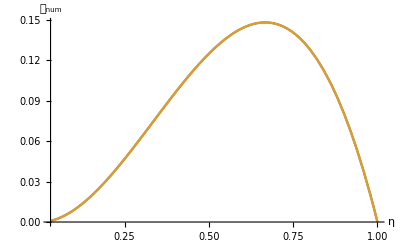

```mathematica
Plot[{DangWxl[η] ,χz[zbg[η]]} ,{η,ηin,ETA0},(*WorkingPrecision->10,*)AxesLabel->{"η","𝒟_num"}]
```

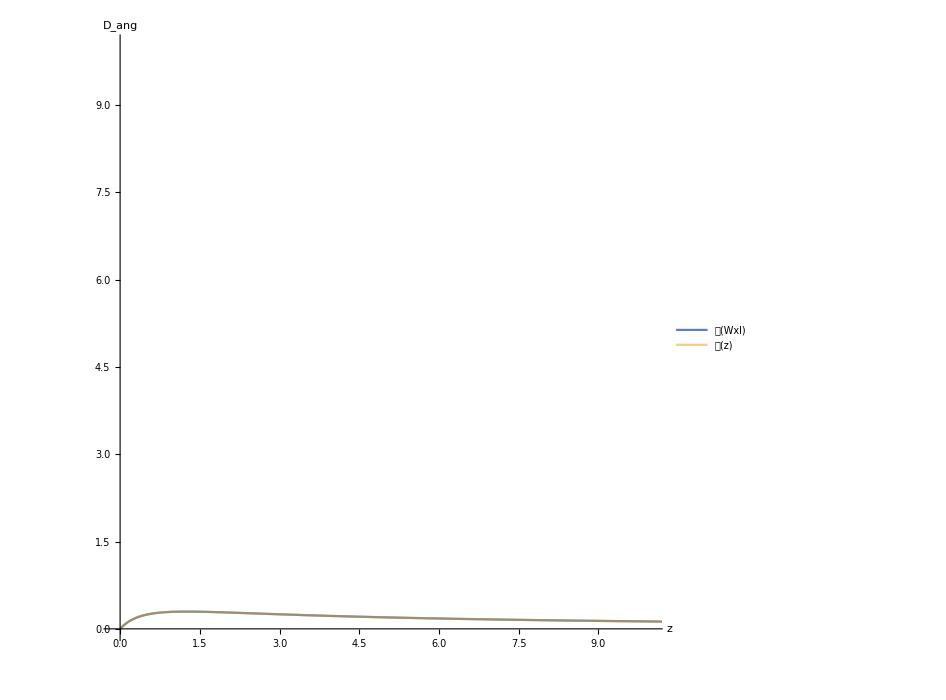

```mathematica
ParametricPlot[{{redshift[η],𝒽0 DangWxl[η]},{redshift[η],𝒽0 χz[redshift[η]]}},{η,ηin,ETA0},PlotRange->{{-0.1,10},{0,10}},PlotStyle->{Thick, Opacity[0.5]},AspectRatio->1,ImageSize->700,PlotLegends->{Style["𝒟(Wxl)",Large],Style["𝒟(z)",Large]},AxesLabel->{Style["z",Large],Style["D_ang",Large]}]
```

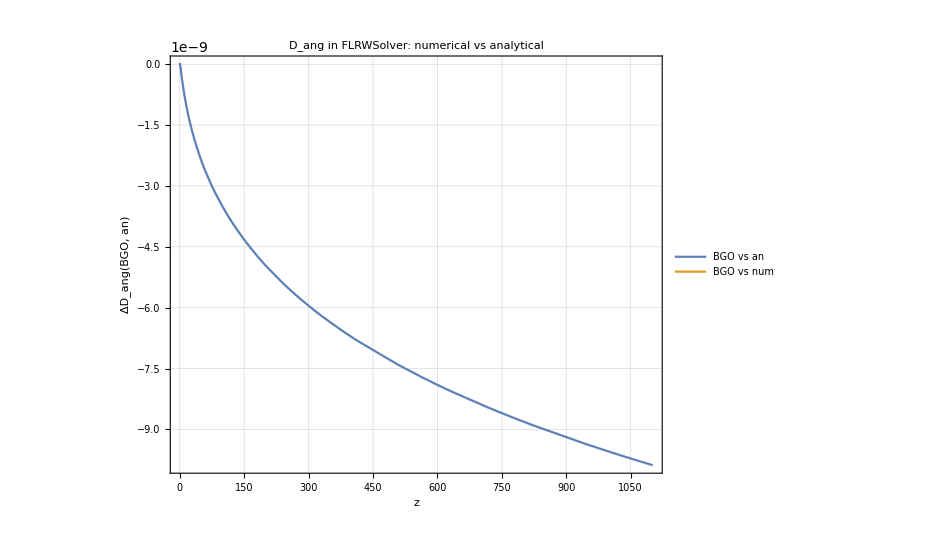

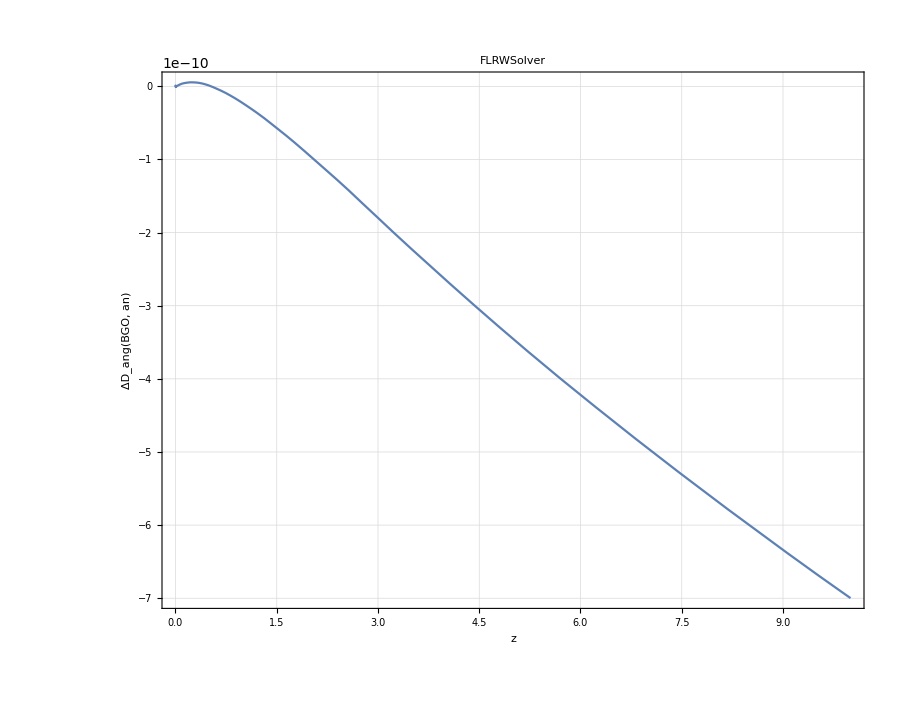

```mathematica
znum[η_]:=α[ETA0]/α[η]-1
ParametricPlot[{{redshift[η],  (DangWxl[η]-  χz[zbg[η]])/χz[zbg[η]]},{redshift[η],  (DangWxl[η]-  χz2[znum[η]])/χz2[znum[η]]}},{η,ηin,ETA0},PlotRange->All(*{{0,10},{0,2 10^-23}}*),ImageSize->700,AspectRatio->0.8,Evaluate[StandardPlotStyle[18,24,"ΔD_ang(BGO, an)","z","D_ang in FLRWSolver: numerical vs analytical",{"BGO vs an","BGO vs num"},{0.8,0.8}]]]
ParametricPlot[{redshift[η],  (DangWxl[η]-  χz[zbg[η]])/χz[zbg[η]]},{η,tz10,ETA0},PlotRange->All,ImageSize->900,AspectRatio->0.8,Evaluate[StandardPlotStyle[18,24,"ΔD_ang(BGO, an)","z","FLRWSolver",{},{}]](*, WorkingPrecision->48*)]
```

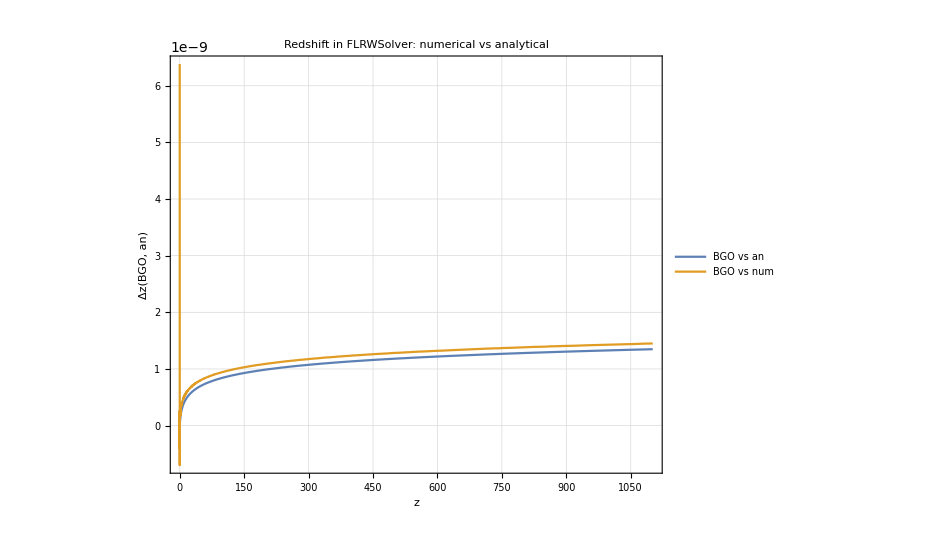

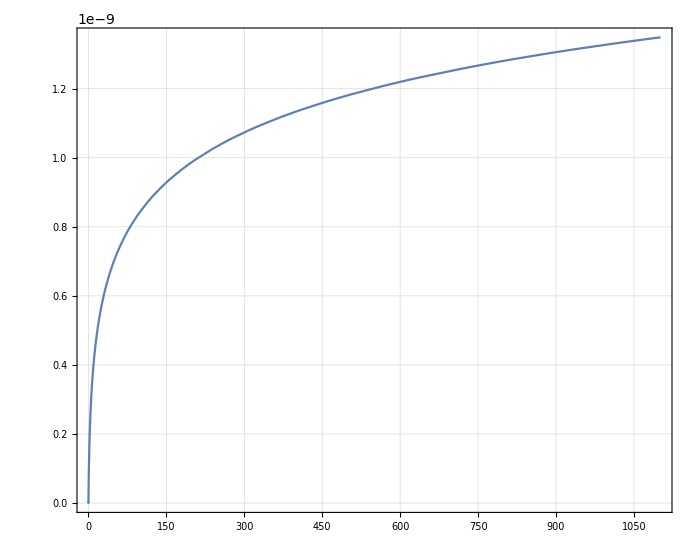

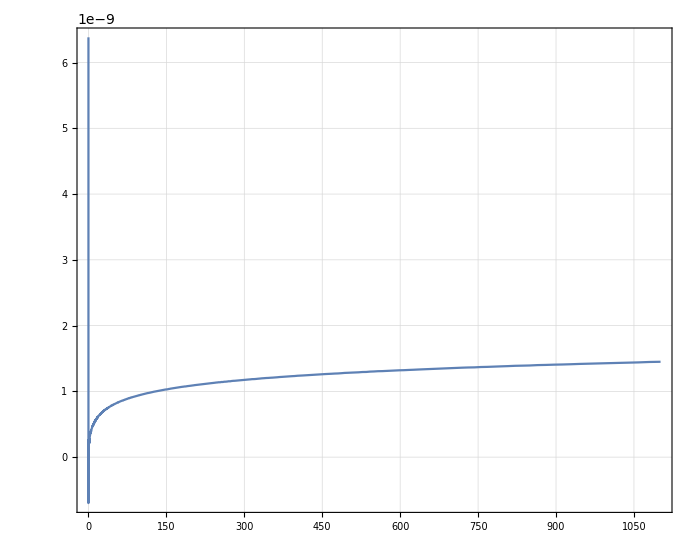

```mathematica
ParametricPlot[{{redshift[η], Evaluate[ redshift[η]/zbg[η]-1]},{redshift[η], Evaluate[ redshift[η]/znum[η]-1]}},{η,ηin,ETA0},(*WorkingPrecision->40,*)ImageSize->700,AspectRatio->0.8,PlotRange->All,Evaluate[StandardPlotStyle[18,24,"Δz(BGO, an)","z","Redshift in FLRWSolver: numerical vs analytical ",{"BGO vs an","BGO vs num"},{0.8,0.8}]]]
ParametricPlot[{redshift[η], Evaluate[ redshift[η]/zbg[η]-1]},{η,ηin,ETA0},(*WorkingPrecision->40,*)ImageSize->700,AspectRatio->0.8,PlotRange->All,Evaluate[StandardPlotStyle[16,24," "," "," ",{},{}]]]
ParametricPlot[{redshift[η], Evaluate[ redshift[η]/znum[η]-1]},{η,ηin,ETA0},(*WorkingPrecision->40,*)ImageSize->700,AspectRatio->0.8,PlotRange->All,Evaluate[StandardPlotStyle[16,24," "," "," ",{},{}]]]
```

### Angular diameter distance, Luminosity distance and Parallax distance

```mathematica
(*𝒲[t_]:=𝒲2[t]*)
```

```mathematica
Timing[tmpWAA=SetPrecision[Table[𝒲[η][[1,1]][[i,j]],{i,2,3},{j,2,3}],50];]
```

{0.005216,Null}

```mathematica
Timing[detWxxAB[t_]=SetPrecision[Evaluate[Simplify[Sqrt[Abs[(Det[tmpWAA])]]]/.η->t],50];]
```

{0.033076,Null}

```mathematica
(*Uvel[η_]:=Evaluate[Cu[η]nup[η]+Flatten[{0, Pu[η]}]]/.totBG*)
(*Timing[k[η_]:=Evaluate[EBG[η](nup[η]+Flatten[{0, VV[η]}])]/.totBG;
DangWxl[η_]=Evaluate[(gg4[ETA0].k[ETA0].u[ETA0])Evaluate[detWxlAB[η]]/.Join[param,totBG]];]*)
```

{19.2297,Null}

```mathematica
Dpar[η_]=Evaluate[(gg4[ETA0].k[ETA0].u[ETA0])Evaluate[detWxlAB[η]/detWxxAB[η]]/.Join[param,totBG]];
```

```mathematica
DangWxl[ETA0]
Dpar[ETA0]
```

0.

0.

```mathematica
(*redshift[t_]:=((gg4[t].u[t].k[t])/(gg4[ETA0].u[ETA0].k[ETA0])-1)/.Join[totBG,param]*)
```

```mathematica
Dlum[t_]=(1+redshift[t])^2 DangWxl[t];
```

```mathematica
ParametricPlot[{{redshift[t], 𝒽0 DangWxl[t]},{redshift[t],𝒽0 Dlum[t]},{redshift[t],𝒽0 Dpar[t]}} ,{t,ηin,ETA0},WorkingPrecision->30,ImageSize->700,AspectRatio->0.8,PlotRange->{{0,10},{0,1.5}},Evaluate[StandardPlotStyle[18,24,"D/D_ℋ_0","z","Distances in ΛCDM model",{"D_ang","D_lum","D_par"},{1,0.5}]]]
```

-Graphics-

```mathematica
ParametricPlot[{{redshift[t], 𝒽0 DangWxl[t]},{redshift[t],𝒽0 Dlum[t]},{redshift[t],𝒽0 Dpar[t]}} ,{t,ηin,ETA0},WorkingPrecision->30,ImageSize->700,AspectRatio->0.8,PlotRange->{{0,5},{0,15}},Evaluate[StandardPlotStyle[18,24,"D/D_ℋ_0","z","Distances in ΛCDM model",{"D_ang","D_lum","D_par"},{1,0.5}]]]
```

-Graphics-

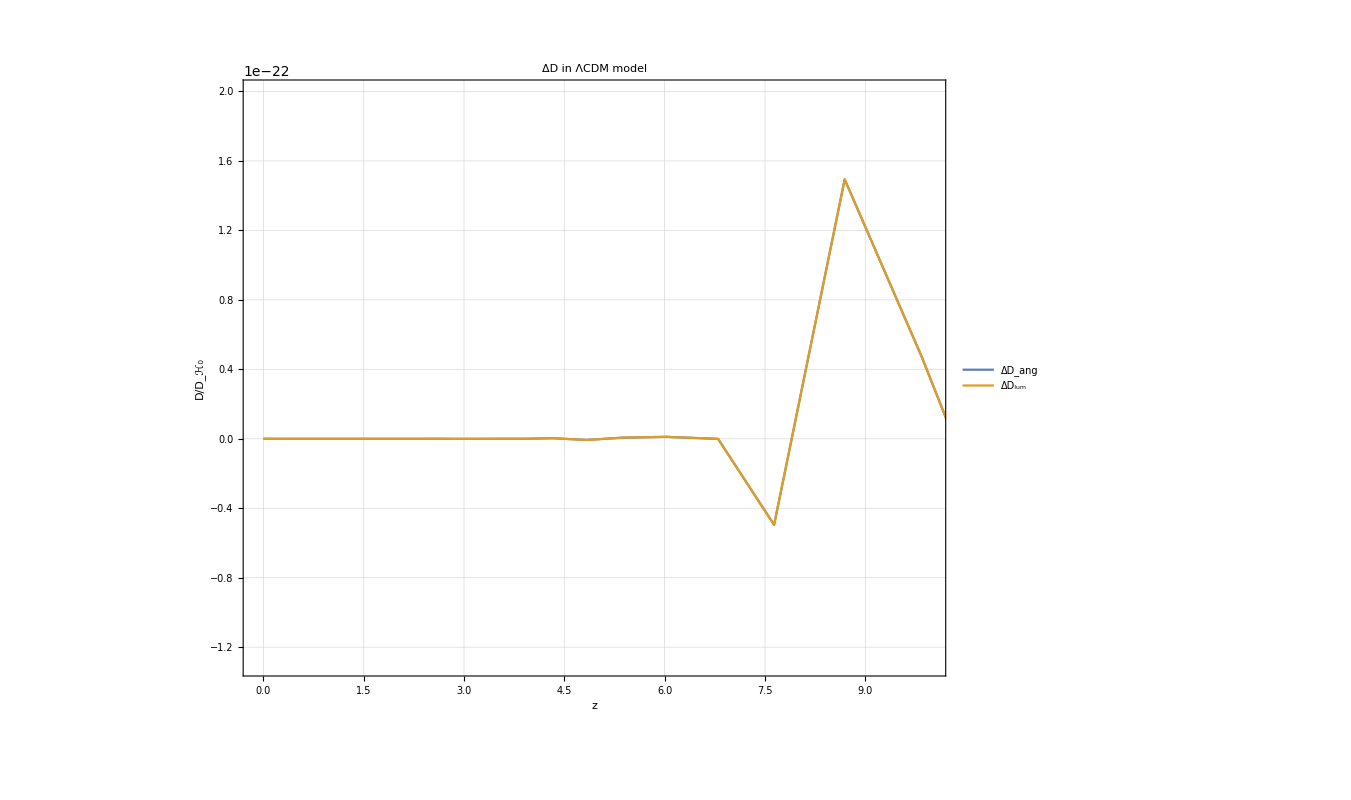

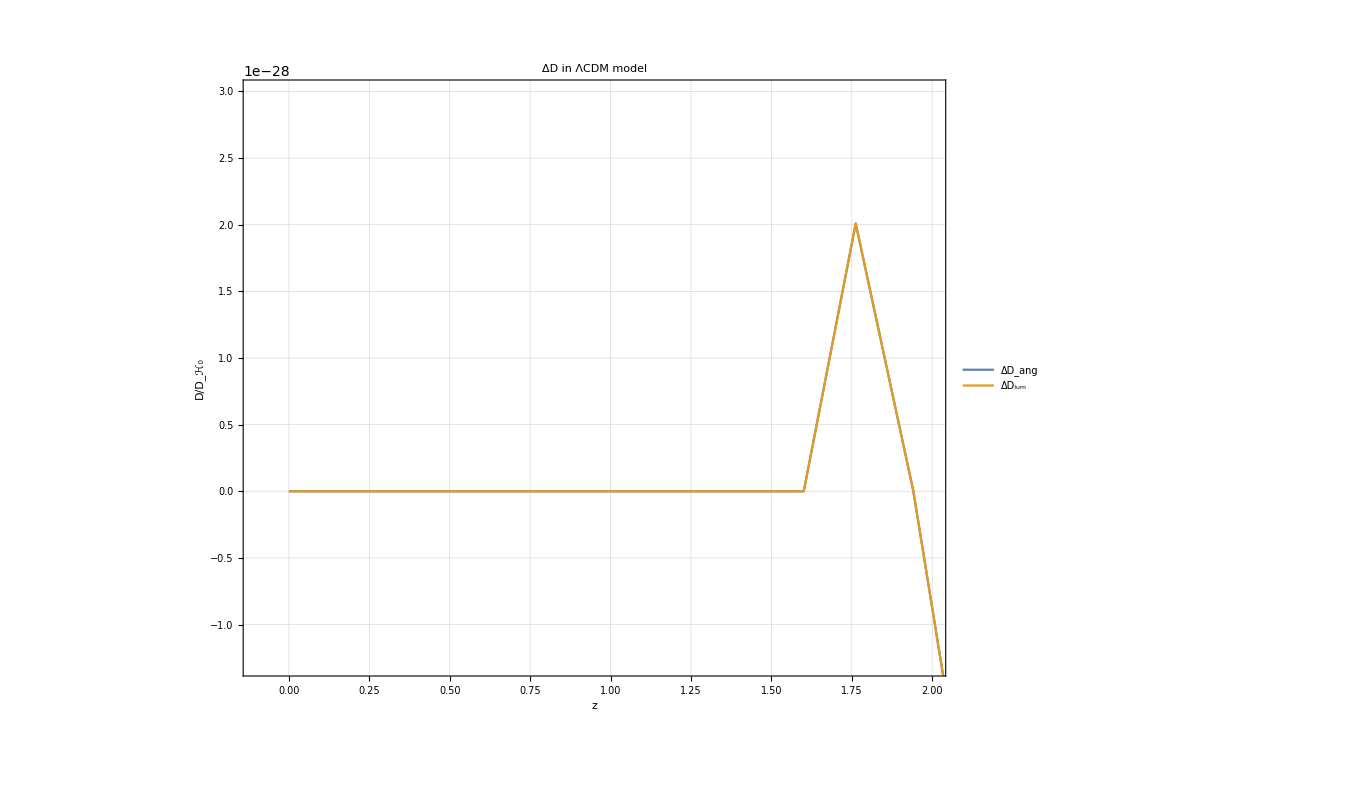

```mathematica
ParametricPlot[{{redshift[η],  (DangWxl[η]-(χz[redshift[η]]/(1+redshift[η])))/(χz[redshift[η]]/(1+redshift[η]))},{redshift[η], (Dlum[η]-((1+redshift[η])  χz[redshift[η]]))/((1+redshift[η])  χz[redshift[η]])}} ,{η,ηin,ETA0},WorkingPrecision->30,ImageSize->1000,AspectRatio->0.8,PlotRange->{{-0.1,10},{-1.3 10^-22,2 10^-22}},Evaluate[StandardPlotStyle[18,24,"D/D_ℋ_0","z","ΔD in ΛCDM model",{"ΔD_ang","ΔD_lum"},{0.2,0.8}]]]
ParametricPlot[{{redshift[η],  (DangWxl[η]-(χz[redshift[η]]/(1+redshift[η])))/(χz[redshift[η]]/(1+redshift[η]))},{redshift[η], (Dlum[η]-((1+redshift[η])  χz[redshift[η]]))/((1+redshift[η])  χz[redshift[η]])}} ,{η,ηin,ETA0},WorkingPrecision->30,ImageSize->1000,AspectRatio->0.8,PlotRange->{{-0.1,2},{-1.3 10^-28,3 10^-28}},Evaluate[StandardPlotStyle[18,24,"D/D_ℋ_0","z","ΔD in ΛCDM model",{"ΔD_ang","ΔD_lum"},{0.2,0.8}]]]
```

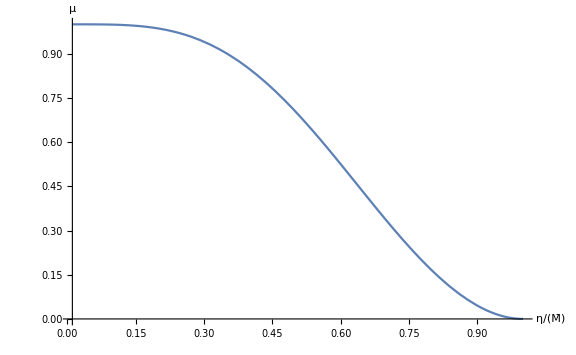

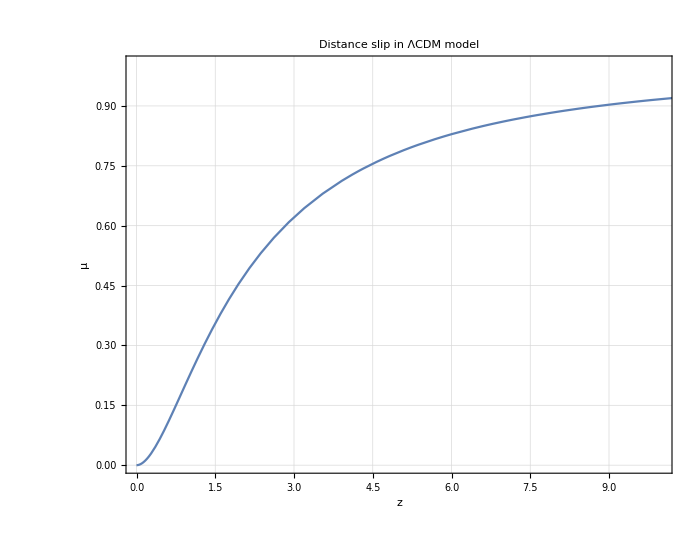

```mathematica
Plot[1-DangWxl[t]^2/Dpar[t]^2 ,{t,ηin,ETA0},WorkingPrecision->30,AxesLabel->{Style["η/(M̄)",Large],Style["μ",Large]},ImageSize->Large]
ParametricPlot[{redshift[t], 1-DangWxl[t]^2/Dpar[t]^2},{t,ηin,ETA0},WorkingPrecision->30,ImageSize->700,AspectRatio->0.8,PlotRange->{{0,10},{0,1.005}},Evaluate[StandardPlotStyle[18,24,"μ","z","Distance slip in ΛCDM model",{ },{ }]]]
```

### Drift effects

```mathematica
hUU={{0,0,0,1/Q},{0,1,0,0},{0,0,1,0},{1/Q,0,0,1/Q^2}};
hDD={{-1,0,0,Q},{0,1,0,0},{0,0,1,0},{Q,0,0,0}};
hUU.hDD//MatrixForm


functional[η_]:=Flatten[Table[{Mxx[[i,j]]->Mxx[[i,j]][η],Mxl[[i,j]]->Mxl[[i,j]][η],Mlx[[i,j]]->Mlx[[i,j]][η],Mll[[i,j]]->Mll[[i,j]][η]},{i,1,4},{j,1,4}]];
```

(1. | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0. | 0 | 0 | 1.)

```mathematica
𝒲XX[η_]:=Mxx/.functional[η];
𝒲LX[η_]:=Mlx/.functional[η];
𝒲XL[η_]:=Mxl/.functional[η];
𝒲LL[η_]:=Mll/.functional[η];
I𝒲XL[η_]:=Inverse[𝒲XL[η]];
```

```mathematica
Uoo[η_]:=-hDD.I𝒲XL[η].𝒲XX[η]
Uoe[η_]:=hDD.I𝒲XL[η]
Ueo[η_]:=-(hDD.𝒲LX[η]-hDD.𝒲LL[η].I𝒲XL[η].𝒲XX[η])
Uee[η_]:= -hDD.𝒲LL[η].I𝒲XL[η]
```

```mathematica
𝒰dd[η_]:= {{Uoo[η],Uoe[η]},{Ueo[η],Uee[η]}}
```

```mathematica
(*four acceleration can be calculated as a^ν==u^μ∇_μ u^ν*)
```

```mathematica
𝓊={1/𝒶[η],0,0,0}(*{u0[η],u1[η],u2[η],u3[η]}*);
Table[Sum[(𝓊[[j]]D[𝓊[[i]],X4[[j]]]),{j,1,4}]+Sum[Christoffel[{{-(𝒶[η])^2,0,0,0},{0,(𝒶[η])^2,0,0},{0,0,(𝒶[η])^2,0},{0,0,0,(𝒶[η])^2}},X4][[i,j,s]]𝓊[[j]]𝓊[[s]],{j,1,4},{s,1,4}]//Simplify,{i,1,4}]
```

{0,0,0,0}

```mathematica
e0[s_]=ldown[s]/Q;
e1[η_]=g4[η].(Evaluate[Cf1[η]nup[η]+Flatten[{0, P1[η]}]])/.totBG;
e2[η_]=g4[η].(Evaluate[Cf2[η]nup[η]+Flatten[{0, P2[η]}]])/.totBG;
e3[η_]=(g4[η].(Evaluate[Cu[η]nup[η]+Flatten[{0, Pu[η]}]])+e0[η])/Q/.totBG;
```

```mathematica
up[η_]:={e0[η].u[η],e1[η].u[η],e2[η].u[η],e3[η].u[η]}
```

```mathematica
uE[η_]:={e0[η].u[η],e1[η].u[η],e2[η].u[η],e3[η].u[η]}
aE[η_]:={0,0,0,0}
uO[η_]:=u[η]
aO[η_]:={0,0,0,0}
```

```mathematica
ΞDoppler[η_]:=(ldown[η]/(uE[η].ldown[η])).(aE[η]/(1+redshift[η]))-(ldown[ETA0]/(uO[ETA0].ldown[ETA0])).aO[ETA0]
lnzdrift[η_]:=(ΞDoppler[η]-1/(uO[ETA0].ldown[ETA0])(Uoo[η].uO[ETA0].uO[ETA0]+1/(1+redshift[η])Uoe[η].uO[ETA0].uE[η]+1/(1+redshift[η])Ueo[η].uE[η].uO[ETA0]+1/(1+redshift[η])^2 Uee[η].uE[η].uE[η]))/.BGO/.geodesic
```

```mathematica
cL=(299792458 3.24078 10^-23)/L(*c/L==(Mpc/s)/Mpc=1/s*)
```

3.62370784236154×10^-17

```mathematica
ANALITICzdrift[t_]:=𝒽0/(1+zbg[t])((1+zbg[t])-Sqrt[(1+zbg[t])^3])/.param
```

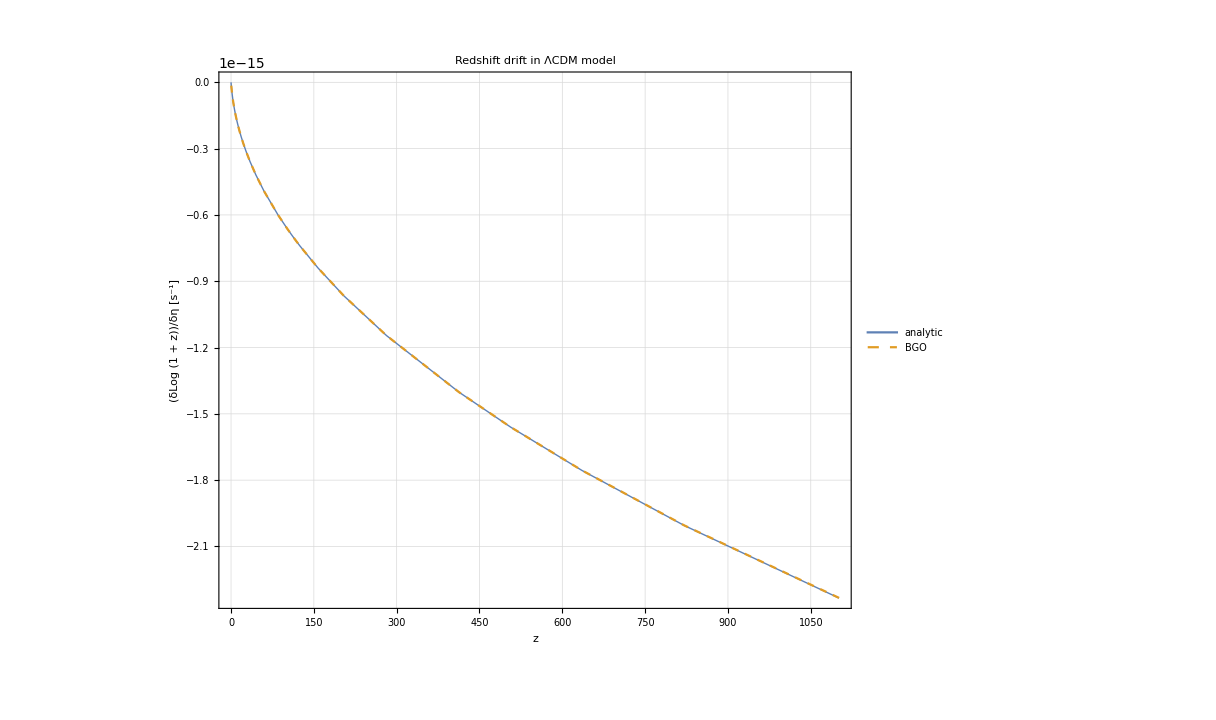
{244.202,-Graphics-}

```mathematica
AbsoluteTiming[ParametricPlot[{{redshift[t], cL ANALITICzdrift[t]},{redshift[t],cL lnzdrift[t]}},{t,ηin,ETA0},ImageSize->900,PlotRange->All,AspectRatio->0.8,PlotStyle->{Thick,Dashed},Evaluate[StandardPlotStyle[20,24,"(δLog (1 + z))/δη [s^-1]","z","Redshift drift in ΛCDM model",{"analytic","BGO" },{0.8,0.8 }]]]]
```

```mathematica
ParametricPlot[{redshift[t],lnzdrift[t]/ANALITICzdrift[t]-1},{t,tz10,ETA0},ImageSize->900,PlotRange->All,AspectRatio->0.8,WorkingPrecision->20,Evaluate[StandardPlotStyle[20,24,"Δδz(BGO,an)","z","FLRWSolver",{},{}]]]
(*ParametricPlot[{redshift[t],lnzdrift[t]/ANALITICzdrift[t]-1},{t,tz10,ETA0},ImageSize->900,PlotRange->{{0,10},{-2.5 10^-24,2.5 10^-24}},AspectRatio->0.8,WorkingPrecision->20,Evaluate[StandardPlotStyle[20,24,"","","Redshift drift in z∈[0,10]",{},{}]]]
Graphics[{White,Rectangle[]}]*)
```

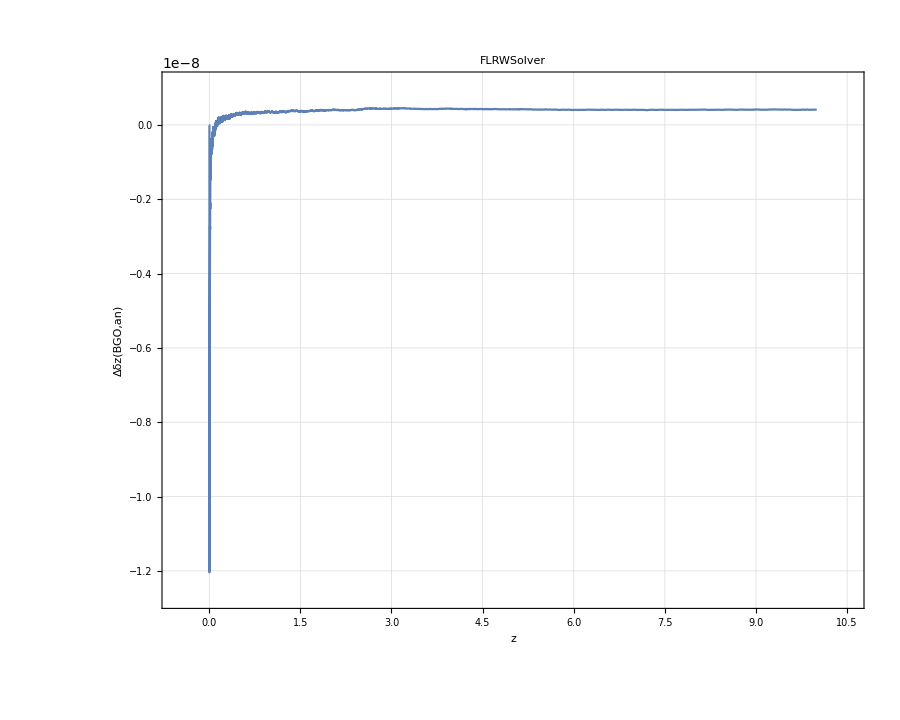

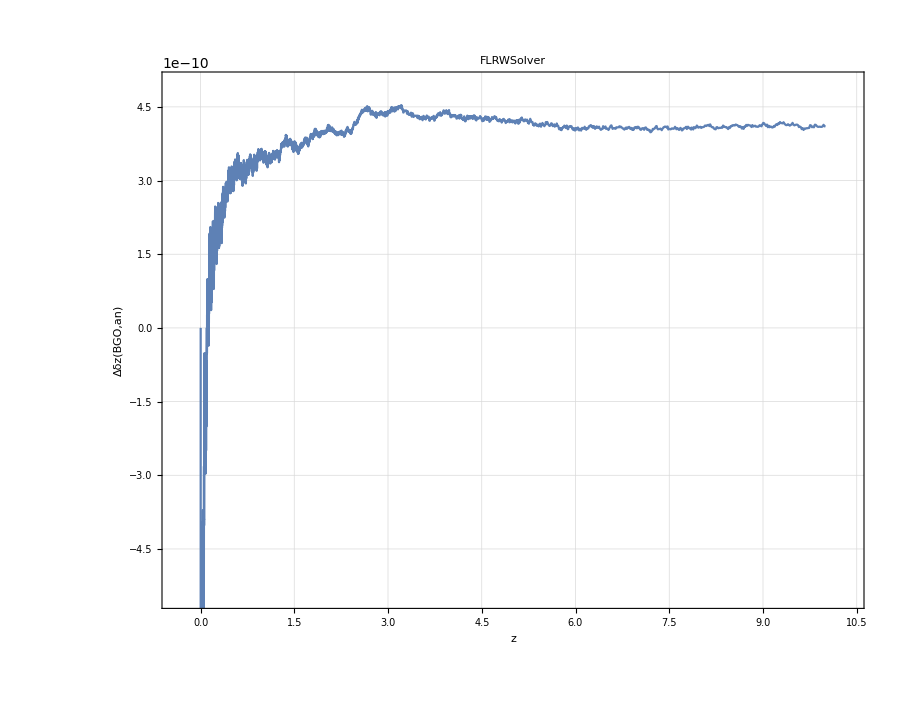

```mathematica
ParametricPlot[{redshift[t],lnzdrift[t]/ANALITICzdrift[t]-1},{t,tz10,ETA0},ImageSize->900,PlotRange->{{-0.4,10.4},{-5.5 10^-10,5 10^-10}},AspectRatio->0.8,WorkingPrecision->20,Evaluate[StandardPlotStyle[20,24,"Δδz(BGO,an)","z","FLRWSolver",{},{}]]]
```

```mathematica
{zFLRWSl->(Evaluate[redshift[#]]&),DangFLRWSl->(Evaluate[DangWxl[#]]&) ,(*DlumLCDM->(Evaluate[Dlum[#]]&) , DparLCDM->(Evaluate[Dpar[#]]&) ,*) ZdriftFLRWSl->(Evaluate[lnzdrift[#]]&) }>>"observables_FLRWSolverN_bisect.m"
```

$Aborted

```mathematica
Graphics[{White, Rectangle[]}]
```

-Graphics-

### Shear and expansion

```mathematica
Timing[tmpWllAB=SetPrecision[Table[𝒲[η][[2,2]][[i,j]],{i,2,3},{j,2,3}],50];]
IWxlAB=Inverse[tmpWAB];
```

{748.61,Null}

```mathematica
trxlll[t_]=SetPrecision[Evaluate[Tr[IWxlAB.tmpWllAB]/.η->t],50];
```

```mathematica
DDang[t_]=1/2 DangWxl[t] trxlll[t];
```

```mathematica
𝒮[t_]=Evaluate[(tmpWllAB.IWxlAB)//.η->t];
```

```mathematica
expansion[η_]=Tr[𝒮[η]]/2;
shear[η_]=Sqrt[(Tr[𝒮[η].𝒮[η]]/2-(Tr[𝒮[η]]/2)^2)];
```

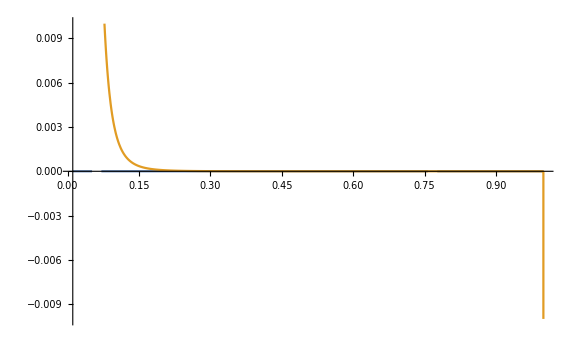

```mathematica
Plot[{shear[η],expansion[η]},{η,ηin,ETA0},ImageSize->Large,PlotRange->0.01]
```

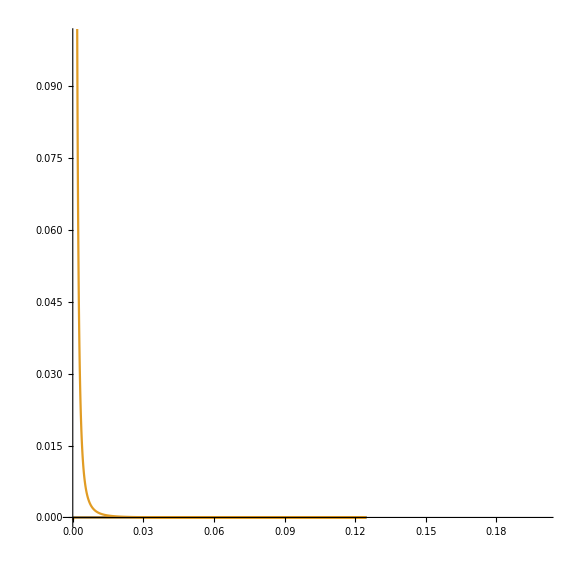

```mathematica
ParametricPlot[{{DangWxl[η], shear[η]},{DangWxl[η],expansion[η]}},{η,ηin,ETA0},ImageSize->Large,PlotRange->{{0,0.2},{0,0.1}}(*{{DangWxl[ETA0], DangWxl[ηin]},{-1,1}}*),AspectRatio->1]
```

```mathematica
δx={0,0,-10^-6/8,-10^-6/8};
δXf[t_]=𝒲[t][[1,2]].δx;
```

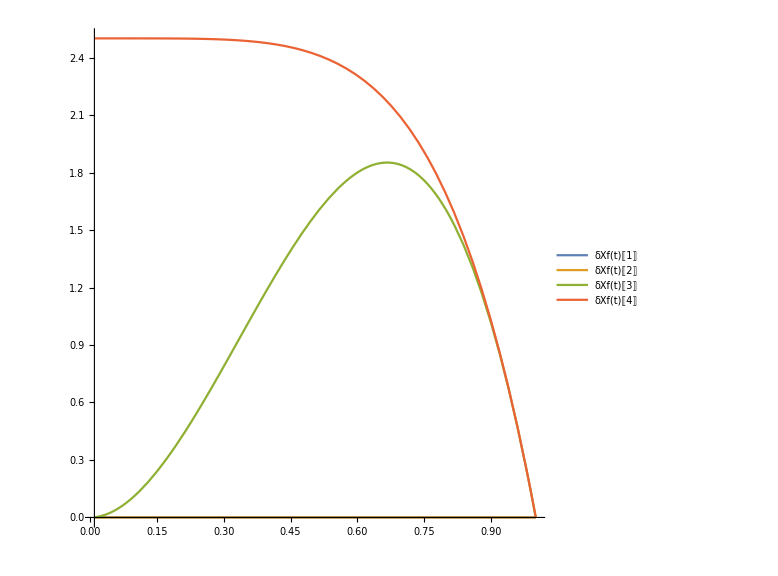

```mathematica
Plot[{δXf[t][[1]],δXf[t][[2]],δXf[t][[3]],δXf[t][[4]]},{t,ηin,ETA0},ImageSize->Large,AspectRatio->1,PlotLegends->"Expressions"]
```

```mathematica
δX0[t_]=(F0[t]/αα[t]).δXf[t]/.Join[param,totBG];
δX1[t_]=(F[t][[1]]-F0[t](ββ[t][[1]])/αα[t]).δXf[t]/.Join[param,totBG];
δX2[t_]=(F[t][[2]]-F0[t](ββ[t][[2]])/αα[t]).δXf[t]/.Join[param,totBG];
δX3[t_]=(F[t][[3]]-F0[t](ββ[t][[3]])/αα[t]).δXf[t]/.Join[param,totBG];
```

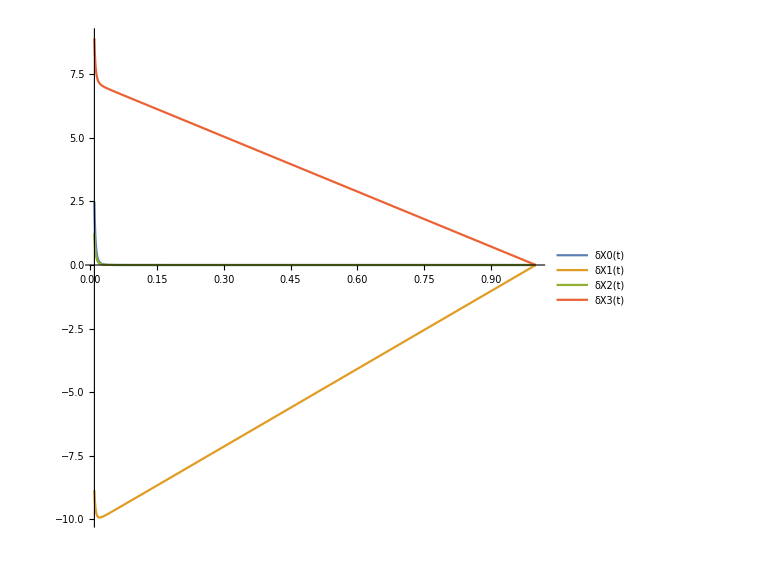

```mathematica
Plot[{δX0[t],δX1[t],δX2[t],δX3[t]},{t,ηin,ETA0},ImageSize->Large,AspectRatio->1,PlotLegends->"Expressions"]
```

```mathematica
Δx[t_]=-{δX0[t],δX1[t],δX2[t],δX3[t]}.ndown[t]/.Join[param,totBG];
ξ[t_]=({δX0[t],δX1[t],δX2[t],δX3[t]}-Δx[t]nup[t])/.Join[param,totBG];
```

```mathematica
Δx[ηin]
ξ[ηin]
```

0.000249999999975000122693

{0,-8.854145189105590659552,1.24999999987500061346,8.912476534011198821003}

```mathematica
δXc[t_]={ξ[t][[2]],ξ[t][[3]],ξ[t][[4]]};
trajectory[t_]=Evaluate[{x[t],y[t],z[t]}/.totBG];
Show[ParametricPlot3D[trajectory[η],{η,ηin,ETA0},PlotRange->{{-1,1},{-1,1},{-1,1}}](*/.Line[x_]:>Sequence[Arrowheads[Table[.02,{100/10}]],Arrow@Line[x]]*) ,Table[Graphics3D[{(*{Opacity[η/300+0.28],Black,Arrowheads[0.02],Arrow[{trajectory[η],(trajectory[η]+40(Pu[η]/.totBG))}]},{Opacity[η/300+0.28],Green,Arrowheads[0.02],Arrow[{trajectory[η],(trajectory[η]+40(P1[η]/.totBG))}]},{Opacity[η/300+0.28],Blue,Arrowheads[0.02],Arrow[{trajectory[η],(trajectory[η]+40(P2[η]/.totBG))}]},{*)(*Opacity[η/300+0.28],*)Red,Arrowheads[0.01],Arrow[{trajectory[η],(trajectory[η]+1/10(δXc[η]/.totBG))}]}],{η,ηin,ETA0,(ETA0-ηin)/30}] , ImageSize->700,AxesLabel->{Style["x/(M̄)",Large],Style["y/(M̄)",Large],Style["z/(M̄)",Large]},AxesStyle->Directive[Black,12],Boxed->False,ViewPoint->{0,100,10}]
```

-Graphics3D-